```mathematica
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
tf:=TableForm
mf:=MatrixForm
df:=Defer
```

# Analytic Number Theory

Arithmetic

## Division

## Greatest Common Divisor

## Prime Numbers

### Prime Gap size n

#### Example

```mathematica
ClearAll[f,g,h,h1,h2]
f[n_]:=Product[Prime[k],{k,1,n}]
g[n_]:=Table[{f[n]+2+k,FactorInteger[f[n]+2+k]},{k,0,n-1}]
h[n_]:=Table[{n!+2+k,FactorInteger[n!+2+k]},{k,0,n-1}]
h1[n_,m_]:=Table[{k+1,n!+2+k,FactorInteger[n!+2+k]},{k,0,m-1}]
h2[n_,m_]:=Select[Table[{k+1,n!+2+k,PrimeQ[n!+2+k]},{k,0,m-1}],#[[3]]==True&]
h2[19,100]//TableForm
FactorInteger[19!+1]
```

88 | 121645100408832089 | True

{{71,1},{1713311273363831,1}}

## Fundamental Theorem of Arithmetic

## Euclidean Algorithm

Tools

## Abel Summation

### Discrete Version

#### Example

```mathematica
ClearAll[a,f,s,A,abelSum];
a[r_]:=r/2
A[n_]:=Sum[a[k],{k,1,n}]
f[r_]:=r+1
s[n_]:=Sum[a[k]f[k],{k,1,n}]
abelSum[m_,n_]:=Sum[A[k](f[k]-f[k+1]),{k,m-1,n-1}]+A[n]f[n]-A[m-1]f[m-1]
abelSum[1,x]//Simplify;
Table[{s[k],abelSum[1,k],1/6 k (2+3 k+k^2)},{k,1,7}]//tf
```

1 | 1 | 1
4 | 4 | 4
10 | 10 | 10
20 | 20 | 20
35 | 35 | 35
56 | 56 | 56
84 | 84 | 84

Arithmetic Functions and Dirichlet Series

### Multiplicative Functions

#### Example

The Prime Number Theorem

Dirichlet’s Theorem

Error Estimates and the Riemann Hypothesis

Temp

## Tmp-1

```mathematica
Product[Sin[(π k/n)],{k,1,n-1}]
```

2^(1-n) n

```mathematica
Product[Gamma[k/n+1]/(k/n),{k,1,n-1}]//(TraditionalForm[Sqrt[#^2]]&)
```

√((2 π)^(n-1)/n)

```mathematica
ClearAll[Li];
Li[x_]:=Integrate[1/Log[y],{y,2,x}]
Li[20.]//N
```

8.86014

```mathematica
LogIntegral[20.]-LogIntegral[2.]
```

8.86014

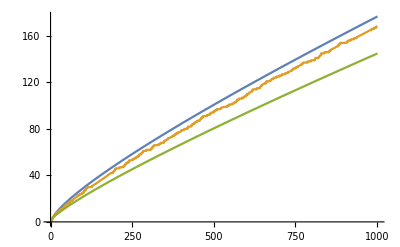

```mathematica
Plot[{LogIntegral[y]-LogIntegral[2],PrimePi[y],y/Log[y]},{y,2,1001},AxesOrigin->{0,0}]
```

## Tmp-2

```mathematica
ClearAll[f,tmp];
f[]:=Module[{s,s1,s2,k,l,a,b,from,to,c},
s={};
k=401;
While[k<800,
a=k;b=800-k;
If[PrimeQ[a]&& PrimeQ[b],
s=AppendTo[s,{a,b}]];
k=k+1;];
s1={};
s2={};
l=1;
While[l<Length[s]+1,
a=s[[l,1]];
b=s[[l,2]];
from=a-b+1;
to=a+b;
While[from<to,
c=from;
If[PrimeQ[c]&& PrimeQ[a+b-c]&& PrimeQ[a+c-b]&& PrimeQ[b+c-a]&& PrimeQ[a+b+c],
s1=AppendTo[s1,{a,b,c,a+b-c,a+c-b,b+c-a,a+b+c}]];
s2=AppendTo[s2,{a,b,c,a+b-c,a+c-b,b+c-a,a+b+c}];
from=from+1;
];
l=l+1];
s2]
tmp=f[]//tf
```

421 | 379 | 43 | 757 | 85 | 1 | 843
421 | 379 | 44 | 756 | 86 | 2 | 844
421 | 379 | 45 | 755 | 87 | 3 | 845
421 | 379 | 46 | 754 | 88 | 4 | 846
421 | 379 | 47 | 753 | 89 | 5 | 847
421 | 379 | 48 | 752 | 90 | 6 | 848
421 | 379 | 49 | 751 | 91 | 7 | 849
421 | 379 | 50 | 750 | 92 | 8 | 850
421 | 379 | 51 | 749 | 93 | 9 | 851
421 | 379 | 52 | 748 | 94 | 10 | 852
421 | 379 | 53 | 747 | 95 | 11 | 853
421 | 379 | 54 | 746 | 96 | 12 | 854
421 | 379 | 55 | 745 | 97 | 13 | 855
421 | 379 | 56 | 744 | 98 | 14 | 856
421 | 379 | 57 | 743 | 99 | 15 | 857
421 | 379 | 58 | 742 | 100 | 16 | 858
421 | 379 | 59 | 741 | 101 | 17 | 859
421 | 379 | 60 | 740 | 102 | 18 | 860
421 | 379 | 61 | 739 | 103 | 19 | 861
421 | 379 | 62 | 738 | 104 | 20 | 862
421 | 379 | 63 | 737 | 105 | 21 | 863
421 | 379 | 64 | 736 | 106 | 22 | 864
421 | 379 | 65 | 735 | 107 | 23 | 865
421 | 379 | 66 | 734 | 108 | 24 | 866
421 | 379 | 67 | 733 | 109 | 25 | 867
421 | 379 | 68 | 732 | 110 | 26 | 868
421 | 379 | 69 | 731 | 111 | 27 | 869
421 | 379 | 70 | 730 | 112 | 28 | 870
421 | 379 | 71 | 729 | 113 | 29 | 871
421 | 379 | 72 | 728 | 114 | 30 | 872
421 | 379 | 73 | 727 | 115 | 31 | 873
421 | 379 | 74 | 726 | 116 | 32 | 874
421 | 379 | 75 | 725 | 117 | 33 | 875
421 | 379 | 76 | 724 | 118 | 34 | 876
421 | 379 | 77 | 723 | 119 | 35 | 877
421 | 379 | 78 | 722 | 120 | 36 | 878
421 | 379 | 79 | 721 | 121 | 37 | 879
421 | 379 | 80 | 720 | 122 | 38 | 880
421 | 379 | 81 | 719 | 123 | 39 | 881
421 | 379 | 82 | 718 | 124 | 40 | 882
421 | 379 | 83 | 717 | 125 | 41 | 883
421 | 379 | 84 | 716 | 126 | 42 | 884
421 | 379 | 85 | 715 | 127 | 43 | 885
421 | 379 | 86 | 714 | 128 | 44 | 886
421 | 379 | 87 | 713 | 129 | 45 | 887
421 | 379 | 88 | 712 | 130 | 46 | 888
421 | 379 | 89 | 711 | 131 | 47 | 889
421 | 379 | 90 | 710 | 132 | 48 | 890
421 | 379 | 91 | 709 | 133 | 49 | 891
421 | 379 | 92 | 708 | 134 | 50 | 892
421 | 379 | 93 | 707 | 135 | 51 | 893
421 | 379 | 94 | 706 | 136 | 52 | 894
421 | 379 | 95 | 705 | 137 | 53 | 895
421 | 379 | 96 | 704 | 138 | 54 | 896
421 | 379 | 97 | 703 | 139 | 55 | 897
421 | 379 | 98 | 702 | 140 | 56 | 898
421 | 379 | 99 | 701 | 141 | 57 | 899
421 | 379 | 100 | 700 | 142 | 58 | 900
421 | 379 | 101 | 699 | 143 | 59 | 901
421 | 379 | 102 | 698 | 144 | 60 | 902
421 | 379 | 103 | 697 | 145 | 61 | 903
421 | 379 | 104 | 696 | 146 | 62 | 904
421 | 379 | 105 | 695 | 147 | 63 | 905
421 | 379 | 106 | 694 | 148 | 64 | 906
421 | 379 | 107 | 693 | 149 | 65 | 907
421 | 379 | 108 | 692 | 150 | 66 | 908
421 | 379 | 109 | 691 | 151 | 67 | 909
421 | 379 | 110 | 690 | 152 | 68 | 910
421 | 379 | 111 | 689 | 153 | 69 | 911
421 | 379 | 112 | 688 | 154 | 70 | 912
421 | 379 | 113 | 687 | 155 | 71 | 913
421 | 379 | 114 | 686 | 156 | 72 | 914
421 | 379 | 115 | 685 | 157 | 73 | 915
421 | 379 | 116 | 684 | 158 | 74 | 916
421 | 379 | 117 | 683 | 159 | 75 | 917
421 | 379 | 118 | 682 | 160 | 76 | 918
421 | 379 | 119 | 681 | 161 | 77 | 919
421 | 379 | 120 | 680 | 162 | 78 | 920
421 | 379 | 121 | 679 | 163 | 79 | 921
421 | 379 | 122 | 678 | 164 | 80 | 922
421 | 379 | 123 | 677 | 165 | 81 | 923
421 | 379 | 124 | 676 | 166 | 82 | 924
421 | 379 | 125 | 675 | 167 | 83 | 925
421 | 379 | 126 | 674 | 168 | 84 | 926
421 | 379 | 127 | 673 | 169 | 85 | 927
421 | 379 | 128 | 672 | 170 | 86 | 928
421 | 379 | 129 | 671 | 171 | 87 | 929
421 | 379 | 130 | 670 | 172 | 88 | 930
421 | 379 | 131 | 669 | 173 | 89 | 931
421 | 379 | 132 | 668 | 174 | 90 | 932
421 | 379 | 133 | 667 | 175 | 91 | 933
421 | 379 | 134 | 666 | 176 | 92 | 934
421 | 379 | 135 | 665 | 177 | 93 | 935
421 | 379 | 136 | 664 | 178 | 94 | 936
421 | 379 | 137 | 663 | 179 | 95 | 937
421 | 379 | 138 | 662 | 180 | 96 | 938
421 | 379 | 139 | 661 | 181 | 97 | 939
421 | 379 | 140 | 660 | 182 | 98 | 940
421 | 379 | 141 | 659 | 183 | 99 | 941
421 | 379 | 142 | 658 | 184 | 100 | 942
421 | 379 | 143 | 657 | 185 | 101 | 943
421 | 379 | 144 | 656 | 186 | 102 | 944
421 | 379 | 145 | 655 | 187 | 103 | 945
421 | 379 | 146 | 654 | 188 | 104 | 946
421 | 379 | 147 | 653 | 189 | 105 | 947
421 | 379 | 148 | 652 | 190 | 106 | 948
421 | 379 | 149 | 651 | 191 | 107 | 949
421 | 379 | 150 | 650 | 192 | 108 | 950
421 | 379 | 151 | 649 | 193 | 109 | 951
421 | 379 | 152 | 648 | 194 | 110 | 952
421 | 379 | 153 | 647 | 195 | 111 | 953
421 | 379 | 154 | 646 | 196 | 112 | 954
421 | 379 | 155 | 645 | 197 | 113 | 955
421 | 379 | 156 | 644 | 198 | 114 | 956
421 | 379 | 157 | 643 | 199 | 115 | 957
421 | 379 | 158 | 642 | 200 | 116 | 958
421 | 379 | 159 | 641 | 201 | 117 | 959
421 | 379 | 160 | 640 | 202 | 118 | 960
421 | 379 | 161 | 639 | 203 | 119 | 961
421 | 379 | 162 | 638 | 204 | 120 | 962
421 | 379 | 163 | 637 | 205 | 121 | 963
421 | 379 | 164 | 636 | 206 | 122 | 964
421 | 379 | 165 | 635 | 207 | 123 | 965
421 | 379 | 166 | 634 | 208 | 124 | 966
421 | 379 | 167 | 633 | 209 | 125 | 967
421 | 379 | 168 | 632 | 210 | 126 | 968
421 | 379 | 169 | 631 | 211 | 127 | 969
421 | 379 | 170 | 630 | 212 | 128 | 970
421 | 379 | 171 | 629 | 213 | 129 | 971
421 | 379 | 172 | 628 | 214 | 130 | 972
421 | 379 | 173 | 627 | 215 | 131 | 973
421 | 379 | 174 | 626 | 216 | 132 | 974
421 | 379 | 175 | 625 | 217 | 133 | 975
421 | 379 | 176 | 624 | 218 | 134 | 976
421 | 379 | 177 | 623 | 219 | 135 | 977
421 | 379 | 178 | 622 | 220 | 136 | 978
421 | 379 | 179 | 621 | 221 | 137 | 979
421 | 379 | 180 | 620 | 222 | 138 | 980
421 | 379 | 181 | 619 | 223 | 139 | 981
421 | 379 | 182 | 618 | 224 | 140 | 982
421 | 379 | 183 | 617 | 225 | 141 | 983
421 | 379 | 184 | 616 | 226 | 142 | 984
421 | 379 | 185 | 615 | 227 | 143 | 985
421 | 379 | 186 | 614 | 228 | 144 | 986
421 | 379 | 187 | 613 | 229 | 145 | 987
421 | 379 | 188 | 612 | 230 | 146 | 988
421 | 379 | 189 | 611 | 231 | 147 | 989
421 | 379 | 190 | 610 | 232 | 148 | 990
421 | 379 | 191 | 609 | 233 | 149 | 991
421 | 379 | 192 | 608 | 234 | 150 | 992
421 | 379 | 193 | 607 | 235 | 151 | 993
421 | 379 | 194 | 606 | 236 | 152 | 994
421 | 379 | 195 | 605 | 237 | 153 | 995
421 | 379 | 196 | 604 | 238 | 154 | 996
421 | 379 | 197 | 603 | 239 | 155 | 997
421 | 379 | 198 | 602 | 240 | 156 | 998
421 | 379 | 199 | 601 | 241 | 157 | 999
421 | 379 | 200 | 600 | 242 | 158 | 1000
421 | 379 | 201 | 599 | 243 | 159 | 1001
421 | 379 | 202 | 598 | 244 | 160 | 1002
421 | 379 | 203 | 597 | 245 | 161 | 1003
421 | 379 | 204 | 596 | 246 | 162 | 1004
421 | 379 | 205 | 595 | 247 | 163 | 1005
421 | 379 | 206 | 594 | 248 | 164 | 1006
421 | 379 | 207 | 593 | 249 | 165 | 1007
421 | 379 | 208 | 592 | 250 | 166 | 1008
421 | 379 | 209 | 591 | 251 | 167 | 1009
421 | 379 | 210 | 590 | 252 | 168 | 1010
421 | 379 | 211 | 589 | 253 | 169 | 1011
421 | 379 | 212 | 588 | 254 | 170 | 1012
421 | 379 | 213 | 587 | 255 | 171 | 1013
421 | 379 | 214 | 586 | 256 | 172 | 1014
421 | 379 | 215 | 585 | 257 | 173 | 1015
421 | 379 | 216 | 584 | 258 | 174 | 1016
421 | 379 | 217 | 583 | 259 | 175 | 1017
421 | 379 | 218 | 582 | 260 | 176 | 1018
421 | 379 | 219 | 581 | 261 | 177 | 1019
421 | 379 | 220 | 580 | 262 | 178 | 1020
421 | 379 | 221 | 579 | 263 | 179 | 1021
421 | 379 | 222 | 578 | 264 | 180 | 1022
421 | 379 | 223 | 577 | 265 | 181 | 1023
421 | 379 | 224 | 576 | 266 | 182 | 1024
421 | 379 | 225 | 575 | 267 | 183 | 1025
421 | 379 | 226 | 574 | 268 | 184 | 1026
421 | 379 | 227 | 573 | 269 | 185 | 1027
421 | 379 | 228 | 572 | 270 | 186 | 1028
421 | 379 | 229 | 571 | 271 | 187 | 1029
421 | 379 | 230 | 570 | 272 | 188 | 1030
421 | 379 | 231 | 569 | 273 | 189 | 1031
421 | 379 | 232 | 568 | 274 | 190 | 1032
421 | 379 | 233 | 567 | 275 | 191 | 1033
421 | 379 | 234 | 566 | 276 | 192 | 1034
421 | 379 | 235 | 565 | 277 | 193 | 1035
421 | 379 | 236 | 564 | 278 | 194 | 1036
421 | 379 | 237 | 563 | 279 | 195 | 1037
421 | 379 | 238 | 562 | 280 | 196 | 1038
421 | 379 | 239 | 561 | 281 | 197 | 1039
421 | 379 | 240 | 560 | 282 | 198 | 1040
421 | 379 | 241 | 559 | 283 | 199 | 1041
421 | 379 | 242 | 558 | 284 | 200 | 1042
421 | 379 | 243 | 557 | 285 | 201 | 1043
421 | 379 | 244 | 556 | 286 | 202 | 1044
421 | 379 | 245 | 555 | 287 | 203 | 1045
421 | 379 | 246 | 554 | 288 | 204 | 1046
421 | 379 | 247 | 553 | 289 | 205 | 1047
421 | 379 | 248 | 552 | 290 | 206 | 1048
421 | 379 | 249 | 551 | 291 | 207 | 1049
421 | 379 | 250 | 550 | 292 | 208 | 1050
421 | 379 | 251 | 549 | 293 | 209 | 1051
421 | 379 | 252 | 548 | 294 | 210 | 1052
421 | 379 | 253 | 547 | 295 | 211 | 1053
421 | 379 | 254 | 546 | 296 | 212 | 1054
421 | 379 | 255 | 545 | 297 | 213 | 1055
421 | 379 | 256 | 544 | 298 | 214 | 1056
421 | 379 | 257 | 543 | 299 | 215 | 1057
421 | 379 | 258 | 542 | 300 | 216 | 1058
421 | 379 | 259 | 541 | 301 | 217 | 1059
421 | 379 | 260 | 540 | 302 | 218 | 1060
421 | 379 | 261 | 539 | 303 | 219 | 1061
421 | 379 | 262 | 538 | 304 | 220 | 1062
421 | 379 | 263 | 537 | 305 | 221 | 1063
421 | 379 | 264 | 536 | 306 | 222 | 1064
421 | 379 | 265 | 535 | 307 | 223 | 1065
421 | 379 | 266 | 534 | 308 | 224 | 1066
421 | 379 | 267 | 533 | 309 | 225 | 1067
421 | 379 | 268 | 532 | 310 | 226 | 1068
421 | 379 | 269 | 531 | 311 | 227 | 1069
421 | 379 | 270 | 530 | 312 | 228 | 1070
421 | 379 | 271 | 529 | 313 | 229 | 1071
421 | 379 | 272 | 528 | 314 | 230 | 1072
421 | 379 | 273 | 527 | 315 | 231 | 1073
421 | 379 | 274 | 526 | 316 | 232 | 1074
421 | 379 | 275 | 525 | 317 | 233 | 1075
421 | 379 | 276 | 524 | 318 | 234 | 1076
421 | 379 | 277 | 523 | 319 | 235 | 1077
421 | 379 | 278 | 522 | 320 | 236 | 1078
421 | 379 | 279 | 521 | 321 | 237 | 1079
421 | 379 | 280 | 520 | 322 | 238 | 1080
421 | 379 | 281 | 519 | 323 | 239 | 1081
421 | 379 | 282 | 518 | 324 | 240 | 1082
421 | 379 | 283 | 517 | 325 | 241 | 1083
421 | 379 | 284 | 516 | 326 | 242 | 1084
421 | 379 | 285 | 515 | 327 | 243 | 1085
421 | 379 | 286 | 514 | 328 | 244 | 1086
421 | 379 | 287 | 513 | 329 | 245 | 1087
421 | 379 | 288 | 512 | 330 | 246 | 1088
421 | 379 | 289 | 511 | 331 | 247 | 1089
421 | 379 | 290 | 510 | 332 | 248 | 1090
421 | 379 | 291 | 509 | 333 | 249 | 1091
421 | 379 | 292 | 508 | 334 | 250 | 1092
421 | 379 | 293 | 507 | 335 | 251 | 1093
421 | 379 | 294 | 506 | 336 | 252 | 1094
421 | 379 | 295 | 505 | 337 | 253 | 1095
421 | 379 | 296 | 504 | 338 | 254 | 1096
421 | 379 | 297 | 503 | 339 | 255 | 1097
421 | 379 | 298 | 502 | 340 | 256 | 1098
421 | 379 | 299 | 501 | 341 | 257 | 1099
421 | 379 | 300 | 500 | 342 | 258 | 1100
421 | 379 | 301 | 499 | 343 | 259 | 1101
421 | 379 | 302 | 498 | 344 | 260 | 1102
421 | 379 | 303 | 497 | 345 | 261 | 1103
421 | 379 | 304 | 496 | 346 | 262 | 1104
421 | 379 | 305 | 495 | 347 | 263 | 1105
421 | 379 | 306 | 494 | 348 | 264 | 1106
421 | 379 | 307 | 493 | 349 | 265 | 1107
421 | 379 | 308 | 492 | 350 | 266 | 1108
421 | 379 | 309 | 491 | 351 | 267 | 1109
421 | 379 | 310 | 490 | 352 | 268 | 1110
421 | 379 | 311 | 489 | 353 | 269 | 1111
421 | 379 | 312 | 488 | 354 | 270 | 1112
421 | 379 | 313 | 487 | 355 | 271 | 1113
421 | 379 | 314 | 486 | 356 | 272 | 1114
421 | 379 | 315 | 485 | 357 | 273 | 1115
421 | 379 | 316 | 484 | 358 | 274 | 1116
421 | 379 | 317 | 483 | 359 | 275 | 1117
421 | 379 | 318 | 482 | 360 | 276 | 1118
421 | 379 | 319 | 481 | 361 | 277 | 1119
421 | 379 | 320 | 480 | 362 | 278 | 1120
421 | 379 | 321 | 479 | 363 | 279 | 1121
421 | 379 | 322 | 478 | 364 | 280 | 1122
421 | 379 | 323 | 477 | 365 | 281 | 1123
421 | 379 | 324 | 476 | 366 | 282 | 1124
421 | 379 | 325 | 475 | 367 | 283 | 1125
421 | 379 | 326 | 474 | 368 | 284 | 1126
421 | 379 | 327 | 473 | 369 | 285 | 1127
421 | 379 | 328 | 472 | 370 | 286 | 1128
421 | 379 | 329 | 471 | 371 | 287 | 1129
421 | 379 | 330 | 470 | 372 | 288 | 1130
421 | 379 | 331 | 469 | 373 | 289 | 1131
421 | 379 | 332 | 468 | 374 | 290 | 1132
421 | 379 | 333 | 467 | 375 | 291 | 1133
421 | 379 | 334 | 466 | 376 | 292 | 1134
421 | 379 | 335 | 465 | 377 | 293 | 1135
421 | 379 | 336 | 464 | 378 | 294 | 1136
421 | 379 | 337 | 463 | 379 | 295 | 1137
421 | 379 | 338 | 462 | 380 | 296 | 1138
421 | 379 | 339 | 461 | 381 | 297 | 1139
421 | 379 | 340 | 460 | 382 | 298 | 1140
421 | 379 | 341 | 459 | 383 | 299 | 1141
421 | 379 | 342 | 458 | 384 | 300 | 1142
421 | 379 | 343 | 457 | 385 | 301 | 1143
421 | 379 | 344 | 456 | 386 | 302 | 1144
421 | 379 | 345 | 455 | 387 | 303 | 1145
421 | 379 | 346 | 454 | 388 | 304 | 1146
421 | 379 | 347 | 453 | 389 | 305 | 1147
421 | 379 | 348 | 452 | 390 | 306 | 1148
421 | 379 | 349 | 451 | 391 | 307 | 1149
421 | 379 | 350 | 450 | 392 | 308 | 1150
421 | 379 | 351 | 449 | 393 | 309 | 1151
421 | 379 | 352 | 448 | 394 | 310 | 1152
421 | 379 | 353 | 447 | 395 | 311 | 1153
421 | 379 | 354 | 446 | 396 | 312 | 1154
421 | 379 | 355 | 445 | 397 | 313 | 1155
421 | 379 | 356 | 444 | 398 | 314 | 1156
421 | 379 | 357 | 443 | 399 | 315 | 1157
421 | 379 | 358 | 442 | 400 | 316 | 1158
421 | 379 | 359 | 441 | 401 | 317 | 1159
421 | 379 | 360 | 440 | 402 | 318 | 1160
421 | 379 | 361 | 439 | 403 | 319 | 1161
421 | 379 | 362 | 438 | 404 | 320 | 1162
421 | 379 | 363 | 437 | 405 | 321 | 1163
421 | 379 | 364 | 436 | 406 | 322 | 1164
421 | 379 | 365 | 435 | 407 | 323 | 1165
421 | 379 | 366 | 434 | 408 | 324 | 1166
421 | 379 | 367 | 433 | 409 | 325 | 1167
421 | 379 | 368 | 432 | 410 | 326 | 1168
421 | 379 | 369 | 431 | 411 | 327 | 1169
421 | 379 | 370 | 430 | 412 | 328 | 1170
421 | 379 | 371 | 429 | 413 | 329 | 1171
421 | 379 | 372 | 428 | 414 | 330 | 1172
421 | 379 | 373 | 427 | 415 | 331 | 1173
421 | 379 | 374 | 426 | 416 | 332 | 1174
421 | 379 | 375 | 425 | 417 | 333 | 1175
421 | 379 | 376 | 424 | 418 | 334 | 1176
421 | 379 | 377 | 423 | 419 | 335 | 1177
421 | 379 | 378 | 422 | 420 | 336 | 1178
421 | 379 | 379 | 421 | 421 | 337 | 1179
421 | 379 | 380 | 420 | 422 | 338 | 1180
421 | 379 | 381 | 419 | 423 | 339 | 1181
421 | 379 | 382 | 418 | 424 | 340 | 1182
421 | 379 | 383 | 417 | 425 | 341 | 1183
421 | 379 | 384 | 416 | 426 | 342 | 1184
421 | 379 | 385 | 415 | 427 | 343 | 1185
421 | 379 | 386 | 414 | 428 | 344 | 1186
421 | 379 | 387 | 413 | 429 | 345 | 1187
421 | 379 | 388 | 412 | 430 | 346 | 1188
421 | 379 | 389 | 411 | 431 | 347 | 1189
421 | 379 | 390 | 410 | 432 | 348 | 1190
421 | 379 | 391 | 409 | 433 | 349 | 1191
421 | 379 | 392 | 408 | 434 | 350 | 1192
421 | 379 | 393 | 407 | 435 | 351 | 1193
421 | 379 | 394 | 406 | 436 | 352 | 1194
421 | 379 | 395 | 405 | 437 | 353 | 1195
421 | 379 | 396 | 404 | 438 | 354 | 1196
421 | 379 | 397 | 403 | 439 | 355 | 1197
421 | 379 | 398 | 402 | 440 | 356 | 1198
421 | 379 | 399 | 401 | 441 | 357 | 1199
421 | 379 | 400 | 400 | 442 | 358 | 1200
421 | 379 | 401 | 399 | 443 | 359 | 1201
421 | 379 | 402 | 398 | 444 | 360 | 1202
421 | 379 | 403 | 397 | 445 | 361 | 1203
421 | 379 | 404 | 396 | 446 | 362 | 1204
421 | 379 | 405 | 395 | 447 | 363 | 1205
421 | 379 | 406 | 394 | 448 | 364 | 1206
421 | 379 | 407 | 393 | 449 | 365 | 1207
421 | 379 | 408 | 392 | 450 | 366 | 1208
421 | 379 | 409 | 391 | 451 | 367 | 1209
421 | 379 | 410 | 390 | 452 | 368 | 1210
421 | 379 | 411 | 389 | 453 | 369 | 1211
421 | 379 | 412 | 388 | 454 | 370 | 1212
421 | 379 | 413 | 387 | 455 | 371 | 1213
421 | 379 | 414 | 386 | 456 | 372 | 1214
421 | 379 | 415 | 385 | 457 | 373 | 1215
421 | 379 | 416 | 384 | 458 | 374 | 1216
421 | 379 | 417 | 383 | 459 | 375 | 1217
421 | 379 | 418 | 382 | 460 | 376 | 1218
421 | 379 | 419 | 381 | 461 | 377 | 1219
421 | 379 | 420 | 380 | 462 | 378 | 1220
421 | 379 | 421 | 379 | 463 | 379 | 1221
421 | 379 | 422 | 378 | 464 | 380 | 1222
421 | 379 | 423 | 377 | 465 | 381 | 1223
421 | 379 | 424 | 376 | 466 | 382 | 1224
421 | 379 | 425 | 375 | 467 | 383 | 1225
421 | 379 | 426 | 374 | 468 | 384 | 1226
421 | 379 | 427 | 373 | 469 | 385 | 1227
421 | 379 | 428 | 372 | 470 | 386 | 1228
421 | 379 | 429 | 371 | 471 | 387 | 1229
421 | 379 | 430 | 370 | 472 | 388 | 1230
421 | 379 | 431 | 369 | 473 | 389 | 1231
421 | 379 | 432 | 368 | 474 | 390 | 1232
421 | 379 | 433 | 367 | 475 | 391 | 1233
421 | 379 | 434 | 366 | 476 | 392 | 1234
421 | 379 | 435 | 365 | 477 | 393 | 1235
421 | 379 | 436 | 364 | 478 | 394 | 1236
421 | 379 | 437 | 363 | 479 | 395 | 1237
421 | 379 | 438 | 362 | 480 | 396 | 1238
421 | 379 | 439 | 361 | 481 | 397 | 1239
421 | 379 | 440 | 360 | 482 | 398 | 1240
421 | 379 | 441 | 359 | 483 | 399 | 1241
421 | 379 | 442 | 358 | 484 | 400 | 1242
421 | 379 | 443 | 357 | 485 | 401 | 1243
421 | 379 | 444 | 356 | 486 | 402 | 1244
421 | 379 | 445 | 355 | 487 | 403 | 1245
421 | 379 | 446 | 354 | 488 | 404 | 1246
421 | 379 | 447 | 353 | 489 | 405 | 1247
421 | 379 | 448 | 352 | 490 | 406 | 1248
421 | 379 | 449 | 351 | 491 | 407 | 1249
421 | 379 | 450 | 350 | 492 | 408 | 1250
421 | 379 | 451 | 349 | 493 | 409 | 1251
421 | 379 | 452 | 348 | 494 | 410 | 1252
421 | 379 | 453 | 347 | 495 | 411 | 1253
421 | 379 | 454 | 346 | 496 | 412 | 1254
421 | 379 | 455 | 345 | 497 | 413 | 1255
421 | 379 | 456 | 344 | 498 | 414 | 1256
421 | 379 | 457 | 343 | 499 | 415 | 1257
421 | 379 | 458 | 342 | 500 | 416 | 1258
421 | 379 | 459 | 341 | 501 | 417 | 1259
421 | 379 | 460 | 340 | 502 | 418 | 1260
421 | 379 | 461 | 339 | 503 | 419 | 1261
421 | 379 | 462 | 338 | 504 | 420 | 1262
421 | 379 | 463 | 337 | 505 | 421 | 1263
421 | 379 | 464 | 336 | 506 | 422 | 1264
421 | 379 | 465 | 335 | 507 | 423 | 1265
421 | 379 | 466 | 334 | 508 | 424 | 1266
421 | 379 | 467 | 333 | 509 | 425 | 1267
421 | 379 | 468 | 332 | 510 | 426 | 1268
421 | 379 | 469 | 331 | 511 | 427 | 1269
421 | 379 | 470 | 330 | 512 | 428 | 1270
421 | 379 | 471 | 329 | 513 | 429 | 1271
421 | 379 | 472 | 328 | 514 | 430 | 1272
421 | 379 | 473 | 327 | 515 | 431 | 1273
421 | 379 | 474 | 326 | 516 | 432 | 1274
421 | 379 | 475 | 325 | 517 | 433 | 1275
421 | 379 | 476 | 324 | 518 | 434 | 1276
421 | 379 | 477 | 323 | 519 | 435 | 1277
421 | 379 | 478 | 322 | 520 | 436 | 1278
421 | 379 | 479 | 321 | 521 | 437 | 1279
421 | 379 | 480 | 320 | 522 | 438 | 1280
421 | 379 | 481 | 319 | 523 | 439 | 1281
421 | 379 | 482 | 318 | 524 | 440 | 1282
421 | 379 | 483 | 317 | 525 | 441 | 1283
421 | 379 | 484 | 316 | 526 | 442 | 1284
421 | 379 | 485 | 315 | 527 | 443 | 1285
421 | 379 | 486 | 314 | 528 | 444 | 1286
421 | 379 | 487 | 313 | 529 | 445 | 1287
421 | 379 | 488 | 312 | 530 | 446 | 1288
421 | 379 | 489 | 311 | 531 | 447 | 1289
421 | 379 | 490 | 310 | 532 | 448 | 1290
421 | 379 | 491 | 309 | 533 | 449 | 1291
421 | 379 | 492 | 308 | 534 | 450 | 1292
421 | 379 | 493 | 307 | 535 | 451 | 1293
421 | 379 | 494 | 306 | 536 | 452 | 1294
421 | 379 | 495 | 305 | 537 | 453 | 1295
421 | 379 | 496 | 304 | 538 | 454 | 1296
421 | 379 | 497 | 303 | 539 | 455 | 1297
421 | 379 | 498 | 302 | 540 | 456 | 1298
421 | 379 | 499 | 301 | 541 | 457 | 1299
421 | 379 | 500 | 300 | 542 | 458 | 1300
421 | 379 | 501 | 299 | 543 | 459 | 1301
421 | 379 | 502 | 298 | 544 | 460 | 1302
421 | 379 | 503 | 297 | 545 | 461 | 1303
421 | 379 | 504 | 296 | 546 | 462 | 1304
421 | 379 | 505 | 295 | 547 | 463 | 1305
421 | 379 | 506 | 294 | 548 | 464 | 1306
421 | 379 | 507 | 293 | 549 | 465 | 1307
421 | 379 | 508 | 292 | 550 | 466 | 1308
421 | 379 | 509 | 291 | 551 | 467 | 1309
421 | 379 | 510 | 290 | 552 | 468 | 1310
421 | 379 | 511 | 289 | 553 | 469 | 1311
421 | 379 | 512 | 288 | 554 | 470 | 1312
421 | 379 | 513 | 287 | 555 | 471 | 1313
421 | 379 | 514 | 286 | 556 | 472 | 1314
421 | 379 | 515 | 285 | 557 | 473 | 1315
421 | 379 | 516 | 284 | 558 | 474 | 1316
421 | 379 | 517 | 283 | 559 | 475 | 1317
421 | 379 | 518 | 282 | 560 | 476 | 1318
421 | 379 | 519 | 281 | 561 | 477 | 1319
421 | 379 | 520 | 280 | 562 | 478 | 1320
421 | 379 | 521 | 279 | 563 | 479 | 1321
421 | 379 | 522 | 278 | 564 | 480 | 1322
421 | 379 | 523 | 277 | 565 | 481 | 1323
421 | 379 | 524 | 276 | 566 | 482 | 1324
421 | 379 | 525 | 275 | 567 | 483 | 1325
421 | 379 | 526 | 274 | 568 | 484 | 1326
421 | 379 | 527 | 273 | 569 | 485 | 1327
421 | 379 | 528 | 272 | 570 | 486 | 1328
421 | 379 | 529 | 271 | 571 | 487 | 1329
421 | 379 | 530 | 270 | 572 | 488 | 1330
421 | 379 | 531 | 269 | 573 | 489 | 1331
421 | 379 | 532 | 268 | 574 | 490 | 1332
421 | 379 | 533 | 267 | 575 | 491 | 1333
421 | 379 | 534 | 266 | 576 | 492 | 1334
421 | 379 | 535 | 265 | 577 | 493 | 1335
421 | 379 | 536 | 264 | 578 | 494 | 1336
421 | 379 | 537 | 263 | 579 | 495 | 1337
421 | 379 | 538 | 262 | 580 | 496 | 1338
421 | 379 | 539 | 261 | 581 | 497 | 1339
421 | 379 | 540 | 260 | 582 | 498 | 1340
421 | 379 | 541 | 259 | 583 | 499 | 1341
421 | 379 | 542 | 258 | 584 | 500 | 1342
421 | 379 | 543 | 257 | 585 | 501 | 1343
421 | 379 | 544 | 256 | 586 | 502 | 1344
421 | 379 | 545 | 255 | 587 | 503 | 1345
421 | 379 | 546 | 254 | 588 | 504 | 1346
421 | 379 | 547 | 253 | 589 | 505 | 1347
421 | 379 | 548 | 252 | 590 | 506 | 1348
421 | 379 | 549 | 251 | 591 | 507 | 1349
421 | 379 | 550 | 250 | 592 | 508 | 1350
421 | 379 | 551 | 249 | 593 | 509 | 1351
421 | 379 | 552 | 248 | 594 | 510 | 1352
421 | 379 | 553 | 247 | 595 | 511 | 1353
421 | 379 | 554 | 246 | 596 | 512 | 1354
421 | 379 | 555 | 245 | 597 | 513 | 1355
421 | 379 | 556 | 244 | 598 | 514 | 1356
421 | 379 | 557 | 243 | 599 | 515 | 1357
421 | 379 | 558 | 242 | 600 | 516 | 1358
421 | 379 | 559 | 241 | 601 | 517 | 1359
421 | 379 | 560 | 240 | 602 | 518 | 1360
421 | 379 | 561 | 239 | 603 | 519 | 1361
421 | 379 | 562 | 238 | 604 | 520 | 1362
421 | 379 | 563 | 237 | 605 | 521 | 1363
421 | 379 | 564 | 236 | 606 | 522 | 1364
421 | 379 | 565 | 235 | 607 | 523 | 1365
421 | 379 | 566 | 234 | 608 | 524 | 1366
421 | 379 | 567 | 233 | 609 | 525 | 1367
421 | 379 | 568 | 232 | 610 | 526 | 1368
421 | 379 | 569 | 231 | 611 | 527 | 1369
421 | 379 | 570 | 230 | 612 | 528 | 1370
421 | 379 | 571 | 229 | 613 | 529 | 1371
421 | 379 | 572 | 228 | 614 | 530 | 1372
421 | 379 | 573 | 227 | 615 | 531 | 1373
421 | 379 | 574 | 226 | 616 | 532 | 1374
421 | 379 | 575 | 225 | 617 | 533 | 1375
421 | 379 | 576 | 224 | 618 | 534 | 1376
421 | 379 | 577 | 223 | 619 | 535 | 1377
421 | 379 | 578 | 222 | 620 | 536 | 1378
421 | 379 | 579 | 221 | 621 | 537 | 1379
421 | 379 | 580 | 220 | 622 | 538 | 1380
421 | 379 | 581 | 219 | 623 | 539 | 1381
421 | 379 | 582 | 218 | 624 | 540 | 1382
421 | 379 | 583 | 217 | 625 | 541 | 1383
421 | 379 | 584 | 216 | 626 | 542 | 1384
421 | 379 | 585 | 215 | 627 | 543 | 1385
421 | 379 | 586 | 214 | 628 | 544 | 1386
421 | 379 | 587 | 213 | 629 | 545 | 1387
421 | 379 | 588 | 212 | 630 | 546 | 1388
421 | 379 | 589 | 211 | 631 | 547 | 1389
421 | 379 | 590 | 210 | 632 | 548 | 1390
421 | 379 | 591 | 209 | 633 | 549 | 1391
421 | 379 | 592 | 208 | 634 | 550 | 1392
421 | 379 | 593 | 207 | 635 | 551 | 1393
421 | 379 | 594 | 206 | 636 | 552 | 1394
421 | 379 | 595 | 205 | 637 | 553 | 1395
421 | 379 | 596 | 204 | 638 | 554 | 1396
421 | 379 | 597 | 203 | 639 | 555 | 1397
421 | 379 | 598 | 202 | 640 | 556 | 1398
421 | 379 | 599 | 201 | 641 | 557 | 1399
421 | 379 | 600 | 200 | 642 | 558 | 1400
421 | 379 | 601 | 199 | 643 | 559 | 1401
421 | 379 | 602 | 198 | 644 | 560 | 1402
421 | 379 | 603 | 197 | 645 | 561 | 1403
421 | 379 | 604 | 196 | 646 | 562 | 1404
421 | 379 | 605 | 195 | 647 | 563 | 1405
421 | 379 | 606 | 194 | 648 | 564 | 1406
421 | 379 | 607 | 193 | 649 | 565 | 1407
421 | 379 | 608 | 192 | 650 | 566 | 1408
421 | 379 | 609 | 191 | 651 | 567 | 1409
421 | 379 | 610 | 190 | 652 | 568 | 1410
421 | 379 | 611 | 189 | 653 | 569 | 1411
421 | 379 | 612 | 188 | 654 | 570 | 1412
421 | 379 | 613 | 187 | 655 | 571 | 1413
421 | 379 | 614 | 186 | 656 | 572 | 1414
421 | 379 | 615 | 185 | 657 | 573 | 1415
421 | 379 | 616 | 184 | 658 | 574 | 1416
421 | 379 | 617 | 183 | 659 | 575 | 1417
421 | 379 | 618 | 182 | 660 | 576 | 1418
421 | 379 | 619 | 181 | 661 | 577 | 1419
421 | 379 | 620 | 180 | 662 | 578 | 1420
421 | 379 | 621 | 179 | 663 | 579 | 1421
421 | 379 | 622 | 178 | 664 | 580 | 1422
421 | 379 | 623 | 177 | 665 | 581 | 1423
421 | 379 | 624 | 176 | 666 | 582 | 1424
421 | 379 | 625 | 175 | 667 | 583 | 1425
421 | 379 | 626 | 174 | 668 | 584 | 1426
421 | 379 | 627 | 173 | 669 | 585 | 1427
421 | 379 | 628 | 172 | 670 | 586 | 1428
421 | 379 | 629 | 171 | 671 | 587 | 1429
421 | 379 | 630 | 170 | 672 | 588 | 1430
421 | 379 | 631 | 169 | 673 | 589 | 1431
421 | 379 | 632 | 168 | 674 | 590 | 1432
421 | 379 | 633 | 167 | 675 | 591 | 1433
421 | 379 | 634 | 166 | 676 | 592 | 1434
421 | 379 | 635 | 165 | 677 | 593 | 1435
421 | 379 | 636 | 164 | 678 | 594 | 1436
421 | 379 | 637 | 163 | 679 | 595 | 1437
421 | 379 | 638 | 162 | 680 | 596 | 1438
421 | 379 | 639 | 161 | 681 | 597 | 1439
421 | 379 | 640 | 160 | 682 | 598 | 1440
421 | 379 | 641 | 159 | 683 | 599 | 1441
421 | 379 | 642 | 158 | 684 | 600 | 1442
421 | 379 | 643 | 157 | 685 | 601 | 1443
421 | 379 | 644 | 156 | 686 | 602 | 1444
421 | 379 | 645 | 155 | 687 | 603 | 1445
421 | 379 | 646 | 154 | 688 | 604 | 1446
421 | 379 | 647 | 153 | 689 | 605 | 1447
421 | 379 | 648 | 152 | 690 | 606 | 1448
421 | 379 | 649 | 151 | 691 | 607 | 1449
421 | 379 | 650 | 150 | 692 | 608 | 1450
421 | 379 | 651 | 149 | 693 | 609 | 1451
421 | 379 | 652 | 148 | 694 | 610 | 1452
421 | 379 | 653 | 147 | 695 | 611 | 1453
421 | 379 | 654 | 146 | 696 | 612 | 1454
421 | 379 | 655 | 145 | 697 | 613 | 1455
421 | 379 | 656 | 144 | 698 | 614 | 1456
421 | 379 | 657 | 143 | 699 | 615 | 1457
421 | 379 | 658 | 142 | 700 | 616 | 1458
421 | 379 | 659 | 141 | 701 | 617 | 1459
421 | 379 | 660 | 140 | 702 | 618 | 1460
421 | 379 | 661 | 139 | 703 | 619 | 1461
421 | 379 | 662 | 138 | 704 | 620 | 1462
421 | 379 | 663 | 137 | 705 | 621 | 1463
421 | 379 | 664 | 136 | 706 | 622 | 1464
421 | 379 | 665 | 135 | 707 | 623 | 1465
421 | 379 | 666 | 134 | 708 | 624 | 1466
421 | 379 | 667 | 133 | 709 | 625 | 1467
421 | 379 | 668 | 132 | 710 | 626 | 1468
421 | 379 | 669 | 131 | 711 | 627 | 1469
421 | 379 | 670 | 130 | 712 | 628 | 1470
421 | 379 | 671 | 129 | 713 | 629 | 1471
421 | 379 | 672 | 128 | 714 | 630 | 1472
421 | 379 | 673 | 127 | 715 | 631 | 1473
421 | 379 | 674 | 126 | 716 | 632 | 1474
421 | 379 | 675 | 125 | 717 | 633 | 1475
421 | 379 | 676 | 124 | 718 | 634 | 1476
421 | 379 | 677 | 123 | 719 | 635 | 1477
421 | 379 | 678 | 122 | 720 | 636 | 1478
421 | 379 | 679 | 121 | 721 | 637 | 1479
421 | 379 | 680 | 120 | 722 | 638 | 1480
421 | 379 | 681 | 119 | 723 | 639 | 1481
421 | 379 | 682 | 118 | 724 | 640 | 1482
421 | 379 | 683 | 117 | 725 | 641 | 1483
421 | 379 | 684 | 116 | 726 | 642 | 1484
421 | 379 | 685 | 115 | 727 | 643 | 1485
421 | 379 | 686 | 114 | 728 | 644 | 1486
421 | 379 | 687 | 113 | 729 | 645 | 1487
421 | 379 | 688 | 112 | 730 | 646 | 1488
421 | 379 | 689 | 111 | 731 | 647 | 1489
421 | 379 | 690 | 110 | 732 | 648 | 1490
421 | 379 | 691 | 109 | 733 | 649 | 1491
421 | 379 | 692 | 108 | 734 | 650 | 1492
421 | 379 | 693 | 107 | 735 | 651 | 1493
421 | 379 | 694 | 106 | 736 | 652 | 1494
421 | 379 | 695 | 105 | 737 | 653 | 1495
421 | 379 | 696 | 104 | 738 | 654 | 1496
421 | 379 | 697 | 103 | 739 | 655 | 1497
421 | 379 | 698 | 102 | 740 | 656 | 1498
421 | 379 | 699 | 101 | 741 | 657 | 1499
421 | 379 | 700 | 100 | 742 | 658 | 1500
421 | 379 | 701 | 99 | 743 | 659 | 1501
421 | 379 | 702 | 98 | 744 | 660 | 1502
421 | 379 | 703 | 97 | 745 | 661 | 1503
421 | 379 | 704 | 96 | 746 | 662 | 1504
421 | 379 | 705 | 95 | 747 | 663 | 1505
421 | 379 | 706 | 94 | 748 | 664 | 1506
421 | 379 | 707 | 93 | 749 | 665 | 1507
421 | 379 | 708 | 92 | 750 | 666 | 1508
421 | 379 | 709 | 91 | 751 | 667 | 1509
421 | 379 | 710 | 90 | 752 | 668 | 1510
421 | 379 | 711 | 89 | 753 | 669 | 1511
421 | 379 | 712 | 88 | 754 | 670 | 1512
421 | 379 | 713 | 87 | 755 | 671 | 1513
421 | 379 | 714 | 86 | 756 | 672 | 1514
421 | 379 | 715 | 85 | 757 | 673 | 1515
421 | 379 | 716 | 84 | 758 | 674 | 1516
421 | 379 | 717 | 83 | 759 | 675 | 1517
421 | 379 | 718 | 82 | 760 | 676 | 1518
421 | 379 | 719 | 81 | 761 | 677 | 1519
421 | 379 | 720 | 80 | 762 | 678 | 1520
421 | 379 | 721 | 79 | 763 | 679 | 1521
421 | 379 | 722 | 78 | 764 | 680 | 1522
421 | 379 | 723 | 77 | 765 | 681 | 1523
421 | 379 | 724 | 76 | 766 | 682 | 1524
421 | 379 | 725 | 75 | 767 | 683 | 1525
421 | 379 | 726 | 74 | 768 | 684 | 1526
421 | 379 | 727 | 73 | 769 | 685 | 1527
421 | 379 | 728 | 72 | 770 | 686 | 1528
421 | 379 | 729 | 71 | 771 | 687 | 1529
421 | 379 | 730 | 70 | 772 | 688 | 1530
421 | 379 | 731 | 69 | 773 | 689 | 1531
421 | 379 | 732 | 68 | 774 | 690 | 1532
421 | 379 | 733 | 67 | 775 | 691 | 1533
421 | 379 | 734 | 66 | 776 | 692 | 1534
421 | 379 | 735 | 65 | 777 | 693 | 1535
421 | 379 | 736 | 64 | 778 | 694 | 1536
421 | 379 | 737 | 63 | 779 | 695 | 1537
421 | 379 | 738 | 62 | 780 | 696 | 1538
421 | 379 | 739 | 61 | 781 | 697 | 1539
421 | 379 | 740 | 60 | 782 | 698 | 1540
421 | 379 | 741 | 59 | 783 | 699 | 1541
421 | 379 | 742 | 58 | 784 | 700 | 1542
421 | 379 | 743 | 57 | 785 | 701 | 1543
421 | 379 | 744 | 56 | 786 | 702 | 1544
421 | 379 | 745 | 55 | 787 | 703 | 1545
421 | 379 | 746 | 54 | 788 | 704 | 1546
421 | 379 | 747 | 53 | 789 | 705 | 1547
421 | 379 | 748 | 52 | 790 | 706 | 1548
421 | 379 | 749 | 51 | 791 | 707 | 1549
421 | 379 | 750 | 50 | 792 | 708 | 1550
421 | 379 | 751 | 49 | 793 | 709 | 1551
421 | 379 | 752 | 48 | 794 | 710 | 1552
421 | 379 | 753 | 47 | 795 | 711 | 1553
421 | 379 | 754 | 46 | 796 | 712 | 1554
421 | 379 | 755 | 45 | 797 | 713 | 1555
421 | 379 | 756 | 44 | 798 | 714 | 1556
421 | 379 | 757 | 43 | 799 | 715 | 1557
421 | 379 | 758 | 42 | 800 | 716 | 1558
421 | 379 | 759 | 41 | 801 | 717 | 1559
421 | 379 | 760 | 40 | 802 | 718 | 1560
421 | 379 | 761 | 39 | 803 | 719 | 1561
421 | 379 | 762 | 38 | 804 | 720 | 1562
421 | 379 | 763 | 37 | 805 | 721 | 1563
421 | 379 | 764 | 36 | 806 | 722 | 1564
421 | 379 | 765 | 35 | 807 | 723 | 1565
421 | 379 | 766 | 34 | 808 | 724 | 1566
421 | 379 | 767 | 33 | 809 | 725 | 1567
421 | 379 | 768 | 32 | 810 | 726 | 1568
421 | 379 | 769 | 31 | 811 | 727 | 1569
421 | 379 | 770 | 30 | 812 | 728 | 1570
421 | 379 | 771 | 29 | 813 | 729 | 1571
421 | 379 | 772 | 28 | 814 | 730 | 1572
421 | 379 | 773 | 27 | 815 | 731 | 1573
421 | 379 | 774 | 26 | 816 | 732 | 1574
421 | 379 | 775 | 25 | 817 | 733 | 1575
421 | 379 | 776 | 24 | 818 | 734 | 1576
421 | 379 | 777 | 23 | 819 | 735 | 1577
421 | 379 | 778 | 22 | 820 | 736 | 1578
421 | 379 | 779 | 21 | 821 | 737 | 1579
421 | 379 | 780 | 20 | 822 | 738 | 1580
421 | 379 | 781 | 19 | 823 | 739 | 1581
421 | 379 | 782 | 18 | 824 | 740 | 1582
421 | 379 | 783 | 17 | 825 | 741 | 1583
421 | 379 | 784 | 16 | 826 | 742 | 1584
421 | 379 | 785 | 15 | 827 | 743 | 1585
421 | 379 | 786 | 14 | 828 | 744 | 1586
421 | 379 | 787 | 13 | 829 | 745 | 1587
421 | 379 | 788 | 12 | 830 | 746 | 1588
421 | 379 | 789 | 11 | 831 | 747 | 1589
421 | 379 | 790 | 10 | 832 | 748 | 1590
421 | 379 | 791 | 9 | 833 | 749 | 1591
421 | 379 | 792 | 8 | 834 | 750 | 1592
421 | 379 | 793 | 7 | 835 | 751 | 1593
421 | 379 | 794 | 6 | 836 | 752 | 1594
421 | 379 | 795 | 5 | 837 | 753 | 1595
421 | 379 | 796 | 4 | 838 | 754 | 1596
421 | 379 | 797 | 3 | 839 | 755 | 1597
421 | 379 | 798 | 2 | 840 | 756 | 1598
421 | 379 | 799 | 1 | 841 | 757 | 1599
433 | 367 | 67 | 733 | 133 | 1 | 867
433 | 367 | 68 | 732 | 134 | 2 | 868
433 | 367 | 69 | 731 | 135 | 3 | 869
433 | 367 | 70 | 730 | 136 | 4 | 870
433 | 367 | 71 | 729 | 137 | 5 | 871
433 | 367 | 72 | 728 | 138 | 6 | 872
433 | 367 | 73 | 727 | 139 | 7 | 873
433 | 367 | 74 | 726 | 140 | 8 | 874
433 | 367 | 75 | 725 | 141 | 9 | 875
433 | 367 | 76 | 724 | 142 | 10 | 876
433 | 367 | 77 | 723 | 143 | 11 | 877
433 | 367 | 78 | 722 | 144 | 12 | 878
433 | 367 | 79 | 721 | 145 | 13 | 879
433 | 367 | 80 | 720 | 146 | 14 | 880
433 | 367 | 81 | 719 | 147 | 15 | 881
433 | 367 | 82 | 718 | 148 | 16 | 882
433 | 367 | 83 | 717 | 149 | 17 | 883
433 | 367 | 84 | 716 | 150 | 18 | 884
433 | 367 | 85 | 715 | 151 | 19 | 885
433 | 367 | 86 | 714 | 152 | 20 | 886
433 | 367 | 87 | 713 | 153 | 21 | 887
433 | 367 | 88 | 712 | 154 | 22 | 888
433 | 367 | 89 | 711 | 155 | 23 | 889
433 | 367 | 90 | 710 | 156 | 24 | 890
433 | 367 | 91 | 709 | 157 | 25 | 891
433 | 367 | 92 | 708 | 158 | 26 | 892
433 | 367 | 93 | 707 | 159 | 27 | 893
433 | 367 | 94 | 706 | 160 | 28 | 894
433 | 367 | 95 | 705 | 161 | 29 | 895
433 | 367 | 96 | 704 | 162 | 30 | 896
433 | 367 | 97 | 703 | 163 | 31 | 897
433 | 367 | 98 | 702 | 164 | 32 | 898
433 | 367 | 99 | 701 | 165 | 33 | 899
433 | 367 | 100 | 700 | 166 | 34 | 900
433 | 367 | 101 | 699 | 167 | 35 | 901
433 | 367 | 102 | 698 | 168 | 36 | 902
433 | 367 | 103 | 697 | 169 | 37 | 903
433 | 367 | 104 | 696 | 170 | 38 | 904
433 | 367 | 105 | 695 | 171 | 39 | 905
433 | 367 | 106 | 694 | 172 | 40 | 906
433 | 367 | 107 | 693 | 173 | 41 | 907
433 | 367 | 108 | 692 | 174 | 42 | 908
433 | 367 | 109 | 691 | 175 | 43 | 909
433 | 367 | 110 | 690 | 176 | 44 | 910
433 | 367 | 111 | 689 | 177 | 45 | 911
433 | 367 | 112 | 688 | 178 | 46 | 912
433 | 367 | 113 | 687 | 179 | 47 | 913
433 | 367 | 114 | 686 | 180 | 48 | 914
433 | 367 | 115 | 685 | 181 | 49 | 915
433 | 367 | 116 | 684 | 182 | 50 | 916
433 | 367 | 117 | 683 | 183 | 51 | 917
433 | 367 | 118 | 682 | 184 | 52 | 918
433 | 367 | 119 | 681 | 185 | 53 | 919
433 | 367 | 120 | 680 | 186 | 54 | 920
433 | 367 | 121 | 679 | 187 | 55 | 921
433 | 367 | 122 | 678 | 188 | 56 | 922
433 | 367 | 123 | 677 | 189 | 57 | 923
433 | 367 | 124 | 676 | 190 | 58 | 924
433 | 367 | 125 | 675 | 191 | 59 | 925
433 | 367 | 126 | 674 | 192 | 60 | 926
433 | 367 | 127 | 673 | 193 | 61 | 927
433 | 367 | 128 | 672 | 194 | 62 | 928
433 | 367 | 129 | 671 | 195 | 63 | 929
433 | 367 | 130 | 670 | 196 | 64 | 930
433 | 367 | 131 | 669 | 197 | 65 | 931
433 | 367 | 132 | 668 | 198 | 66 | 932
433 | 367 | 133 | 667 | 199 | 67 | 933
433 | 367 | 134 | 666 | 200 | 68 | 934
433 | 367 | 135 | 665 | 201 | 69 | 935
433 | 367 | 136 | 664 | 202 | 70 | 936
433 | 367 | 137 | 663 | 203 | 71 | 937
433 | 367 | 138 | 662 | 204 | 72 | 938
433 | 367 | 139 | 661 | 205 | 73 | 939
433 | 367 | 140 | 660 | 206 | 74 | 940
433 | 367 | 141 | 659 | 207 | 75 | 941
433 | 367 | 142 | 658 | 208 | 76 | 942
433 | 367 | 143 | 657 | 209 | 77 | 943
433 | 367 | 144 | 656 | 210 | 78 | 944
433 | 367 | 145 | 655 | 211 | 79 | 945
433 | 367 | 146 | 654 | 212 | 80 | 946
433 | 367 | 147 | 653 | 213 | 81 | 947
433 | 367 | 148 | 652 | 214 | 82 | 948
433 | 367 | 149 | 651 | 215 | 83 | 949
433 | 367 | 150 | 650 | 216 | 84 | 950
433 | 367 | 151 | 649 | 217 | 85 | 951
433 | 367 | 152 | 648 | 218 | 86 | 952
433 | 367 | 153 | 647 | 219 | 87 | 953
433 | 367 | 154 | 646 | 220 | 88 | 954
433 | 367 | 155 | 645 | 221 | 89 | 955
433 | 367 | 156 | 644 | 222 | 90 | 956
433 | 367 | 157 | 643 | 223 | 91 | 957
433 | 367 | 158 | 642 | 224 | 92 | 958
433 | 367 | 159 | 641 | 225 | 93 | 959
433 | 367 | 160 | 640 | 226 | 94 | 960
433 | 367 | 161 | 639 | 227 | 95 | 961
433 | 367 | 162 | 638 | 228 | 96 | 962
433 | 367 | 163 | 637 | 229 | 97 | 963
433 | 367 | 164 | 636 | 230 | 98 | 964
433 | 367 | 165 | 635 | 231 | 99 | 965
433 | 367 | 166 | 634 | 232 | 100 | 966
433 | 367 | 167 | 633 | 233 | 101 | 967
433 | 367 | 168 | 632 | 234 | 102 | 968
433 | 367 | 169 | 631 | 235 | 103 | 969
433 | 367 | 170 | 630 | 236 | 104 | 970
433 | 367 | 171 | 629 | 237 | 105 | 971
433 | 367 | 172 | 628 | 238 | 106 | 972
433 | 367 | 173 | 627 | 239 | 107 | 973
433 | 367 | 174 | 626 | 240 | 108 | 974
433 | 367 | 175 | 625 | 241 | 109 | 975
433 | 367 | 176 | 624 | 242 | 110 | 976
433 | 367 | 177 | 623 | 243 | 111 | 977
433 | 367 | 178 | 622 | 244 | 112 | 978
433 | 367 | 179 | 621 | 245 | 113 | 979
433 | 367 | 180 | 620 | 246 | 114 | 980
433 | 367 | 181 | 619 | 247 | 115 | 981
433 | 367 | 182 | 618 | 248 | 116 | 982
433 | 367 | 183 | 617 | 249 | 117 | 983
433 | 367 | 184 | 616 | 250 | 118 | 984
433 | 367 | 185 | 615 | 251 | 119 | 985
433 | 367 | 186 | 614 | 252 | 120 | 986
433 | 367 | 187 | 613 | 253 | 121 | 987
433 | 367 | 188 | 612 | 254 | 122 | 988
433 | 367 | 189 | 611 | 255 | 123 | 989
433 | 367 | 190 | 610 | 256 | 124 | 990
433 | 367 | 191 | 609 | 257 | 125 | 991
433 | 367 | 192 | 608 | 258 | 126 | 992
433 | 367 | 193 | 607 | 259 | 127 | 993
433 | 367 | 194 | 606 | 260 | 128 | 994
433 | 367 | 195 | 605 | 261 | 129 | 995
433 | 367 | 196 | 604 | 262 | 130 | 996
433 | 367 | 197 | 603 | 263 | 131 | 997
433 | 367 | 198 | 602 | 264 | 132 | 998
433 | 367 | 199 | 601 | 265 | 133 | 999
433 | 367 | 200 | 600 | 266 | 134 | 1000
433 | 367 | 201 | 599 | 267 | 135 | 1001
433 | 367 | 202 | 598 | 268 | 136 | 1002
433 | 367 | 203 | 597 | 269 | 137 | 1003
433 | 367 | 204 | 596 | 270 | 138 | 1004
433 | 367 | 205 | 595 | 271 | 139 | 1005
433 | 367 | 206 | 594 | 272 | 140 | 1006
433 | 367 | 207 | 593 | 273 | 141 | 1007
433 | 367 | 208 | 592 | 274 | 142 | 1008
433 | 367 | 209 | 591 | 275 | 143 | 1009
433 | 367 | 210 | 590 | 276 | 144 | 1010
433 | 367 | 211 | 589 | 277 | 145 | 1011
433 | 367 | 212 | 588 | 278 | 146 | 1012
433 | 367 | 213 | 587 | 279 | 147 | 1013
433 | 367 | 214 | 586 | 280 | 148 | 1014
433 | 367 | 215 | 585 | 281 | 149 | 1015
433 | 367 | 216 | 584 | 282 | 150 | 1016
433 | 367 | 217 | 583 | 283 | 151 | 1017
433 | 367 | 218 | 582 | 284 | 152 | 1018
433 | 367 | 219 | 581 | 285 | 153 | 1019
433 | 367 | 220 | 580 | 286 | 154 | 1020
433 | 367 | 221 | 579 | 287 | 155 | 1021
433 | 367 | 222 | 578 | 288 | 156 | 1022
433 | 367 | 223 | 577 | 289 | 157 | 1023
433 | 367 | 224 | 576 | 290 | 158 | 1024
433 | 367 | 225 | 575 | 291 | 159 | 1025
433 | 367 | 226 | 574 | 292 | 160 | 1026
433 | 367 | 227 | 573 | 293 | 161 | 1027
433 | 367 | 228 | 572 | 294 | 162 | 1028
433 | 367 | 229 | 571 | 295 | 163 | 1029
433 | 367 | 230 | 570 | 296 | 164 | 1030
433 | 367 | 231 | 569 | 297 | 165 | 1031
433 | 367 | 232 | 568 | 298 | 166 | 1032
433 | 367 | 233 | 567 | 299 | 167 | 1033
433 | 367 | 234 | 566 | 300 | 168 | 1034
433 | 367 | 235 | 565 | 301 | 169 | 1035
433 | 367 | 236 | 564 | 302 | 170 | 1036
433 | 367 | 237 | 563 | 303 | 171 | 1037
433 | 367 | 238 | 562 | 304 | 172 | 1038
433 | 367 | 239 | 561 | 305 | 173 | 1039
433 | 367 | 240 | 560 | 306 | 174 | 1040
433 | 367 | 241 | 559 | 307 | 175 | 1041
433 | 367 | 242 | 558 | 308 | 176 | 1042
433 | 367 | 243 | 557 | 309 | 177 | 1043
433 | 367 | 244 | 556 | 310 | 178 | 1044
433 | 367 | 245 | 555 | 311 | 179 | 1045
433 | 367 | 246 | 554 | 312 | 180 | 1046
433 | 367 | 247 | 553 | 313 | 181 | 1047
433 | 367 | 248 | 552 | 314 | 182 | 1048
433 | 367 | 249 | 551 | 315 | 183 | 1049
433 | 367 | 250 | 550 | 316 | 184 | 1050
433 | 367 | 251 | 549 | 317 | 185 | 1051
433 | 367 | 252 | 548 | 318 | 186 | 1052
433 | 367 | 253 | 547 | 319 | 187 | 1053
433 | 367 | 254 | 546 | 320 | 188 | 1054
433 | 367 | 255 | 545 | 321 | 189 | 1055
433 | 367 | 256 | 544 | 322 | 190 | 1056
433 | 367 | 257 | 543 | 323 | 191 | 1057
433 | 367 | 258 | 542 | 324 | 192 | 1058
433 | 367 | 259 | 541 | 325 | 193 | 1059
433 | 367 | 260 | 540 | 326 | 194 | 1060
433 | 367 | 261 | 539 | 327 | 195 | 1061
433 | 367 | 262 | 538 | 328 | 196 | 1062
433 | 367 | 263 | 537 | 329 | 197 | 1063
433 | 367 | 264 | 536 | 330 | 198 | 1064
433 | 367 | 265 | 535 | 331 | 199 | 1065
433 | 367 | 266 | 534 | 332 | 200 | 1066
433 | 367 | 267 | 533 | 333 | 201 | 1067
433 | 367 | 268 | 532 | 334 | 202 | 1068
433 | 367 | 269 | 531 | 335 | 203 | 1069
433 | 367 | 270 | 530 | 336 | 204 | 1070
433 | 367 | 271 | 529 | 337 | 205 | 1071
433 | 367 | 272 | 528 | 338 | 206 | 1072
433 | 367 | 273 | 527 | 339 | 207 | 1073
433 | 367 | 274 | 526 | 340 | 208 | 1074
433 | 367 | 275 | 525 | 341 | 209 | 1075
433 | 367 | 276 | 524 | 342 | 210 | 1076
433 | 367 | 277 | 523 | 343 | 211 | 1077
433 | 367 | 278 | 522 | 344 | 212 | 1078
433 | 367 | 279 | 521 | 345 | 213 | 1079
433 | 367 | 280 | 520 | 346 | 214 | 1080
433 | 367 | 281 | 519 | 347 | 215 | 1081
433 | 367 | 282 | 518 | 348 | 216 | 1082
433 | 367 | 283 | 517 | 349 | 217 | 1083
433 | 367 | 284 | 516 | 350 | 218 | 1084
433 | 367 | 285 | 515 | 351 | 219 | 1085
433 | 367 | 286 | 514 | 352 | 220 | 1086
433 | 367 | 287 | 513 | 353 | 221 | 1087
433 | 367 | 288 | 512 | 354 | 222 | 1088
433 | 367 | 289 | 511 | 355 | 223 | 1089
433 | 367 | 290 | 510 | 356 | 224 | 1090
433 | 367 | 291 | 509 | 357 | 225 | 1091
433 | 367 | 292 | 508 | 358 | 226 | 1092
433 | 367 | 293 | 507 | 359 | 227 | 1093
433 | 367 | 294 | 506 | 360 | 228 | 1094
433 | 367 | 295 | 505 | 361 | 229 | 1095
433 | 367 | 296 | 504 | 362 | 230 | 1096
433 | 367 | 297 | 503 | 363 | 231 | 1097
433 | 367 | 298 | 502 | 364 | 232 | 1098
433 | 367 | 299 | 501 | 365 | 233 | 1099
433 | 367 | 300 | 500 | 366 | 234 | 1100
433 | 367 | 301 | 499 | 367 | 235 | 1101
433 | 367 | 302 | 498 | 368 | 236 | 1102
433 | 367 | 303 | 497 | 369 | 237 | 1103
433 | 367 | 304 | 496 | 370 | 238 | 1104
433 | 367 | 305 | 495 | 371 | 239 | 1105
433 | 367 | 306 | 494 | 372 | 240 | 1106
433 | 367 | 307 | 493 | 373 | 241 | 1107
433 | 367 | 308 | 492 | 374 | 242 | 1108
433 | 367 | 309 | 491 | 375 | 243 | 1109
433 | 367 | 310 | 490 | 376 | 244 | 1110
433 | 367 | 311 | 489 | 377 | 245 | 1111
433 | 367 | 312 | 488 | 378 | 246 | 1112
433 | 367 | 313 | 487 | 379 | 247 | 1113
433 | 367 | 314 | 486 | 380 | 248 | 1114
433 | 367 | 315 | 485 | 381 | 249 | 1115
433 | 367 | 316 | 484 | 382 | 250 | 1116
433 | 367 | 317 | 483 | 383 | 251 | 1117
433 | 367 | 318 | 482 | 384 | 252 | 1118
433 | 367 | 319 | 481 | 385 | 253 | 1119
433 | 367 | 320 | 480 | 386 | 254 | 1120
433 | 367 | 321 | 479 | 387 | 255 | 1121
433 | 367 | 322 | 478 | 388 | 256 | 1122
433 | 367 | 323 | 477 | 389 | 257 | 1123
433 | 367 | 324 | 476 | 390 | 258 | 1124
433 | 367 | 325 | 475 | 391 | 259 | 1125
433 | 367 | 326 | 474 | 392 | 260 | 1126
433 | 367 | 327 | 473 | 393 | 261 | 1127
433 | 367 | 328 | 472 | 394 | 262 | 1128
433 | 367 | 329 | 471 | 395 | 263 | 1129
433 | 367 | 330 | 470 | 396 | 264 | 1130
433 | 367 | 331 | 469 | 397 | 265 | 1131
433 | 367 | 332 | 468 | 398 | 266 | 1132
433 | 367 | 333 | 467 | 399 | 267 | 1133
433 | 367 | 334 | 466 | 400 | 268 | 1134
433 | 367 | 335 | 465 | 401 | 269 | 1135
433 | 367 | 336 | 464 | 402 | 270 | 1136
433 | 367 | 337 | 463 | 403 | 271 | 1137
433 | 367 | 338 | 462 | 404 | 272 | 1138
433 | 367 | 339 | 461 | 405 | 273 | 1139
433 | 367 | 340 | 460 | 406 | 274 | 1140
433 | 367 | 341 | 459 | 407 | 275 | 1141
433 | 367 | 342 | 458 | 408 | 276 | 1142
433 | 367 | 343 | 457 | 409 | 277 | 1143
433 | 367 | 344 | 456 | 410 | 278 | 1144
433 | 367 | 345 | 455 | 411 | 279 | 1145
433 | 367 | 346 | 454 | 412 | 280 | 1146
433 | 367 | 347 | 453 | 413 | 281 | 1147
433 | 367 | 348 | 452 | 414 | 282 | 1148
433 | 367 | 349 | 451 | 415 | 283 | 1149
433 | 367 | 350 | 450 | 416 | 284 | 1150
433 | 367 | 351 | 449 | 417 | 285 | 1151
433 | 367 | 352 | 448 | 418 | 286 | 1152
433 | 367 | 353 | 447 | 419 | 287 | 1153
433 | 367 | 354 | 446 | 420 | 288 | 1154
433 | 367 | 355 | 445 | 421 | 289 | 1155
433 | 367 | 356 | 444 | 422 | 290 | 1156
433 | 367 | 357 | 443 | 423 | 291 | 1157
433 | 367 | 358 | 442 | 424 | 292 | 1158
433 | 367 | 359 | 441 | 425 | 293 | 1159
433 | 367 | 360 | 440 | 426 | 294 | 1160
433 | 367 | 361 | 439 | 427 | 295 | 1161
433 | 367 | 362 | 438 | 428 | 296 | 1162
433 | 367 | 363 | 437 | 429 | 297 | 1163
433 | 367 | 364 | 436 | 430 | 298 | 1164
433 | 367 | 365 | 435 | 431 | 299 | 1165
433 | 367 | 366 | 434 | 432 | 300 | 1166
433 | 367 | 367 | 433 | 433 | 301 | 1167
433 | 367 | 368 | 432 | 434 | 302 | 1168
433 | 367 | 369 | 431 | 435 | 303 | 1169
433 | 367 | 370 | 430 | 436 | 304 | 1170
433 | 367 | 371 | 429 | 437 | 305 | 1171
433 | 367 | 372 | 428 | 438 | 306 | 1172
433 | 367 | 373 | 427 | 439 | 307 | 1173
433 | 367 | 374 | 426 | 440 | 308 | 1174
433 | 367 | 375 | 425 | 441 | 309 | 1175
433 | 367 | 376 | 424 | 442 | 310 | 1176
433 | 367 | 377 | 423 | 443 | 311 | 1177
433 | 367 | 378 | 422 | 444 | 312 | 1178
433 | 367 | 379 | 421 | 445 | 313 | 1179
433 | 367 | 380 | 420 | 446 | 314 | 1180
433 | 367 | 381 | 419 | 447 | 315 | 1181
433 | 367 | 382 | 418 | 448 | 316 | 1182
433 | 367 | 383 | 417 | 449 | 317 | 1183
433 | 367 | 384 | 416 | 450 | 318 | 1184
433 | 367 | 385 | 415 | 451 | 319 | 1185
433 | 367 | 386 | 414 | 452 | 320 | 1186
433 | 367 | 387 | 413 | 453 | 321 | 1187
433 | 367 | 388 | 412 | 454 | 322 | 1188
433 | 367 | 389 | 411 | 455 | 323 | 1189
433 | 367 | 390 | 410 | 456 | 324 | 1190
433 | 367 | 391 | 409 | 457 | 325 | 1191
433 | 367 | 392 | 408 | 458 | 326 | 1192
433 | 367 | 393 | 407 | 459 | 327 | 1193
433 | 367 | 394 | 406 | 460 | 328 | 1194
433 | 367 | 395 | 405 | 461 | 329 | 1195
433 | 367 | 396 | 404 | 462 | 330 | 1196
433 | 367 | 397 | 403 | 463 | 331 | 1197
433 | 367 | 398 | 402 | 464 | 332 | 1198
433 | 367 | 399 | 401 | 465 | 333 | 1199
433 | 367 | 400 | 400 | 466 | 334 | 1200
433 | 367 | 401 | 399 | 467 | 335 | 1201
433 | 367 | 402 | 398 | 468 | 336 | 1202
433 | 367 | 403 | 397 | 469 | 337 | 1203
433 | 367 | 404 | 396 | 470 | 338 | 1204
433 | 367 | 405 | 395 | 471 | 339 | 1205
433 | 367 | 406 | 394 | 472 | 340 | 1206
433 | 367 | 407 | 393 | 473 | 341 | 1207
433 | 367 | 408 | 392 | 474 | 342 | 1208
433 | 367 | 409 | 391 | 475 | 343 | 1209
433 | 367 | 410 | 390 | 476 | 344 | 1210
433 | 367 | 411 | 389 | 477 | 345 | 1211
433 | 367 | 412 | 388 | 478 | 346 | 1212
433 | 367 | 413 | 387 | 479 | 347 | 1213
433 | 367 | 414 | 386 | 480 | 348 | 1214
433 | 367 | 415 | 385 | 481 | 349 | 1215
433 | 367 | 416 | 384 | 482 | 350 | 1216
433 | 367 | 417 | 383 | 483 | 351 | 1217
433 | 367 | 418 | 382 | 484 | 352 | 1218
433 | 367 | 419 | 381 | 485 | 353 | 1219
433 | 367 | 420 | 380 | 486 | 354 | 1220
433 | 367 | 421 | 379 | 487 | 355 | 1221
433 | 367 | 422 | 378 | 488 | 356 | 1222
433 | 367 | 423 | 377 | 489 | 357 | 1223
433 | 367 | 424 | 376 | 490 | 358 | 1224
433 | 367 | 425 | 375 | 491 | 359 | 1225
433 | 367 | 426 | 374 | 492 | 360 | 1226
433 | 367 | 427 | 373 | 493 | 361 | 1227
433 | 367 | 428 | 372 | 494 | 362 | 1228
433 | 367 | 429 | 371 | 495 | 363 | 1229
433 | 367 | 430 | 370 | 496 | 364 | 1230
433 | 367 | 431 | 369 | 497 | 365 | 1231
433 | 367 | 432 | 368 | 498 | 366 | 1232
433 | 367 | 433 | 367 | 499 | 367 | 1233
433 | 367 | 434 | 366 | 500 | 368 | 1234
433 | 367 | 435 | 365 | 501 | 369 | 1235
433 | 367 | 436 | 364 | 502 | 370 | 1236
433 | 367 | 437 | 363 | 503 | 371 | 1237
433 | 367 | 438 | 362 | 504 | 372 | 1238
433 | 367 | 439 | 361 | 505 | 373 | 1239
433 | 367 | 440 | 360 | 506 | 374 | 1240
433 | 367 | 441 | 359 | 507 | 375 | 1241
433 | 367 | 442 | 358 | 508 | 376 | 1242
433 | 367 | 443 | 357 | 509 | 377 | 1243
433 | 367 | 444 | 356 | 510 | 378 | 1244
433 | 367 | 445 | 355 | 511 | 379 | 1245
433 | 367 | 446 | 354 | 512 | 380 | 1246
433 | 367 | 447 | 353 | 513 | 381 | 1247
433 | 367 | 448 | 352 | 514 | 382 | 1248
433 | 367 | 449 | 351 | 515 | 383 | 1249
433 | 367 | 450 | 350 | 516 | 384 | 1250
433 | 367 | 451 | 349 | 517 | 385 | 1251
433 | 367 | 452 | 348 | 518 | 386 | 1252
433 | 367 | 453 | 347 | 519 | 387 | 1253
433 | 367 | 454 | 346 | 520 | 388 | 1254
433 | 367 | 455 | 345 | 521 | 389 | 1255
433 | 367 | 456 | 344 | 522 | 390 | 1256
433 | 367 | 457 | 343 | 523 | 391 | 1257
433 | 367 | 458 | 342 | 524 | 392 | 1258
433 | 367 | 459 | 341 | 525 | 393 | 1259
433 | 367 | 460 | 340 | 526 | 394 | 1260
433 | 367 | 461 | 339 | 527 | 395 | 1261
433 | 367 | 462 | 338 | 528 | 396 | 1262
433 | 367 | 463 | 337 | 529 | 397 | 1263
433 | 367 | 464 | 336 | 530 | 398 | 1264
433 | 367 | 465 | 335 | 531 | 399 | 1265
433 | 367 | 466 | 334 | 532 | 400 | 1266
433 | 367 | 467 | 333 | 533 | 401 | 1267
433 | 367 | 468 | 332 | 534 | 402 | 1268
433 | 367 | 469 | 331 | 535 | 403 | 1269
433 | 367 | 470 | 330 | 536 | 404 | 1270
433 | 367 | 471 | 329 | 537 | 405 | 1271
433 | 367 | 472 | 328 | 538 | 406 | 1272
433 | 367 | 473 | 327 | 539 | 407 | 1273
433 | 367 | 474 | 326 | 540 | 408 | 1274
433 | 367 | 475 | 325 | 541 | 409 | 1275
433 | 367 | 476 | 324 | 542 | 410 | 1276
433 | 367 | 477 | 323 | 543 | 411 | 1277
433 | 367 | 478 | 322 | 544 | 412 | 1278
433 | 367 | 479 | 321 | 545 | 413 | 1279
433 | 367 | 480 | 320 | 546 | 414 | 1280
433 | 367 | 481 | 319 | 547 | 415 | 1281
433 | 367 | 482 | 318 | 548 | 416 | 1282
433 | 367 | 483 | 317 | 549 | 417 | 1283
433 | 367 | 484 | 316 | 550 | 418 | 1284
433 | 367 | 485 | 315 | 551 | 419 | 1285
433 | 367 | 486 | 314 | 552 | 420 | 1286
433 | 367 | 487 | 313 | 553 | 421 | 1287
433 | 367 | 488 | 312 | 554 | 422 | 1288
433 | 367 | 489 | 311 | 555 | 423 | 1289
433 | 367 | 490 | 310 | 556 | 424 | 1290
433 | 367 | 491 | 309 | 557 | 425 | 1291
433 | 367 | 492 | 308 | 558 | 426 | 1292
433 | 367 | 493 | 307 | 559 | 427 | 1293
433 | 367 | 494 | 306 | 560 | 428 | 1294
433 | 367 | 495 | 305 | 561 | 429 | 1295
433 | 367 | 496 | 304 | 562 | 430 | 1296
433 | 367 | 497 | 303 | 563 | 431 | 1297
433 | 367 | 498 | 302 | 564 | 432 | 1298
433 | 367 | 499 | 301 | 565 | 433 | 1299
433 | 367 | 500 | 300 | 566 | 434 | 1300
433 | 367 | 501 | 299 | 567 | 435 | 1301
433 | 367 | 502 | 298 | 568 | 436 | 1302
433 | 367 | 503 | 297 | 569 | 437 | 1303
433 | 367 | 504 | 296 | 570 | 438 | 1304
433 | 367 | 505 | 295 | 571 | 439 | 1305
433 | 367 | 506 | 294 | 572 | 440 | 1306
433 | 367 | 507 | 293 | 573 | 441 | 1307
433 | 367 | 508 | 292 | 574 | 442 | 1308
433 | 367 | 509 | 291 | 575 | 443 | 1309
433 | 367 | 510 | 290 | 576 | 444 | 1310
433 | 367 | 511 | 289 | 577 | 445 | 1311
433 | 367 | 512 | 288 | 578 | 446 | 1312
433 | 367 | 513 | 287 | 579 | 447 | 1313
433 | 367 | 514 | 286 | 580 | 448 | 1314
433 | 367 | 515 | 285 | 581 | 449 | 1315
433 | 367 | 516 | 284 | 582 | 450 | 1316
433 | 367 | 517 | 283 | 583 | 451 | 1317
433 | 367 | 518 | 282 | 584 | 452 | 1318
433 | 367 | 519 | 281 | 585 | 453 | 1319
433 | 367 | 520 | 280 | 586 | 454 | 1320
433 | 367 | 521 | 279 | 587 | 455 | 1321
433 | 367 | 522 | 278 | 588 | 456 | 1322
433 | 367 | 523 | 277 | 589 | 457 | 1323
433 | 367 | 524 | 276 | 590 | 458 | 1324
433 | 367 | 525 | 275 | 591 | 459 | 1325
433 | 367 | 526 | 274 | 592 | 460 | 1326
433 | 367 | 527 | 273 | 593 | 461 | 1327
433 | 367 | 528 | 272 | 594 | 462 | 1328
433 | 367 | 529 | 271 | 595 | 463 | 1329
433 | 367 | 530 | 270 | 596 | 464 | 1330
433 | 367 | 531 | 269 | 597 | 465 | 1331
433 | 367 | 532 | 268 | 598 | 466 | 1332
433 | 367 | 533 | 267 | 599 | 467 | 1333
433 | 367 | 534 | 266 | 600 | 468 | 1334
433 | 367 | 535 | 265 | 601 | 469 | 1335
433 | 367 | 536 | 264 | 602 | 470 | 1336
433 | 367 | 537 | 263 | 603 | 471 | 1337
433 | 367 | 538 | 262 | 604 | 472 | 1338
433 | 367 | 539 | 261 | 605 | 473 | 1339
433 | 367 | 540 | 260 | 606 | 474 | 1340
433 | 367 | 541 | 259 | 607 | 475 | 1341
433 | 367 | 542 | 258 | 608 | 476 | 1342
433 | 367 | 543 | 257 | 609 | 477 | 1343
433 | 367 | 544 | 256 | 610 | 478 | 1344
433 | 367 | 545 | 255 | 611 | 479 | 1345
433 | 367 | 546 | 254 | 612 | 480 | 1346
433 | 367 | 547 | 253 | 613 | 481 | 1347
433 | 367 | 548 | 252 | 614 | 482 | 1348
433 | 367 | 549 | 251 | 615 | 483 | 1349
433 | 367 | 550 | 250 | 616 | 484 | 1350
433 | 367 | 551 | 249 | 617 | 485 | 1351
433 | 367 | 552 | 248 | 618 | 486 | 1352
433 | 367 | 553 | 247 | 619 | 487 | 1353
433 | 367 | 554 | 246 | 620 | 488 | 1354
433 | 367 | 555 | 245 | 621 | 489 | 1355
433 | 367 | 556 | 244 | 622 | 490 | 1356
433 | 367 | 557 | 243 | 623 | 491 | 1357
433 | 367 | 558 | 242 | 624 | 492 | 1358
433 | 367 | 559 | 241 | 625 | 493 | 1359
433 | 367 | 560 | 240 | 626 | 494 | 1360
433 | 367 | 561 | 239 | 627 | 495 | 1361
433 | 367 | 562 | 238 | 628 | 496 | 1362
433 | 367 | 563 | 237 | 629 | 497 | 1363
433 | 367 | 564 | 236 | 630 | 498 | 1364
433 | 367 | 565 | 235 | 631 | 499 | 1365
433 | 367 | 566 | 234 | 632 | 500 | 1366
433 | 367 | 567 | 233 | 633 | 501 | 1367
433 | 367 | 568 | 232 | 634 | 502 | 1368
433 | 367 | 569 | 231 | 635 | 503 | 1369
433 | 367 | 570 | 230 | 636 | 504 | 1370
433 | 367 | 571 | 229 | 637 | 505 | 1371
433 | 367 | 572 | 228 | 638 | 506 | 1372
433 | 367 | 573 | 227 | 639 | 507 | 1373
433 | 367 | 574 | 226 | 640 | 508 | 1374
433 | 367 | 575 | 225 | 641 | 509 | 1375
433 | 367 | 576 | 224 | 642 | 510 | 1376
433 | 367 | 577 | 223 | 643 | 511 | 1377
433 | 367 | 578 | 222 | 644 | 512 | 1378
433 | 367 | 579 | 221 | 645 | 513 | 1379
433 | 367 | 580 | 220 | 646 | 514 | 1380
433 | 367 | 581 | 219 | 647 | 515 | 1381
433 | 367 | 582 | 218 | 648 | 516 | 1382
433 | 367 | 583 | 217 | 649 | 517 | 1383
433 | 367 | 584 | 216 | 650 | 518 | 1384
433 | 367 | 585 | 215 | 651 | 519 | 1385
433 | 367 | 586 | 214 | 652 | 520 | 1386
433 | 367 | 587 | 213 | 653 | 521 | 1387
433 | 367 | 588 | 212 | 654 | 522 | 1388
433 | 367 | 589 | 211 | 655 | 523 | 1389
433 | 367 | 590 | 210 | 656 | 524 | 1390
433 | 367 | 591 | 209 | 657 | 525 | 1391
433 | 367 | 592 | 208 | 658 | 526 | 1392
433 | 367 | 593 | 207 | 659 | 527 | 1393
433 | 367 | 594 | 206 | 660 | 528 | 1394
433 | 367 | 595 | 205 | 661 | 529 | 1395
433 | 367 | 596 | 204 | 662 | 530 | 1396
433 | 367 | 597 | 203 | 663 | 531 | 1397
433 | 367 | 598 | 202 | 664 | 532 | 1398
433 | 367 | 599 | 201 | 665 | 533 | 1399
433 | 367 | 600 | 200 | 666 | 534 | 1400
433 | 367 | 601 | 199 | 667 | 535 | 1401
433 | 367 | 602 | 198 | 668 | 536 | 1402
433 | 367 | 603 | 197 | 669 | 537 | 1403
433 | 367 | 604 | 196 | 670 | 538 | 1404
433 | 367 | 605 | 195 | 671 | 539 | 1405
433 | 367 | 606 | 194 | 672 | 540 | 1406
433 | 367 | 607 | 193 | 673 | 541 | 1407
433 | 367 | 608 | 192 | 674 | 542 | 1408
433 | 367 | 609 | 191 | 675 | 543 | 1409
433 | 367 | 610 | 190 | 676 | 544 | 1410
433 | 367 | 611 | 189 | 677 | 545 | 1411
433 | 367 | 612 | 188 | 678 | 546 | 1412
433 | 367 | 613 | 187 | 679 | 547 | 1413
433 | 367 | 614 | 186 | 680 | 548 | 1414
433 | 367 | 615 | 185 | 681 | 549 | 1415
433 | 367 | 616 | 184 | 682 | 550 | 1416
433 | 367 | 617 | 183 | 683 | 551 | 1417
433 | 367 | 618 | 182 | 684 | 552 | 1418
433 | 367 | 619 | 181 | 685 | 553 | 1419
433 | 367 | 620 | 180 | 686 | 554 | 1420
433 | 367 | 621 | 179 | 687 | 555 | 1421
433 | 367 | 622 | 178 | 688 | 556 | 1422
433 | 367 | 623 | 177 | 689 | 557 | 1423
433 | 367 | 624 | 176 | 690 | 558 | 1424
433 | 367 | 625 | 175 | 691 | 559 | 1425
433 | 367 | 626 | 174 | 692 | 560 | 1426
433 | 367 | 627 | 173 | 693 | 561 | 1427
433 | 367 | 628 | 172 | 694 | 562 | 1428
433 | 367 | 629 | 171 | 695 | 563 | 1429
433 | 367 | 630 | 170 | 696 | 564 | 1430
433 | 367 | 631 | 169 | 697 | 565 | 1431
433 | 367 | 632 | 168 | 698 | 566 | 1432
433 | 367 | 633 | 167 | 699 | 567 | 1433
433 | 367 | 634 | 166 | 700 | 568 | 1434
433 | 367 | 635 | 165 | 701 | 569 | 1435
433 | 367 | 636 | 164 | 702 | 570 | 1436
433 | 367 | 637 | 163 | 703 | 571 | 1437
433 | 367 | 638 | 162 | 704 | 572 | 1438
433 | 367 | 639 | 161 | 705 | 573 | 1439
433 | 367 | 640 | 160 | 706 | 574 | 1440
433 | 367 | 641 | 159 | 707 | 575 | 1441
433 | 367 | 642 | 158 | 708 | 576 | 1442
433 | 367 | 643 | 157 | 709 | 577 | 1443
433 | 367 | 644 | 156 | 710 | 578 | 1444
433 | 367 | 645 | 155 | 711 | 579 | 1445
433 | 367 | 646 | 154 | 712 | 580 | 1446
433 | 367 | 647 | 153 | 713 | 581 | 1447
433 | 367 | 648 | 152 | 714 | 582 | 1448
433 | 367 | 649 | 151 | 715 | 583 | 1449
433 | 367 | 650 | 150 | 716 | 584 | 1450
433 | 367 | 651 | 149 | 717 | 585 | 1451
433 | 367 | 652 | 148 | 718 | 586 | 1452
433 | 367 | 653 | 147 | 719 | 587 | 1453
433 | 367 | 654 | 146 | 720 | 588 | 1454
433 | 367 | 655 | 145 | 721 | 589 | 1455
433 | 367 | 656 | 144 | 722 | 590 | 1456
433 | 367 | 657 | 143 | 723 | 591 | 1457
433 | 367 | 658 | 142 | 724 | 592 | 1458
433 | 367 | 659 | 141 | 725 | 593 | 1459
433 | 367 | 660 | 140 | 726 | 594 | 1460
433 | 367 | 661 | 139 | 727 | 595 | 1461
433 | 367 | 662 | 138 | 728 | 596 | 1462
433 | 367 | 663 | 137 | 729 | 597 | 1463
433 | 367 | 664 | 136 | 730 | 598 | 1464
433 | 367 | 665 | 135 | 731 | 599 | 1465
433 | 367 | 666 | 134 | 732 | 600 | 1466
433 | 367 | 667 | 133 | 733 | 601 | 1467
433 | 367 | 668 | 132 | 734 | 602 | 1468
433 | 367 | 669 | 131 | 735 | 603 | 1469
433 | 367 | 670 | 130 | 736 | 604 | 1470
433 | 367 | 671 | 129 | 737 | 605 | 1471
433 | 367 | 672 | 128 | 738 | 606 | 1472
433 | 367 | 673 | 127 | 739 | 607 | 1473
433 | 367 | 674 | 126 | 740 | 608 | 1474
433 | 367 | 675 | 125 | 741 | 609 | 1475
433 | 367 | 676 | 124 | 742 | 610 | 1476
433 | 367 | 677 | 123 | 743 | 611 | 1477
433 | 367 | 678 | 122 | 744 | 612 | 1478
433 | 367 | 679 | 121 | 745 | 613 | 1479
433 | 367 | 680 | 120 | 746 | 614 | 1480
433 | 367 | 681 | 119 | 747 | 615 | 1481
433 | 367 | 682 | 118 | 748 | 616 | 1482
433 | 367 | 683 | 117 | 749 | 617 | 1483
433 | 367 | 684 | 116 | 750 | 618 | 1484
433 | 367 | 685 | 115 | 751 | 619 | 1485
433 | 367 | 686 | 114 | 752 | 620 | 1486
433 | 367 | 687 | 113 | 753 | 621 | 1487
433 | 367 | 688 | 112 | 754 | 622 | 1488
433 | 367 | 689 | 111 | 755 | 623 | 1489
433 | 367 | 690 | 110 | 756 | 624 | 1490
433 | 367 | 691 | 109 | 757 | 625 | 1491
433 | 367 | 692 | 108 | 758 | 626 | 1492
433 | 367 | 693 | 107 | 759 | 627 | 1493
433 | 367 | 694 | 106 | 760 | 628 | 1494
433 | 367 | 695 | 105 | 761 | 629 | 1495
433 | 367 | 696 | 104 | 762 | 630 | 1496
433 | 367 | 697 | 103 | 763 | 631 | 1497
433 | 367 | 698 | 102 | 764 | 632 | 1498
433 | 367 | 699 | 101 | 765 | 633 | 1499
433 | 367 | 700 | 100 | 766 | 634 | 1500
433 | 367 | 701 | 99 | 767 | 635 | 1501
433 | 367 | 702 | 98 | 768 | 636 | 1502
433 | 367 | 703 | 97 | 769 | 637 | 1503
433 | 367 | 704 | 96 | 770 | 638 | 1504
433 | 367 | 705 | 95 | 771 | 639 | 1505
433 | 367 | 706 | 94 | 772 | 640 | 1506
433 | 367 | 707 | 93 | 773 | 641 | 1507
433 | 367 | 708 | 92 | 774 | 642 | 1508
433 | 367 | 709 | 91 | 775 | 643 | 1509
433 | 367 | 710 | 90 | 776 | 644 | 1510
433 | 367 | 711 | 89 | 777 | 645 | 1511
433 | 367 | 712 | 88 | 778 | 646 | 1512
433 | 367 | 713 | 87 | 779 | 647 | 1513
433 | 367 | 714 | 86 | 780 | 648 | 1514
433 | 367 | 715 | 85 | 781 | 649 | 1515
433 | 367 | 716 | 84 | 782 | 650 | 1516
433 | 367 | 717 | 83 | 783 | 651 | 1517
433 | 367 | 718 | 82 | 784 | 652 | 1518
433 | 367 | 719 | 81 | 785 | 653 | 1519
433 | 367 | 720 | 80 | 786 | 654 | 1520
433 | 367 | 721 | 79 | 787 | 655 | 1521
433 | 367 | 722 | 78 | 788 | 656 | 1522
433 | 367 | 723 | 77 | 789 | 657 | 1523
433 | 367 | 724 | 76 | 790 | 658 | 1524
433 | 367 | 725 | 75 | 791 | 659 | 1525
433 | 367 | 726 | 74 | 792 | 660 | 1526
433 | 367 | 727 | 73 | 793 | 661 | 1527
433 | 367 | 728 | 72 | 794 | 662 | 1528
433 | 367 | 729 | 71 | 795 | 663 | 1529
433 | 367 | 730 | 70 | 796 | 664 | 1530
433 | 367 | 731 | 69 | 797 | 665 | 1531
433 | 367 | 732 | 68 | 798 | 666 | 1532
433 | 367 | 733 | 67 | 799 | 667 | 1533
433 | 367 | 734 | 66 | 800 | 668 | 1534
433 | 367 | 735 | 65 | 801 | 669 | 1535
433 | 367 | 736 | 64 | 802 | 670 | 1536
433 | 367 | 737 | 63 | 803 | 671 | 1537
433 | 367 | 738 | 62 | 804 | 672 | 1538
433 | 367 | 739 | 61 | 805 | 673 | 1539
433 | 367 | 740 | 60 | 806 | 674 | 1540
433 | 367 | 741 | 59 | 807 | 675 | 1541
433 | 367 | 742 | 58 | 808 | 676 | 1542
433 | 367 | 743 | 57 | 809 | 677 | 1543
433 | 367 | 744 | 56 | 810 | 678 | 1544
433 | 367 | 745 | 55 | 811 | 679 | 1545
433 | 367 | 746 | 54 | 812 | 680 | 1546
433 | 367 | 747 | 53 | 813 | 681 | 1547
433 | 367 | 748 | 52 | 814 | 682 | 1548
433 | 367 | 749 | 51 | 815 | 683 | 1549
433 | 367 | 750 | 50 | 816 | 684 | 1550
433 | 367 | 751 | 49 | 817 | 685 | 1551
433 | 367 | 752 | 48 | 818 | 686 | 1552
433 | 367 | 753 | 47 | 819 | 687 | 1553
433 | 367 | 754 | 46 | 820 | 688 | 1554
433 | 367 | 755 | 45 | 821 | 689 | 1555
433 | 367 | 756 | 44 | 822 | 690 | 1556
433 | 367 | 757 | 43 | 823 | 691 | 1557
433 | 367 | 758 | 42 | 824 | 692 | 1558
433 | 367 | 759 | 41 | 825 | 693 | 1559
433 | 367 | 760 | 40 | 826 | 694 | 1560
433 | 367 | 761 | 39 | 827 | 695 | 1561
433 | 367 | 762 | 38 | 828 | 696 | 1562
433 | 367 | 763 | 37 | 829 | 697 | 1563
433 | 367 | 764 | 36 | 830 | 698 | 1564
433 | 367 | 765 | 35 | 831 | 699 | 1565
433 | 367 | 766 | 34 | 832 | 700 | 1566
433 | 367 | 767 | 33 | 833 | 701 | 1567
433 | 367 | 768 | 32 | 834 | 702 | 1568
433 | 367 | 769 | 31 | 835 | 703 | 1569
433 | 367 | 770 | 30 | 836 | 704 | 1570
433 | 367 | 771 | 29 | 837 | 705 | 1571
433 | 367 | 772 | 28 | 838 | 706 | 1572
433 | 367 | 773 | 27 | 839 | 707 | 1573
433 | 367 | 774 | 26 | 840 | 708 | 1574
433 | 367 | 775 | 25 | 841 | 709 | 1575
433 | 367 | 776 | 24 | 842 | 710 | 1576
433 | 367 | 777 | 23 | 843 | 711 | 1577
433 | 367 | 778 | 22 | 844 | 712 | 1578
433 | 367 | 779 | 21 | 845 | 713 | 1579
433 | 367 | 780 | 20 | 846 | 714 | 1580
433 | 367 | 781 | 19 | 847 | 715 | 1581
433 | 367 | 782 | 18 | 848 | 716 | 1582
433 | 367 | 783 | 17 | 849 | 717 | 1583
433 | 367 | 784 | 16 | 850 | 718 | 1584
433 | 367 | 785 | 15 | 851 | 719 | 1585
433 | 367 | 786 | 14 | 852 | 720 | 1586
433 | 367 | 787 | 13 | 853 | 721 | 1587
433 | 367 | 788 | 12 | 854 | 722 | 1588
433 | 367 | 789 | 11 | 855 | 723 | 1589
433 | 367 | 790 | 10 | 856 | 724 | 1590
433 | 367 | 791 | 9 | 857 | 725 | 1591
433 | 367 | 792 | 8 | 858 | 726 | 1592
433 | 367 | 793 | 7 | 859 | 727 | 1593
433 | 367 | 794 | 6 | 860 | 728 | 1594
433 | 367 | 795 | 5 | 861 | 729 | 1595
433 | 367 | 796 | 4 | 862 | 730 | 1596
433 | 367 | 797 | 3 | 863 | 731 | 1597
433 | 367 | 798 | 2 | 864 | 732 | 1598
433 | 367 | 799 | 1 | 865 | 733 | 1599
463 | 337 | 127 | 673 | 253 | 1 | 927
463 | 337 | 128 | 672 | 254 | 2 | 928
463 | 337 | 129 | 671 | 255 | 3 | 929
463 | 337 | 130 | 670 | 256 | 4 | 930
463 | 337 | 131 | 669 | 257 | 5 | 931
463 | 337 | 132 | 668 | 258 | 6 | 932
463 | 337 | 133 | 667 | 259 | 7 | 933
463 | 337 | 134 | 666 | 260 | 8 | 934
463 | 337 | 135 | 665 | 261 | 9 | 935
463 | 337 | 136 | 664 | 262 | 10 | 936
463 | 337 | 137 | 663 | 263 | 11 | 937
463 | 337 | 138 | 662 | 264 | 12 | 938
463 | 337 | 139 | 661 | 265 | 13 | 939
463 | 337 | 140 | 660 | 266 | 14 | 940
463 | 337 | 141 | 659 | 267 | 15 | 941
463 | 337 | 142 | 658 | 268 | 16 | 942
463 | 337 | 143 | 657 | 269 | 17 | 943
463 | 337 | 144 | 656 | 270 | 18 | 944
463 | 337 | 145 | 655 | 271 | 19 | 945
463 | 337 | 146 | 654 | 272 | 20 | 946
463 | 337 | 147 | 653 | 273 | 21 | 947
463 | 337 | 148 | 652 | 274 | 22 | 948
463 | 337 | 149 | 651 | 275 | 23 | 949
463 | 337 | 150 | 650 | 276 | 24 | 950
463 | 337 | 151 | 649 | 277 | 25 | 951
463 | 337 | 152 | 648 | 278 | 26 | 952
463 | 337 | 153 | 647 | 279 | 27 | 953
463 | 337 | 154 | 646 | 280 | 28 | 954
463 | 337 | 155 | 645 | 281 | 29 | 955
463 | 337 | 156 | 644 | 282 | 30 | 956
463 | 337 | 157 | 643 | 283 | 31 | 957
463 | 337 | 158 | 642 | 284 | 32 | 958
463 | 337 | 159 | 641 | 285 | 33 | 959
463 | 337 | 160 | 640 | 286 | 34 | 960
463 | 337 | 161 | 639 | 287 | 35 | 961
463 | 337 | 162 | 638 | 288 | 36 | 962
463 | 337 | 163 | 637 | 289 | 37 | 963
463 | 337 | 164 | 636 | 290 | 38 | 964
463 | 337 | 165 | 635 | 291 | 39 | 965
463 | 337 | 166 | 634 | 292 | 40 | 966
463 | 337 | 167 | 633 | 293 | 41 | 967
463 | 337 | 168 | 632 | 294 | 42 | 968
463 | 337 | 169 | 631 | 295 | 43 | 969
463 | 337 | 170 | 630 | 296 | 44 | 970
463 | 337 | 171 | 629 | 297 | 45 | 971
463 | 337 | 172 | 628 | 298 | 46 | 972
463 | 337 | 173 | 627 | 299 | 47 | 973
463 | 337 | 174 | 626 | 300 | 48 | 974
463 | 337 | 175 | 625 | 301 | 49 | 975
463 | 337 | 176 | 624 | 302 | 50 | 976
463 | 337 | 177 | 623 | 303 | 51 | 977
463 | 337 | 178 | 622 | 304 | 52 | 978
463 | 337 | 179 | 621 | 305 | 53 | 979
463 | 337 | 180 | 620 | 306 | 54 | 980
463 | 337 | 181 | 619 | 307 | 55 | 981
463 | 337 | 182 | 618 | 308 | 56 | 982
463 | 337 | 183 | 617 | 309 | 57 | 983
463 | 337 | 184 | 616 | 310 | 58 | 984
463 | 337 | 185 | 615 | 311 | 59 | 985
463 | 337 | 186 | 614 | 312 | 60 | 986
463 | 337 | 187 | 613 | 313 | 61 | 987
463 | 337 | 188 | 612 | 314 | 62 | 988
463 | 337 | 189 | 611 | 315 | 63 | 989
463 | 337 | 190 | 610 | 316 | 64 | 990
463 | 337 | 191 | 609 | 317 | 65 | 991
463 | 337 | 192 | 608 | 318 | 66 | 992
463 | 337 | 193 | 607 | 319 | 67 | 993
463 | 337 | 194 | 606 | 320 | 68 | 994
463 | 337 | 195 | 605 | 321 | 69 | 995
463 | 337 | 196 | 604 | 322 | 70 | 996
463 | 337 | 197 | 603 | 323 | 71 | 997
463 | 337 | 198 | 602 | 324 | 72 | 998
463 | 337 | 199 | 601 | 325 | 73 | 999
463 | 337 | 200 | 600 | 326 | 74 | 1000
463 | 337 | 201 | 599 | 327 | 75 | 1001
463 | 337 | 202 | 598 | 328 | 76 | 1002
463 | 337 | 203 | 597 | 329 | 77 | 1003
463 | 337 | 204 | 596 | 330 | 78 | 1004
463 | 337 | 205 | 595 | 331 | 79 | 1005
463 | 337 | 206 | 594 | 332 | 80 | 1006
463 | 337 | 207 | 593 | 333 | 81 | 1007
463 | 337 | 208 | 592 | 334 | 82 | 1008
463 | 337 | 209 | 591 | 335 | 83 | 1009
463 | 337 | 210 | 590 | 336 | 84 | 1010
463 | 337 | 211 | 589 | 337 | 85 | 1011
463 | 337 | 212 | 588 | 338 | 86 | 1012
463 | 337 | 213 | 587 | 339 | 87 | 1013
463 | 337 | 214 | 586 | 340 | 88 | 1014
463 | 337 | 215 | 585 | 341 | 89 | 1015
463 | 337 | 216 | 584 | 342 | 90 | 1016
463 | 337 | 217 | 583 | 343 | 91 | 1017
463 | 337 | 218 | 582 | 344 | 92 | 1018
463 | 337 | 219 | 581 | 345 | 93 | 1019
463 | 337 | 220 | 580 | 346 | 94 | 1020
463 | 337 | 221 | 579 | 347 | 95 | 1021
463 | 337 | 222 | 578 | 348 | 96 | 1022
463 | 337 | 223 | 577 | 349 | 97 | 1023
463 | 337 | 224 | 576 | 350 | 98 | 1024
463 | 337 | 225 | 575 | 351 | 99 | 1025
463 | 337 | 226 | 574 | 352 | 100 | 1026
463 | 337 | 227 | 573 | 353 | 101 | 1027
463 | 337 | 228 | 572 | 354 | 102 | 1028
463 | 337 | 229 | 571 | 355 | 103 | 1029
463 | 337 | 230 | 570 | 356 | 104 | 1030
463 | 337 | 231 | 569 | 357 | 105 | 1031
463 | 337 | 232 | 568 | 358 | 106 | 1032
463 | 337 | 233 | 567 | 359 | 107 | 1033
463 | 337 | 234 | 566 | 360 | 108 | 1034
463 | 337 | 235 | 565 | 361 | 109 | 1035
463 | 337 | 236 | 564 | 362 | 110 | 1036
463 | 337 | 237 | 563 | 363 | 111 | 1037
463 | 337 | 238 | 562 | 364 | 112 | 1038
463 | 337 | 239 | 561 | 365 | 113 | 1039
463 | 337 | 240 | 560 | 366 | 114 | 1040
463 | 337 | 241 | 559 | 367 | 115 | 1041
463 | 337 | 242 | 558 | 368 | 116 | 1042
463 | 337 | 243 | 557 | 369 | 117 | 1043
463 | 337 | 244 | 556 | 370 | 118 | 1044
463 | 337 | 245 | 555 | 371 | 119 | 1045
463 | 337 | 246 | 554 | 372 | 120 | 1046
463 | 337 | 247 | 553 | 373 | 121 | 1047
463 | 337 | 248 | 552 | 374 | 122 | 1048
463 | 337 | 249 | 551 | 375 | 123 | 1049
463 | 337 | 250 | 550 | 376 | 124 | 1050
463 | 337 | 251 | 549 | 377 | 125 | 1051
463 | 337 | 252 | 548 | 378 | 126 | 1052
463 | 337 | 253 | 547 | 379 | 127 | 1053
463 | 337 | 254 | 546 | 380 | 128 | 1054
463 | 337 | 255 | 545 | 381 | 129 | 1055
463 | 337 | 256 | 544 | 382 | 130 | 1056
463 | 337 | 257 | 543 | 383 | 131 | 1057
463 | 337 | 258 | 542 | 384 | 132 | 1058
463 | 337 | 259 | 541 | 385 | 133 | 1059
463 | 337 | 260 | 540 | 386 | 134 | 1060
463 | 337 | 261 | 539 | 387 | 135 | 1061
463 | 337 | 262 | 538 | 388 | 136 | 1062
463 | 337 | 263 | 537 | 389 | 137 | 1063
463 | 337 | 264 | 536 | 390 | 138 | 1064
463 | 337 | 265 | 535 | 391 | 139 | 1065
463 | 337 | 266 | 534 | 392 | 140 | 1066
463 | 337 | 267 | 533 | 393 | 141 | 1067
463 | 337 | 268 | 532 | 394 | 142 | 1068
463 | 337 | 269 | 531 | 395 | 143 | 1069
463 | 337 | 270 | 530 | 396 | 144 | 1070
463 | 337 | 271 | 529 | 397 | 145 | 1071
463 | 337 | 272 | 528 | 398 | 146 | 1072
463 | 337 | 273 | 527 | 399 | 147 | 1073
463 | 337 | 274 | 526 | 400 | 148 | 1074
463 | 337 | 275 | 525 | 401 | 149 | 1075
463 | 337 | 276 | 524 | 402 | 150 | 1076
463 | 337 | 277 | 523 | 403 | 151 | 1077
463 | 337 | 278 | 522 | 404 | 152 | 1078
463 | 337 | 279 | 521 | 405 | 153 | 1079
463 | 337 | 280 | 520 | 406 | 154 | 1080
463 | 337 | 281 | 519 | 407 | 155 | 1081
463 | 337 | 282 | 518 | 408 | 156 | 1082
463 | 337 | 283 | 517 | 409 | 157 | 1083
463 | 337 | 284 | 516 | 410 | 158 | 1084
463 | 337 | 285 | 515 | 411 | 159 | 1085
463 | 337 | 286 | 514 | 412 | 160 | 1086
463 | 337 | 287 | 513 | 413 | 161 | 1087
463 | 337 | 288 | 512 | 414 | 162 | 1088
463 | 337 | 289 | 511 | 415 | 163 | 1089
463 | 337 | 290 | 510 | 416 | 164 | 1090
463 | 337 | 291 | 509 | 417 | 165 | 1091
463 | 337 | 292 | 508 | 418 | 166 | 1092
463 | 337 | 293 | 507 | 419 | 167 | 1093
463 | 337 | 294 | 506 | 420 | 168 | 1094
463 | 337 | 295 | 505 | 421 | 169 | 1095
463 | 337 | 296 | 504 | 422 | 170 | 1096
463 | 337 | 297 | 503 | 423 | 171 | 1097
463 | 337 | 298 | 502 | 424 | 172 | 1098
463 | 337 | 299 | 501 | 425 | 173 | 1099
463 | 337 | 300 | 500 | 426 | 174 | 1100
463 | 337 | 301 | 499 | 427 | 175 | 1101
463 | 337 | 302 | 498 | 428 | 176 | 1102
463 | 337 | 303 | 497 | 429 | 177 | 1103
463 | 337 | 304 | 496 | 430 | 178 | 1104
463 | 337 | 305 | 495 | 431 | 179 | 1105
463 | 337 | 306 | 494 | 432 | 180 | 1106
463 | 337 | 307 | 493 | 433 | 181 | 1107
463 | 337 | 308 | 492 | 434 | 182 | 1108
463 | 337 | 309 | 491 | 435 | 183 | 1109
463 | 337 | 310 | 490 | 436 | 184 | 1110
463 | 337 | 311 | 489 | 437 | 185 | 1111
463 | 337 | 312 | 488 | 438 | 186 | 1112
463 | 337 | 313 | 487 | 439 | 187 | 1113
463 | 337 | 314 | 486 | 440 | 188 | 1114
463 | 337 | 315 | 485 | 441 | 189 | 1115
463 | 337 | 316 | 484 | 442 | 190 | 1116
463 | 337 | 317 | 483 | 443 | 191 | 1117
463 | 337 | 318 | 482 | 444 | 192 | 1118
463 | 337 | 319 | 481 | 445 | 193 | 1119
463 | 337 | 320 | 480 | 446 | 194 | 1120
463 | 337 | 321 | 479 | 447 | 195 | 1121
463 | 337 | 322 | 478 | 448 | 196 | 1122
463 | 337 | 323 | 477 | 449 | 197 | 1123
463 | 337 | 324 | 476 | 450 | 198 | 1124
463 | 337 | 325 | 475 | 451 | 199 | 1125
463 | 337 | 326 | 474 | 452 | 200 | 1126
463 | 337 | 327 | 473 | 453 | 201 | 1127
463 | 337 | 328 | 472 | 454 | 202 | 1128
463 | 337 | 329 | 471 | 455 | 203 | 1129
463 | 337 | 330 | 470 | 456 | 204 | 1130
463 | 337 | 331 | 469 | 457 | 205 | 1131
463 | 337 | 332 | 468 | 458 | 206 | 1132
463 | 337 | 333 | 467 | 459 | 207 | 1133
463 | 337 | 334 | 466 | 460 | 208 | 1134
463 | 337 | 335 | 465 | 461 | 209 | 1135
463 | 337 | 336 | 464 | 462 | 210 | 1136
463 | 337 | 337 | 463 | 463 | 211 | 1137
463 | 337 | 338 | 462 | 464 | 212 | 1138
463 | 337 | 339 | 461 | 465 | 213 | 1139
463 | 337 | 340 | 460 | 466 | 214 | 1140
463 | 337 | 341 | 459 | 467 | 215 | 1141
463 | 337 | 342 | 458 | 468 | 216 | 1142
463 | 337 | 343 | 457 | 469 | 217 | 1143
463 | 337 | 344 | 456 | 470 | 218 | 1144
463 | 337 | 345 | 455 | 471 | 219 | 1145
463 | 337 | 346 | 454 | 472 | 220 | 1146
463 | 337 | 347 | 453 | 473 | 221 | 1147
463 | 337 | 348 | 452 | 474 | 222 | 1148
463 | 337 | 349 | 451 | 475 | 223 | 1149
463 | 337 | 350 | 450 | 476 | 224 | 1150
463 | 337 | 351 | 449 | 477 | 225 | 1151
463 | 337 | 352 | 448 | 478 | 226 | 1152
463 | 337 | 353 | 447 | 479 | 227 | 1153
463 | 337 | 354 | 446 | 480 | 228 | 1154
463 | 337 | 355 | 445 | 481 | 229 | 1155
463 | 337 | 356 | 444 | 482 | 230 | 1156
463 | 337 | 357 | 443 | 483 | 231 | 1157
463 | 337 | 358 | 442 | 484 | 232 | 1158
463 | 337 | 359 | 441 | 485 | 233 | 1159
463 | 337 | 360 | 440 | 486 | 234 | 1160
463 | 337 | 361 | 439 | 487 | 235 | 1161
463 | 337 | 362 | 438 | 488 | 236 | 1162
463 | 337 | 363 | 437 | 489 | 237 | 1163
463 | 337 | 364 | 436 | 490 | 238 | 1164
463 | 337 | 365 | 435 | 491 | 239 | 1165
463 | 337 | 366 | 434 | 492 | 240 | 1166
463 | 337 | 367 | 433 | 493 | 241 | 1167
463 | 337 | 368 | 432 | 494 | 242 | 1168
463 | 337 | 369 | 431 | 495 | 243 | 1169
463 | 337 | 370 | 430 | 496 | 244 | 1170
463 | 337 | 371 | 429 | 497 | 245 | 1171
463 | 337 | 372 | 428 | 498 | 246 | 1172
463 | 337 | 373 | 427 | 499 | 247 | 1173
463 | 337 | 374 | 426 | 500 | 248 | 1174
463 | 337 | 375 | 425 | 501 | 249 | 1175
463 | 337 | 376 | 424 | 502 | 250 | 1176
463 | 337 | 377 | 423 | 503 | 251 | 1177
463 | 337 | 378 | 422 | 504 | 252 | 1178
463 | 337 | 379 | 421 | 505 | 253 | 1179
463 | 337 | 380 | 420 | 506 | 254 | 1180
463 | 337 | 381 | 419 | 507 | 255 | 1181
463 | 337 | 382 | 418 | 508 | 256 | 1182
463 | 337 | 383 | 417 | 509 | 257 | 1183
463 | 337 | 384 | 416 | 510 | 258 | 1184
463 | 337 | 385 | 415 | 511 | 259 | 1185
463 | 337 | 386 | 414 | 512 | 260 | 1186
463 | 337 | 387 | 413 | 513 | 261 | 1187
463 | 337 | 388 | 412 | 514 | 262 | 1188
463 | 337 | 389 | 411 | 515 | 263 | 1189
463 | 337 | 390 | 410 | 516 | 264 | 1190
463 | 337 | 391 | 409 | 517 | 265 | 1191
463 | 337 | 392 | 408 | 518 | 266 | 1192
463 | 337 | 393 | 407 | 519 | 267 | 1193
463 | 337 | 394 | 406 | 520 | 268 | 1194
463 | 337 | 395 | 405 | 521 | 269 | 1195
463 | 337 | 396 | 404 | 522 | 270 | 1196
463 | 337 | 397 | 403 | 523 | 271 | 1197
463 | 337 | 398 | 402 | 524 | 272 | 1198
463 | 337 | 399 | 401 | 525 | 273 | 1199
463 | 337 | 400 | 400 | 526 | 274 | 1200
463 | 337 | 401 | 399 | 527 | 275 | 1201
463 | 337 | 402 | 398 | 528 | 276 | 1202
463 | 337 | 403 | 397 | 529 | 277 | 1203
463 | 337 | 404 | 396 | 530 | 278 | 1204
463 | 337 | 405 | 395 | 531 | 279 | 1205
463 | 337 | 406 | 394 | 532 | 280 | 1206
463 | 337 | 407 | 393 | 533 | 281 | 1207
463 | 337 | 408 | 392 | 534 | 282 | 1208
463 | 337 | 409 | 391 | 535 | 283 | 1209
463 | 337 | 410 | 390 | 536 | 284 | 1210
463 | 337 | 411 | 389 | 537 | 285 | 1211
463 | 337 | 412 | 388 | 538 | 286 | 1212
463 | 337 | 413 | 387 | 539 | 287 | 1213
463 | 337 | 414 | 386 | 540 | 288 | 1214
463 | 337 | 415 | 385 | 541 | 289 | 1215
463 | 337 | 416 | 384 | 542 | 290 | 1216
463 | 337 | 417 | 383 | 543 | 291 | 1217
463 | 337 | 418 | 382 | 544 | 292 | 1218
463 | 337 | 419 | 381 | 545 | 293 | 1219
463 | 337 | 420 | 380 | 546 | 294 | 1220
463 | 337 | 421 | 379 | 547 | 295 | 1221
463 | 337 | 422 | 378 | 548 | 296 | 1222
463 | 337 | 423 | 377 | 549 | 297 | 1223
463 | 337 | 424 | 376 | 550 | 298 | 1224
463 | 337 | 425 | 375 | 551 | 299 | 1225
463 | 337 | 426 | 374 | 552 | 300 | 1226
463 | 337 | 427 | 373 | 553 | 301 | 1227
463 | 337 | 428 | 372 | 554 | 302 | 1228
463 | 337 | 429 | 371 | 555 | 303 | 1229
463 | 337 | 430 | 370 | 556 | 304 | 1230
463 | 337 | 431 | 369 | 557 | 305 | 1231
463 | 337 | 432 | 368 | 558 | 306 | 1232
463 | 337 | 433 | 367 | 559 | 307 | 1233
463 | 337 | 434 | 366 | 560 | 308 | 1234
463 | 337 | 435 | 365 | 561 | 309 | 1235
463 | 337 | 436 | 364 | 562 | 310 | 1236
463 | 337 | 437 | 363 | 563 | 311 | 1237
463 | 337 | 438 | 362 | 564 | 312 | 1238
463 | 337 | 439 | 361 | 565 | 313 | 1239
463 | 337 | 440 | 360 | 566 | 314 | 1240
463 | 337 | 441 | 359 | 567 | 315 | 1241
463 | 337 | 442 | 358 | 568 | 316 | 1242
463 | 337 | 443 | 357 | 569 | 317 | 1243
463 | 337 | 444 | 356 | 570 | 318 | 1244
463 | 337 | 445 | 355 | 571 | 319 | 1245
463 | 337 | 446 | 354 | 572 | 320 | 1246
463 | 337 | 447 | 353 | 573 | 321 | 1247
463 | 337 | 448 | 352 | 574 | 322 | 1248
463 | 337 | 449 | 351 | 575 | 323 | 1249
463 | 337 | 450 | 350 | 576 | 324 | 1250
463 | 337 | 451 | 349 | 577 | 325 | 1251
463 | 337 | 452 | 348 | 578 | 326 | 1252
463 | 337 | 453 | 347 | 579 | 327 | 1253
463 | 337 | 454 | 346 | 580 | 328 | 1254
463 | 337 | 455 | 345 | 581 | 329 | 1255
463 | 337 | 456 | 344 | 582 | 330 | 1256
463 | 337 | 457 | 343 | 583 | 331 | 1257
463 | 337 | 458 | 342 | 584 | 332 | 1258
463 | 337 | 459 | 341 | 585 | 333 | 1259
463 | 337 | 460 | 340 | 586 | 334 | 1260
463 | 337 | 461 | 339 | 587 | 335 | 1261
463 | 337 | 462 | 338 | 588 | 336 | 1262
463 | 337 | 463 | 337 | 589 | 337 | 1263
463 | 337 | 464 | 336 | 590 | 338 | 1264
463 | 337 | 465 | 335 | 591 | 339 | 1265
463 | 337 | 466 | 334 | 592 | 340 | 1266
463 | 337 | 467 | 333 | 593 | 341 | 1267
463 | 337 | 468 | 332 | 594 | 342 | 1268
463 | 337 | 469 | 331 | 595 | 343 | 1269
463 | 337 | 470 | 330 | 596 | 344 | 1270
463 | 337 | 471 | 329 | 597 | 345 | 1271
463 | 337 | 472 | 328 | 598 | 346 | 1272
463 | 337 | 473 | 327 | 599 | 347 | 1273
463 | 337 | 474 | 326 | 600 | 348 | 1274
463 | 337 | 475 | 325 | 601 | 349 | 1275
463 | 337 | 476 | 324 | 602 | 350 | 1276
463 | 337 | 477 | 323 | 603 | 351 | 1277
463 | 337 | 478 | 322 | 604 | 352 | 1278
463 | 337 | 479 | 321 | 605 | 353 | 1279
463 | 337 | 480 | 320 | 606 | 354 | 1280
463 | 337 | 481 | 319 | 607 | 355 | 1281
463 | 337 | 482 | 318 | 608 | 356 | 1282
463 | 337 | 483 | 317 | 609 | 357 | 1283
463 | 337 | 484 | 316 | 610 | 358 | 1284
463 | 337 | 485 | 315 | 611 | 359 | 1285
463 | 337 | 486 | 314 | 612 | 360 | 1286
463 | 337 | 487 | 313 | 613 | 361 | 1287
463 | 337 | 488 | 312 | 614 | 362 | 1288
463 | 337 | 489 | 311 | 615 | 363 | 1289
463 | 337 | 490 | 310 | 616 | 364 | 1290
463 | 337 | 491 | 309 | 617 | 365 | 1291
463 | 337 | 492 | 308 | 618 | 366 | 1292
463 | 337 | 493 | 307 | 619 | 367 | 1293
463 | 337 | 494 | 306 | 620 | 368 | 1294
463 | 337 | 495 | 305 | 621 | 369 | 1295
463 | 337 | 496 | 304 | 622 | 370 | 1296
463 | 337 | 497 | 303 | 623 | 371 | 1297
463 | 337 | 498 | 302 | 624 | 372 | 1298
463 | 337 | 499 | 301 | 625 | 373 | 1299
463 | 337 | 500 | 300 | 626 | 374 | 1300
463 | 337 | 501 | 299 | 627 | 375 | 1301
463 | 337 | 502 | 298 | 628 | 376 | 1302
463 | 337 | 503 | 297 | 629 | 377 | 1303
463 | 337 | 504 | 296 | 630 | 378 | 1304
463 | 337 | 505 | 295 | 631 | 379 | 1305
463 | 337 | 506 | 294 | 632 | 380 | 1306
463 | 337 | 507 | 293 | 633 | 381 | 1307
463 | 337 | 508 | 292 | 634 | 382 | 1308
463 | 337 | 509 | 291 | 635 | 383 | 1309
463 | 337 | 510 | 290 | 636 | 384 | 1310
463 | 337 | 511 | 289 | 637 | 385 | 1311
463 | 337 | 512 | 288 | 638 | 386 | 1312
463 | 337 | 513 | 287 | 639 | 387 | 1313
463 | 337 | 514 | 286 | 640 | 388 | 1314
463 | 337 | 515 | 285 | 641 | 389 | 1315
463 | 337 | 516 | 284 | 642 | 390 | 1316
463 | 337 | 517 | 283 | 643 | 391 | 1317
463 | 337 | 518 | 282 | 644 | 392 | 1318
463 | 337 | 519 | 281 | 645 | 393 | 1319
463 | 337 | 520 | 280 | 646 | 394 | 1320
463 | 337 | 521 | 279 | 647 | 395 | 1321
463 | 337 | 522 | 278 | 648 | 396 | 1322
463 | 337 | 523 | 277 | 649 | 397 | 1323
463 | 337 | 524 | 276 | 650 | 398 | 1324
463 | 337 | 525 | 275 | 651 | 399 | 1325
463 | 337 | 526 | 274 | 652 | 400 | 1326
463 | 337 | 527 | 273 | 653 | 401 | 1327
463 | 337 | 528 | 272 | 654 | 402 | 1328
463 | 337 | 529 | 271 | 655 | 403 | 1329
463 | 337 | 530 | 270 | 656 | 404 | 1330
463 | 337 | 531 | 269 | 657 | 405 | 1331
463 | 337 | 532 | 268 | 658 | 406 | 1332
463 | 337 | 533 | 267 | 659 | 407 | 1333
463 | 337 | 534 | 266 | 660 | 408 | 1334
463 | 337 | 535 | 265 | 661 | 409 | 1335
463 | 337 | 536 | 264 | 662 | 410 | 1336
463 | 337 | 537 | 263 | 663 | 411 | 1337
463 | 337 | 538 | 262 | 664 | 412 | 1338
463 | 337 | 539 | 261 | 665 | 413 | 1339
463 | 337 | 540 | 260 | 666 | 414 | 1340
463 | 337 | 541 | 259 | 667 | 415 | 1341
463 | 337 | 542 | 258 | 668 | 416 | 1342
463 | 337 | 543 | 257 | 669 | 417 | 1343
463 | 337 | 544 | 256 | 670 | 418 | 1344
463 | 337 | 545 | 255 | 671 | 419 | 1345
463 | 337 | 546 | 254 | 672 | 420 | 1346
463 | 337 | 547 | 253 | 673 | 421 | 1347
463 | 337 | 548 | 252 | 674 | 422 | 1348
463 | 337 | 549 | 251 | 675 | 423 | 1349
463 | 337 | 550 | 250 | 676 | 424 | 1350
463 | 337 | 551 | 249 | 677 | 425 | 1351
463 | 337 | 552 | 248 | 678 | 426 | 1352
463 | 337 | 553 | 247 | 679 | 427 | 1353
463 | 337 | 554 | 246 | 680 | 428 | 1354
463 | 337 | 555 | 245 | 681 | 429 | 1355
463 | 337 | 556 | 244 | 682 | 430 | 1356
463 | 337 | 557 | 243 | 683 | 431 | 1357
463 | 337 | 558 | 242 | 684 | 432 | 1358
463 | 337 | 559 | 241 | 685 | 433 | 1359
463 | 337 | 560 | 240 | 686 | 434 | 1360
463 | 337 | 561 | 239 | 687 | 435 | 1361
463 | 337 | 562 | 238 | 688 | 436 | 1362
463 | 337 | 563 | 237 | 689 | 437 | 1363
463 | 337 | 564 | 236 | 690 | 438 | 1364
463 | 337 | 565 | 235 | 691 | 439 | 1365
463 | 337 | 566 | 234 | 692 | 440 | 1366
463 | 337 | 567 | 233 | 693 | 441 | 1367
463 | 337 | 568 | 232 | 694 | 442 | 1368
463 | 337 | 569 | 231 | 695 | 443 | 1369
463 | 337 | 570 | 230 | 696 | 444 | 1370
463 | 337 | 571 | 229 | 697 | 445 | 1371
463 | 337 | 572 | 228 | 698 | 446 | 1372
463 | 337 | 573 | 227 | 699 | 447 | 1373
463 | 337 | 574 | 226 | 700 | 448 | 1374
463 | 337 | 575 | 225 | 701 | 449 | 1375
463 | 337 | 576 | 224 | 702 | 450 | 1376
463 | 337 | 577 | 223 | 703 | 451 | 1377
463 | 337 | 578 | 222 | 704 | 452 | 1378
463 | 337 | 579 | 221 | 705 | 453 | 1379
463 | 337 | 580 | 220 | 706 | 454 | 1380
463 | 337 | 581 | 219 | 707 | 455 | 1381
463 | 337 | 582 | 218 | 708 | 456 | 1382
463 | 337 | 583 | 217 | 709 | 457 | 1383
463 | 337 | 584 | 216 | 710 | 458 | 1384
463 | 337 | 585 | 215 | 711 | 459 | 1385
463 | 337 | 586 | 214 | 712 | 460 | 1386
463 | 337 | 587 | 213 | 713 | 461 | 1387
463 | 337 | 588 | 212 | 714 | 462 | 1388
463 | 337 | 589 | 211 | 715 | 463 | 1389
463 | 337 | 590 | 210 | 716 | 464 | 1390
463 | 337 | 591 | 209 | 717 | 465 | 1391
463 | 337 | 592 | 208 | 718 | 466 | 1392
463 | 337 | 593 | 207 | 719 | 467 | 1393
463 | 337 | 594 | 206 | 720 | 468 | 1394
463 | 337 | 595 | 205 | 721 | 469 | 1395
463 | 337 | 596 | 204 | 722 | 470 | 1396
463 | 337 | 597 | 203 | 723 | 471 | 1397
463 | 337 | 598 | 202 | 724 | 472 | 1398
463 | 337 | 599 | 201 | 725 | 473 | 1399
463 | 337 | 600 | 200 | 726 | 474 | 1400
463 | 337 | 601 | 199 | 727 | 475 | 1401
463 | 337 | 602 | 198 | 728 | 476 | 1402
463 | 337 | 603 | 197 | 729 | 477 | 1403
463 | 337 | 604 | 196 | 730 | 478 | 1404
463 | 337 | 605 | 195 | 731 | 479 | 1405
463 | 337 | 606 | 194 | 732 | 480 | 1406
463 | 337 | 607 | 193 | 733 | 481 | 1407
463 | 337 | 608 | 192 | 734 | 482 | 1408
463 | 337 | 609 | 191 | 735 | 483 | 1409
463 | 337 | 610 | 190 | 736 | 484 | 1410
463 | 337 | 611 | 189 | 737 | 485 | 1411
463 | 337 | 612 | 188 | 738 | 486 | 1412
463 | 337 | 613 | 187 | 739 | 487 | 1413
463 | 337 | 614 | 186 | 740 | 488 | 1414
463 | 337 | 615 | 185 | 741 | 489 | 1415
463 | 337 | 616 | 184 | 742 | 490 | 1416
463 | 337 | 617 | 183 | 743 | 491 | 1417
463 | 337 | 618 | 182 | 744 | 492 | 1418
463 | 337 | 619 | 181 | 745 | 493 | 1419
463 | 337 | 620 | 180 | 746 | 494 | 1420
463 | 337 | 621 | 179 | 747 | 495 | 1421
463 | 337 | 622 | 178 | 748 | 496 | 1422
463 | 337 | 623 | 177 | 749 | 497 | 1423
463 | 337 | 624 | 176 | 750 | 498 | 1424
463 | 337 | 625 | 175 | 751 | 499 | 1425
463 | 337 | 626 | 174 | 752 | 500 | 1426
463 | 337 | 627 | 173 | 753 | 501 | 1427
463 | 337 | 628 | 172 | 754 | 502 | 1428
463 | 337 | 629 | 171 | 755 | 503 | 1429
463 | 337 | 630 | 170 | 756 | 504 | 1430
463 | 337 | 631 | 169 | 757 | 505 | 1431
463 | 337 | 632 | 168 | 758 | 506 | 1432
463 | 337 | 633 | 167 | 759 | 507 | 1433
463 | 337 | 634 | 166 | 760 | 508 | 1434
463 | 337 | 635 | 165 | 761 | 509 | 1435
463 | 337 | 636 | 164 | 762 | 510 | 1436
463 | 337 | 637 | 163 | 763 | 511 | 1437
463 | 337 | 638 | 162 | 764 | 512 | 1438
463 | 337 | 639 | 161 | 765 | 513 | 1439
463 | 337 | 640 | 160 | 766 | 514 | 1440
463 | 337 | 641 | 159 | 767 | 515 | 1441
463 | 337 | 642 | 158 | 768 | 516 | 1442
463 | 337 | 643 | 157 | 769 | 517 | 1443
463 | 337 | 644 | 156 | 770 | 518 | 1444
463 | 337 | 645 | 155 | 771 | 519 | 1445
463 | 337 | 646 | 154 | 772 | 520 | 1446
463 | 337 | 647 | 153 | 773 | 521 | 1447
463 | 337 | 648 | 152 | 774 | 522 | 1448
463 | 337 | 649 | 151 | 775 | 523 | 1449
463 | 337 | 650 | 150 | 776 | 524 | 1450
463 | 337 | 651 | 149 | 777 | 525 | 1451
463 | 337 | 652 | 148 | 778 | 526 | 1452
463 | 337 | 653 | 147 | 779 | 527 | 1453
463 | 337 | 654 | 146 | 780 | 528 | 1454
463 | 337 | 655 | 145 | 781 | 529 | 1455
463 | 337 | 656 | 144 | 782 | 530 | 1456
463 | 337 | 657 | 143 | 783 | 531 | 1457
463 | 337 | 658 | 142 | 784 | 532 | 1458
463 | 337 | 659 | 141 | 785 | 533 | 1459
463 | 337 | 660 | 140 | 786 | 534 | 1460
463 | 337 | 661 | 139 | 787 | 535 | 1461
463 | 337 | 662 | 138 | 788 | 536 | 1462
463 | 337 | 663 | 137 | 789 | 537 | 1463
463 | 337 | 664 | 136 | 790 | 538 | 1464
463 | 337 | 665 | 135 | 791 | 539 | 1465
463 | 337 | 666 | 134 | 792 | 540 | 1466
463 | 337 | 667 | 133 | 793 | 541 | 1467
463 | 337 | 668 | 132 | 794 | 542 | 1468
463 | 337 | 669 | 131 | 795 | 543 | 1469
463 | 337 | 670 | 130 | 796 | 544 | 1470
463 | 337 | 671 | 129 | 797 | 545 | 1471
463 | 337 | 672 | 128 | 798 | 546 | 1472
463 | 337 | 673 | 127 | 799 | 547 | 1473
463 | 337 | 674 | 126 | 800 | 548 | 1474
463 | 337 | 675 | 125 | 801 | 549 | 1475
463 | 337 | 676 | 124 | 802 | 550 | 1476
463 | 337 | 677 | 123 | 803 | 551 | 1477
463 | 337 | 678 | 122 | 804 | 552 | 1478
463 | 337 | 679 | 121 | 805 | 553 | 1479
463 | 337 | 680 | 120 | 806 | 554 | 1480
463 | 337 | 681 | 119 | 807 | 555 | 1481
463 | 337 | 682 | 118 | 808 | 556 | 1482
463 | 337 | 683 | 117 | 809 | 557 | 1483
463 | 337 | 684 | 116 | 810 | 558 | 1484
463 | 337 | 685 | 115 | 811 | 559 | 1485
463 | 337 | 686 | 114 | 812 | 560 | 1486
463 | 337 | 687 | 113 | 813 | 561 | 1487
463 | 337 | 688 | 112 | 814 | 562 | 1488
463 | 337 | 689 | 111 | 815 | 563 | 1489
463 | 337 | 690 | 110 | 816 | 564 | 1490
463 | 337 | 691 | 109 | 817 | 565 | 1491
463 | 337 | 692 | 108 | 818 | 566 | 1492
463 | 337 | 693 | 107 | 819 | 567 | 1493
463 | 337 | 694 | 106 | 820 | 568 | 1494
463 | 337 | 695 | 105 | 821 | 569 | 1495
463 | 337 | 696 | 104 | 822 | 570 | 1496
463 | 337 | 697 | 103 | 823 | 571 | 1497
463 | 337 | 698 | 102 | 824 | 572 | 1498
463 | 337 | 699 | 101 | 825 | 573 | 1499
463 | 337 | 700 | 100 | 826 | 574 | 1500
463 | 337 | 701 | 99 | 827 | 575 | 1501
463 | 337 | 702 | 98 | 828 | 576 | 1502
463 | 337 | 703 | 97 | 829 | 577 | 1503
463 | 337 | 704 | 96 | 830 | 578 | 1504
463 | 337 | 705 | 95 | 831 | 579 | 1505
463 | 337 | 706 | 94 | 832 | 580 | 1506
463 | 337 | 707 | 93 | 833 | 581 | 1507
463 | 337 | 708 | 92 | 834 | 582 | 1508
463 | 337 | 709 | 91 | 835 | 583 | 1509
463 | 337 | 710 | 90 | 836 | 584 | 1510
463 | 337 | 711 | 89 | 837 | 585 | 1511
463 | 337 | 712 | 88 | 838 | 586 | 1512
463 | 337 | 713 | 87 | 839 | 587 | 1513
463 | 337 | 714 | 86 | 840 | 588 | 1514
463 | 337 | 715 | 85 | 841 | 589 | 1515
463 | 337 | 716 | 84 | 842 | 590 | 1516
463 | 337 | 717 | 83 | 843 | 591 | 1517
463 | 337 | 718 | 82 | 844 | 592 | 1518
463 | 337 | 719 | 81 | 845 | 593 | 1519
463 | 337 | 720 | 80 | 846 | 594 | 1520
463 | 337 | 721 | 79 | 847 | 595 | 1521
463 | 337 | 722 | 78 | 848 | 596 | 1522
463 | 337 | 723 | 77 | 849 | 597 | 1523
463 | 337 | 724 | 76 | 850 | 598 | 1524
463 | 337 | 725 | 75 | 851 | 599 | 1525
463 | 337 | 726 | 74 | 852 | 600 | 1526
463 | 337 | 727 | 73 | 853 | 601 | 1527
463 | 337 | 728 | 72 | 854 | 602 | 1528
463 | 337 | 729 | 71 | 855 | 603 | 1529
463 | 337 | 730 | 70 | 856 | 604 | 1530
463 | 337 | 731 | 69 | 857 | 605 | 1531
463 | 337 | 732 | 68 | 858 | 606 | 1532
463 | 337 | 733 | 67 | 859 | 607 | 1533
463 | 337 | 734 | 66 | 860 | 608 | 1534
463 | 337 | 735 | 65 | 861 | 609 | 1535
463 | 337 | 736 | 64 | 862 | 610 | 1536
463 | 337 | 737 | 63 | 863 | 611 | 1537
463 | 337 | 738 | 62 | 864 | 612 | 1538
463 | 337 | 739 | 61 | 865 | 613 | 1539
463 | 337 | 740 | 60 | 866 | 614 | 1540
463 | 337 | 741 | 59 | 867 | 615 | 1541
463 | 337 | 742 | 58 | 868 | 616 | 1542
463 | 337 | 743 | 57 | 869 | 617 | 1543
463 | 337 | 744 | 56 | 870 | 618 | 1544
463 | 337 | 745 | 55 | 871 | 619 | 1545
463 | 337 | 746 | 54 | 872 | 620 | 1546
463 | 337 | 747 | 53 | 873 | 621 | 1547
463 | 337 | 748 | 52 | 874 | 622 | 1548
463 | 337 | 749 | 51 | 875 | 623 | 1549
463 | 337 | 750 | 50 | 876 | 624 | 1550
463 | 337 | 751 | 49 | 877 | 625 | 1551
463 | 337 | 752 | 48 | 878 | 626 | 1552
463 | 337 | 753 | 47 | 879 | 627 | 1553
463 | 337 | 754 | 46 | 880 | 628 | 1554
463 | 337 | 755 | 45 | 881 | 629 | 1555
463 | 337 | 756 | 44 | 882 | 630 | 1556
463 | 337 | 757 | 43 | 883 | 631 | 1557
463 | 337 | 758 | 42 | 884 | 632 | 1558
463 | 337 | 759 | 41 | 885 | 633 | 1559
463 | 337 | 760 | 40 | 886 | 634 | 1560
463 | 337 | 761 | 39 | 887 | 635 | 1561
463 | 337 | 762 | 38 | 888 | 636 | 1562
463 | 337 | 763 | 37 | 889 | 637 | 1563
463 | 337 | 764 | 36 | 890 | 638 | 1564
463 | 337 | 765 | 35 | 891 | 639 | 1565
463 | 337 | 766 | 34 | 892 | 640 | 1566
463 | 337 | 767 | 33 | 893 | 641 | 1567
463 | 337 | 768 | 32 | 894 | 642 | 1568
463 | 337 | 769 | 31 | 895 | 643 | 1569
463 | 337 | 770 | 30 | 896 | 644 | 1570
463 | 337 | 771 | 29 | 897 | 645 | 1571
463 | 337 | 772 | 28 | 898 | 646 | 1572
463 | 337 | 773 | 27 | 899 | 647 | 1573
463 | 337 | 774 | 26 | 900 | 648 | 1574
463 | 337 | 775 | 25 | 901 | 649 | 1575
463 | 337 | 776 | 24 | 902 | 650 | 1576
463 | 337 | 777 | 23 | 903 | 651 | 1577
463 | 337 | 778 | 22 | 904 | 652 | 1578
463 | 337 | 779 | 21 | 905 | 653 | 1579
463 | 337 | 780 | 20 | 906 | 654 | 1580
463 | 337 | 781 | 19 | 907 | 655 | 1581
463 | 337 | 782 | 18 | 908 | 656 | 1582
463 | 337 | 783 | 17 | 909 | 657 | 1583
463 | 337 | 784 | 16 | 910 | 658 | 1584
463 | 337 | 785 | 15 | 911 | 659 | 1585
463 | 337 | 786 | 14 | 912 | 660 | 1586
463 | 337 | 787 | 13 | 913 | 661 | 1587
463 | 337 | 788 | 12 | 914 | 662 | 1588
463 | 337 | 789 | 11 | 915 | 663 | 1589
463 | 337 | 790 | 10 | 916 | 664 | 1590
463 | 337 | 791 | 9 | 917 | 665 | 1591
463 | 337 | 792 | 8 | 918 | 666 | 1592
463 | 337 | 793 | 7 | 919 | 667 | 1593
463 | 337 | 794 | 6 | 920 | 668 | 1594
463 | 337 | 795 | 5 | 921 | 669 | 1595
463 | 337 | 796 | 4 | 922 | 670 | 1596
463 | 337 | 797 | 3 | 923 | 671 | 1597
463 | 337 | 798 | 2 | 924 | 672 | 1598
463 | 337 | 799 | 1 | 925 | 673 | 1599
487 | 313 | 175 | 625 | 349 | 1 | 975
487 | 313 | 176 | 624 | 350 | 2 | 976
487 | 313 | 177 | 623 | 351 | 3 | 977
487 | 313 | 178 | 622 | 352 | 4 | 978
487 | 313 | 179 | 621 | 353 | 5 | 979
487 | 313 | 180 | 620 | 354 | 6 | 980
487 | 313 | 181 | 619 | 355 | 7 | 981
487 | 313 | 182 | 618 | 356 | 8 | 982
487 | 313 | 183 | 617 | 357 | 9 | 983
487 | 313 | 184 | 616 | 358 | 10 | 984
487 | 313 | 185 | 615 | 359 | 11 | 985
487 | 313 | 186 | 614 | 360 | 12 | 986
487 | 313 | 187 | 613 | 361 | 13 | 987
487 | 313 | 188 | 612 | 362 | 14 | 988
487 | 313 | 189 | 611 | 363 | 15 | 989
487 | 313 | 190 | 610 | 364 | 16 | 990
487 | 313 | 191 | 609 | 365 | 17 | 991
487 | 313 | 192 | 608 | 366 | 18 | 992
487 | 313 | 193 | 607 | 367 | 19 | 993
487 | 313 | 194 | 606 | 368 | 20 | 994
487 | 313 | 195 | 605 | 369 | 21 | 995
487 | 313 | 196 | 604 | 370 | 22 | 996
487 | 313 | 197 | 603 | 371 | 23 | 997
487 | 313 | 198 | 602 | 372 | 24 | 998
487 | 313 | 199 | 601 | 373 | 25 | 999
487 | 313 | 200 | 600 | 374 | 26 | 1000
487 | 313 | 201 | 599 | 375 | 27 | 1001
487 | 313 | 202 | 598 | 376 | 28 | 1002
487 | 313 | 203 | 597 | 377 | 29 | 1003
487 | 313 | 204 | 596 | 378 | 30 | 1004
487 | 313 | 205 | 595 | 379 | 31 | 1005
487 | 313 | 206 | 594 | 380 | 32 | 1006
487 | 313 | 207 | 593 | 381 | 33 | 1007
487 | 313 | 208 | 592 | 382 | 34 | 1008
487 | 313 | 209 | 591 | 383 | 35 | 1009
487 | 313 | 210 | 590 | 384 | 36 | 1010
487 | 313 | 211 | 589 | 385 | 37 | 1011
487 | 313 | 212 | 588 | 386 | 38 | 1012
487 | 313 | 213 | 587 | 387 | 39 | 1013
487 | 313 | 214 | 586 | 388 | 40 | 1014
487 | 313 | 215 | 585 | 389 | 41 | 1015
487 | 313 | 216 | 584 | 390 | 42 | 1016
487 | 313 | 217 | 583 | 391 | 43 | 1017
487 | 313 | 218 | 582 | 392 | 44 | 1018
487 | 313 | 219 | 581 | 393 | 45 | 1019
487 | 313 | 220 | 580 | 394 | 46 | 1020
487 | 313 | 221 | 579 | 395 | 47 | 1021
487 | 313 | 222 | 578 | 396 | 48 | 1022
487 | 313 | 223 | 577 | 397 | 49 | 1023
487 | 313 | 224 | 576 | 398 | 50 | 1024
487 | 313 | 225 | 575 | 399 | 51 | 1025
487 | 313 | 226 | 574 | 400 | 52 | 1026
487 | 313 | 227 | 573 | 401 | 53 | 1027
487 | 313 | 228 | 572 | 402 | 54 | 1028
487 | 313 | 229 | 571 | 403 | 55 | 1029
487 | 313 | 230 | 570 | 404 | 56 | 1030
487 | 313 | 231 | 569 | 405 | 57 | 1031
487 | 313 | 232 | 568 | 406 | 58 | 1032
487 | 313 | 233 | 567 | 407 | 59 | 1033
487 | 313 | 234 | 566 | 408 | 60 | 1034
487 | 313 | 235 | 565 | 409 | 61 | 1035
487 | 313 | 236 | 564 | 410 | 62 | 1036
487 | 313 | 237 | 563 | 411 | 63 | 1037
487 | 313 | 238 | 562 | 412 | 64 | 1038
487 | 313 | 239 | 561 | 413 | 65 | 1039
487 | 313 | 240 | 560 | 414 | 66 | 1040
487 | 313 | 241 | 559 | 415 | 67 | 1041
487 | 313 | 242 | 558 | 416 | 68 | 1042
487 | 313 | 243 | 557 | 417 | 69 | 1043
487 | 313 | 244 | 556 | 418 | 70 | 1044
487 | 313 | 245 | 555 | 419 | 71 | 1045
487 | 313 | 246 | 554 | 420 | 72 | 1046
487 | 313 | 247 | 553 | 421 | 73 | 1047
487 | 313 | 248 | 552 | 422 | 74 | 1048
487 | 313 | 249 | 551 | 423 | 75 | 1049
487 | 313 | 250 | 550 | 424 | 76 | 1050
487 | 313 | 251 | 549 | 425 | 77 | 1051
487 | 313 | 252 | 548 | 426 | 78 | 1052
487 | 313 | 253 | 547 | 427 | 79 | 1053
487 | 313 | 254 | 546 | 428 | 80 | 1054
487 | 313 | 255 | 545 | 429 | 81 | 1055
487 | 313 | 256 | 544 | 430 | 82 | 1056
487 | 313 | 257 | 543 | 431 | 83 | 1057
487 | 313 | 258 | 542 | 432 | 84 | 1058
487 | 313 | 259 | 541 | 433 | 85 | 1059
487 | 313 | 260 | 540 | 434 | 86 | 1060
487 | 313 | 261 | 539 | 435 | 87 | 1061
487 | 313 | 262 | 538 | 436 | 88 | 1062
487 | 313 | 263 | 537 | 437 | 89 | 1063
487 | 313 | 264 | 536 | 438 | 90 | 1064
487 | 313 | 265 | 535 | 439 | 91 | 1065
487 | 313 | 266 | 534 | 440 | 92 | 1066
487 | 313 | 267 | 533 | 441 | 93 | 1067
487 | 313 | 268 | 532 | 442 | 94 | 1068
487 | 313 | 269 | 531 | 443 | 95 | 1069
487 | 313 | 270 | 530 | 444 | 96 | 1070
487 | 313 | 271 | 529 | 445 | 97 | 1071
487 | 313 | 272 | 528 | 446 | 98 | 1072
487 | 313 | 273 | 527 | 447 | 99 | 1073
487 | 313 | 274 | 526 | 448 | 100 | 1074
487 | 313 | 275 | 525 | 449 | 101 | 1075
487 | 313 | 276 | 524 | 450 | 102 | 1076
487 | 313 | 277 | 523 | 451 | 103 | 1077
487 | 313 | 278 | 522 | 452 | 104 | 1078
487 | 313 | 279 | 521 | 453 | 105 | 1079
487 | 313 | 280 | 520 | 454 | 106 | 1080
487 | 313 | 281 | 519 | 455 | 107 | 1081
487 | 313 | 282 | 518 | 456 | 108 | 1082
487 | 313 | 283 | 517 | 457 | 109 | 1083
487 | 313 | 284 | 516 | 458 | 110 | 1084
487 | 313 | 285 | 515 | 459 | 111 | 1085
487 | 313 | 286 | 514 | 460 | 112 | 1086
487 | 313 | 287 | 513 | 461 | 113 | 1087
487 | 313 | 288 | 512 | 462 | 114 | 1088
487 | 313 | 289 | 511 | 463 | 115 | 1089
487 | 313 | 290 | 510 | 464 | 116 | 1090
487 | 313 | 291 | 509 | 465 | 117 | 1091
487 | 313 | 292 | 508 | 466 | 118 | 1092
487 | 313 | 293 | 507 | 467 | 119 | 1093
487 | 313 | 294 | 506 | 468 | 120 | 1094
487 | 313 | 295 | 505 | 469 | 121 | 1095
487 | 313 | 296 | 504 | 470 | 122 | 1096
487 | 313 | 297 | 503 | 471 | 123 | 1097
487 | 313 | 298 | 502 | 472 | 124 | 1098
487 | 313 | 299 | 501 | 473 | 125 | 1099
487 | 313 | 300 | 500 | 474 | 126 | 1100
487 | 313 | 301 | 499 | 475 | 127 | 1101
487 | 313 | 302 | 498 | 476 | 128 | 1102
487 | 313 | 303 | 497 | 477 | 129 | 1103
487 | 313 | 304 | 496 | 478 | 130 | 1104
487 | 313 | 305 | 495 | 479 | 131 | 1105
487 | 313 | 306 | 494 | 480 | 132 | 1106
487 | 313 | 307 | 493 | 481 | 133 | 1107
487 | 313 | 308 | 492 | 482 | 134 | 1108
487 | 313 | 309 | 491 | 483 | 135 | 1109
487 | 313 | 310 | 490 | 484 | 136 | 1110
487 | 313 | 311 | 489 | 485 | 137 | 1111
487 | 313 | 312 | 488 | 486 | 138 | 1112
487 | 313 | 313 | 487 | 487 | 139 | 1113
487 | 313 | 314 | 486 | 488 | 140 | 1114
487 | 313 | 315 | 485 | 489 | 141 | 1115
487 | 313 | 316 | 484 | 490 | 142 | 1116
487 | 313 | 317 | 483 | 491 | 143 | 1117
487 | 313 | 318 | 482 | 492 | 144 | 1118
487 | 313 | 319 | 481 | 493 | 145 | 1119
487 | 313 | 320 | 480 | 494 | 146 | 1120
487 | 313 | 321 | 479 | 495 | 147 | 1121
487 | 313 | 322 | 478 | 496 | 148 | 1122
487 | 313 | 323 | 477 | 497 | 149 | 1123
487 | 313 | 324 | 476 | 498 | 150 | 1124
487 | 313 | 325 | 475 | 499 | 151 | 1125
487 | 313 | 326 | 474 | 500 | 152 | 1126
487 | 313 | 327 | 473 | 501 | 153 | 1127
487 | 313 | 328 | 472 | 502 | 154 | 1128
487 | 313 | 329 | 471 | 503 | 155 | 1129
487 | 313 | 330 | 470 | 504 | 156 | 1130
487 | 313 | 331 | 469 | 505 | 157 | 1131
487 | 313 | 332 | 468 | 506 | 158 | 1132
487 | 313 | 333 | 467 | 507 | 159 | 1133
487 | 313 | 334 | 466 | 508 | 160 | 1134
487 | 313 | 335 | 465 | 509 | 161 | 1135
487 | 313 | 336 | 464 | 510 | 162 | 1136
487 | 313 | 337 | 463 | 511 | 163 | 1137
487 | 313 | 338 | 462 | 512 | 164 | 1138
487 | 313 | 339 | 461 | 513 | 165 | 1139
487 | 313 | 340 | 460 | 514 | 166 | 1140
487 | 313 | 341 | 459 | 515 | 167 | 1141
487 | 313 | 342 | 458 | 516 | 168 | 1142
487 | 313 | 343 | 457 | 517 | 169 | 1143
487 | 313 | 344 | 456 | 518 | 170 | 1144
487 | 313 | 345 | 455 | 519 | 171 | 1145
487 | 313 | 346 | 454 | 520 | 172 | 1146
487 | 313 | 347 | 453 | 521 | 173 | 1147
487 | 313 | 348 | 452 | 522 | 174 | 1148
487 | 313 | 349 | 451 | 523 | 175 | 1149
487 | 313 | 350 | 450 | 524 | 176 | 1150
487 | 313 | 351 | 449 | 525 | 177 | 1151
487 | 313 | 352 | 448 | 526 | 178 | 1152
487 | 313 | 353 | 447 | 527 | 179 | 1153
487 | 313 | 354 | 446 | 528 | 180 | 1154
487 | 313 | 355 | 445 | 529 | 181 | 1155
487 | 313 | 356 | 444 | 530 | 182 | 1156
487 | 313 | 357 | 443 | 531 | 183 | 1157
487 | 313 | 358 | 442 | 532 | 184 | 1158
487 | 313 | 359 | 441 | 533 | 185 | 1159
487 | 313 | 360 | 440 | 534 | 186 | 1160
487 | 313 | 361 | 439 | 535 | 187 | 1161
487 | 313 | 362 | 438 | 536 | 188 | 1162
487 | 313 | 363 | 437 | 537 | 189 | 1163
487 | 313 | 364 | 436 | 538 | 190 | 1164
487 | 313 | 365 | 435 | 539 | 191 | 1165
487 | 313 | 366 | 434 | 540 | 192 | 1166
487 | 313 | 367 | 433 | 541 | 193 | 1167
487 | 313 | 368 | 432 | 542 | 194 | 1168
487 | 313 | 369 | 431 | 543 | 195 | 1169
487 | 313 | 370 | 430 | 544 | 196 | 1170
487 | 313 | 371 | 429 | 545 | 197 | 1171
487 | 313 | 372 | 428 | 546 | 198 | 1172
487 | 313 | 373 | 427 | 547 | 199 | 1173
487 | 313 | 374 | 426 | 548 | 200 | 1174
487 | 313 | 375 | 425 | 549 | 201 | 1175
487 | 313 | 376 | 424 | 550 | 202 | 1176
487 | 313 | 377 | 423 | 551 | 203 | 1177
487 | 313 | 378 | 422 | 552 | 204 | 1178
487 | 313 | 379 | 421 | 553 | 205 | 1179
487 | 313 | 380 | 420 | 554 | 206 | 1180
487 | 313 | 381 | 419 | 555 | 207 | 1181
487 | 313 | 382 | 418 | 556 | 208 | 1182
487 | 313 | 383 | 417 | 557 | 209 | 1183
487 | 313 | 384 | 416 | 558 | 210 | 1184
487 | 313 | 385 | 415 | 559 | 211 | 1185
487 | 313 | 386 | 414 | 560 | 212 | 1186
487 | 313 | 387 | 413 | 561 | 213 | 1187
487 | 313 | 388 | 412 | 562 | 214 | 1188
487 | 313 | 389 | 411 | 563 | 215 | 1189
487 | 313 | 390 | 410 | 564 | 216 | 1190
487 | 313 | 391 | 409 | 565 | 217 | 1191
487 | 313 | 392 | 408 | 566 | 218 | 1192
487 | 313 | 393 | 407 | 567 | 219 | 1193
487 | 313 | 394 | 406 | 568 | 220 | 1194
487 | 313 | 395 | 405 | 569 | 221 | 1195
487 | 313 | 396 | 404 | 570 | 222 | 1196
487 | 313 | 397 | 403 | 571 | 223 | 1197
487 | 313 | 398 | 402 | 572 | 224 | 1198
487 | 313 | 399 | 401 | 573 | 225 | 1199
487 | 313 | 400 | 400 | 574 | 226 | 1200
487 | 313 | 401 | 399 | 575 | 227 | 1201
487 | 313 | 402 | 398 | 576 | 228 | 1202
487 | 313 | 403 | 397 | 577 | 229 | 1203
487 | 313 | 404 | 396 | 578 | 230 | 1204
487 | 313 | 405 | 395 | 579 | 231 | 1205
487 | 313 | 406 | 394 | 580 | 232 | 1206
487 | 313 | 407 | 393 | 581 | 233 | 1207
487 | 313 | 408 | 392 | 582 | 234 | 1208
487 | 313 | 409 | 391 | 583 | 235 | 1209
487 | 313 | 410 | 390 | 584 | 236 | 1210
487 | 313 | 411 | 389 | 585 | 237 | 1211
487 | 313 | 412 | 388 | 586 | 238 | 1212
487 | 313 | 413 | 387 | 587 | 239 | 1213
487 | 313 | 414 | 386 | 588 | 240 | 1214
487 | 313 | 415 | 385 | 589 | 241 | 1215
487 | 313 | 416 | 384 | 590 | 242 | 1216
487 | 313 | 417 | 383 | 591 | 243 | 1217
487 | 313 | 418 | 382 | 592 | 244 | 1218
487 | 313 | 419 | 381 | 593 | 245 | 1219
487 | 313 | 420 | 380 | 594 | 246 | 1220
487 | 313 | 421 | 379 | 595 | 247 | 1221
487 | 313 | 422 | 378 | 596 | 248 | 1222
487 | 313 | 423 | 377 | 597 | 249 | 1223
487 | 313 | 424 | 376 | 598 | 250 | 1224
487 | 313 | 425 | 375 | 599 | 251 | 1225
487 | 313 | 426 | 374 | 600 | 252 | 1226
487 | 313 | 427 | 373 | 601 | 253 | 1227
487 | 313 | 428 | 372 | 602 | 254 | 1228
487 | 313 | 429 | 371 | 603 | 255 | 1229
487 | 313 | 430 | 370 | 604 | 256 | 1230
487 | 313 | 431 | 369 | 605 | 257 | 1231
487 | 313 | 432 | 368 | 606 | 258 | 1232
487 | 313 | 433 | 367 | 607 | 259 | 1233
487 | 313 | 434 | 366 | 608 | 260 | 1234
487 | 313 | 435 | 365 | 609 | 261 | 1235
487 | 313 | 436 | 364 | 610 | 262 | 1236
487 | 313 | 437 | 363 | 611 | 263 | 1237
487 | 313 | 438 | 362 | 612 | 264 | 1238
487 | 313 | 439 | 361 | 613 | 265 | 1239
487 | 313 | 440 | 360 | 614 | 266 | 1240
487 | 313 | 441 | 359 | 615 | 267 | 1241
487 | 313 | 442 | 358 | 616 | 268 | 1242
487 | 313 | 443 | 357 | 617 | 269 | 1243
487 | 313 | 444 | 356 | 618 | 270 | 1244
487 | 313 | 445 | 355 | 619 | 271 | 1245
487 | 313 | 446 | 354 | 620 | 272 | 1246
487 | 313 | 447 | 353 | 621 | 273 | 1247
487 | 313 | 448 | 352 | 622 | 274 | 1248
487 | 313 | 449 | 351 | 623 | 275 | 1249
487 | 313 | 450 | 350 | 624 | 276 | 1250
487 | 313 | 451 | 349 | 625 | 277 | 1251
487 | 313 | 452 | 348 | 626 | 278 | 1252
487 | 313 | 453 | 347 | 627 | 279 | 1253
487 | 313 | 454 | 346 | 628 | 280 | 1254
487 | 313 | 455 | 345 | 629 | 281 | 1255
487 | 313 | 456 | 344 | 630 | 282 | 1256
487 | 313 | 457 | 343 | 631 | 283 | 1257
487 | 313 | 458 | 342 | 632 | 284 | 1258
487 | 313 | 459 | 341 | 633 | 285 | 1259
487 | 313 | 460 | 340 | 634 | 286 | 1260
487 | 313 | 461 | 339 | 635 | 287 | 1261
487 | 313 | 462 | 338 | 636 | 288 | 1262
487 | 313 | 463 | 337 | 637 | 289 | 1263
487 | 313 | 464 | 336 | 638 | 290 | 1264
487 | 313 | 465 | 335 | 639 | 291 | 1265
487 | 313 | 466 | 334 | 640 | 292 | 1266
487 | 313 | 467 | 333 | 641 | 293 | 1267
487 | 313 | 468 | 332 | 642 | 294 | 1268
487 | 313 | 469 | 331 | 643 | 295 | 1269
487 | 313 | 470 | 330 | 644 | 296 | 1270
487 | 313 | 471 | 329 | 645 | 297 | 1271
487 | 313 | 472 | 328 | 646 | 298 | 1272
487 | 313 | 473 | 327 | 647 | 299 | 1273
487 | 313 | 474 | 326 | 648 | 300 | 1274
487 | 313 | 475 | 325 | 649 | 301 | 1275
487 | 313 | 476 | 324 | 650 | 302 | 1276
487 | 313 | 477 | 323 | 651 | 303 | 1277
487 | 313 | 478 | 322 | 652 | 304 | 1278
487 | 313 | 479 | 321 | 653 | 305 | 1279
487 | 313 | 480 | 320 | 654 | 306 | 1280
487 | 313 | 481 | 319 | 655 | 307 | 1281
487 | 313 | 482 | 318 | 656 | 308 | 1282
487 | 313 | 483 | 317 | 657 | 309 | 1283
487 | 313 | 484 | 316 | 658 | 310 | 1284
487 | 313 | 485 | 315 | 659 | 311 | 1285
487 | 313 | 486 | 314 | 660 | 312 | 1286
487 | 313 | 487 | 313 | 661 | 313 | 1287
487 | 313 | 488 | 312 | 662 | 314 | 1288
487 | 313 | 489 | 311 | 663 | 315 | 1289
487 | 313 | 490 | 310 | 664 | 316 | 1290
487 | 313 | 491 | 309 | 665 | 317 | 1291
487 | 313 | 492 | 308 | 666 | 318 | 1292
487 | 313 | 493 | 307 | 667 | 319 | 1293
487 | 313 | 494 | 306 | 668 | 320 | 1294
487 | 313 | 495 | 305 | 669 | 321 | 1295
487 | 313 | 496 | 304 | 670 | 322 | 1296
487 | 313 | 497 | 303 | 671 | 323 | 1297
487 | 313 | 498 | 302 | 672 | 324 | 1298
487 | 313 | 499 | 301 | 673 | 325 | 1299
487 | 313 | 500 | 300 | 674 | 326 | 1300
487 | 313 | 501 | 299 | 675 | 327 | 1301
487 | 313 | 502 | 298 | 676 | 328 | 1302
487 | 313 | 503 | 297 | 677 | 329 | 1303
487 | 313 | 504 | 296 | 678 | 330 | 1304
487 | 313 | 505 | 295 | 679 | 331 | 1305
487 | 313 | 506 | 294 | 680 | 332 | 1306
487 | 313 | 507 | 293 | 681 | 333 | 1307
487 | 313 | 508 | 292 | 682 | 334 | 1308
487 | 313 | 509 | 291 | 683 | 335 | 1309
487 | 313 | 510 | 290 | 684 | 336 | 1310
487 | 313 | 511 | 289 | 685 | 337 | 1311
487 | 313 | 512 | 288 | 686 | 338 | 1312
487 | 313 | 513 | 287 | 687 | 339 | 1313
487 | 313 | 514 | 286 | 688 | 340 | 1314
487 | 313 | 515 | 285 | 689 | 341 | 1315
487 | 313 | 516 | 284 | 690 | 342 | 1316
487 | 313 | 517 | 283 | 691 | 343 | 1317
487 | 313 | 518 | 282 | 692 | 344 | 1318
487 | 313 | 519 | 281 | 693 | 345 | 1319
487 | 313 | 520 | 280 | 694 | 346 | 1320
487 | 313 | 521 | 279 | 695 | 347 | 1321
487 | 313 | 522 | 278 | 696 | 348 | 1322
487 | 313 | 523 | 277 | 697 | 349 | 1323
487 | 313 | 524 | 276 | 698 | 350 | 1324
487 | 313 | 525 | 275 | 699 | 351 | 1325
487 | 313 | 526 | 274 | 700 | 352 | 1326
487 | 313 | 527 | 273 | 701 | 353 | 1327
487 | 313 | 528 | 272 | 702 | 354 | 1328
487 | 313 | 529 | 271 | 703 | 355 | 1329
487 | 313 | 530 | 270 | 704 | 356 | 1330
487 | 313 | 531 | 269 | 705 | 357 | 1331
487 | 313 | 532 | 268 | 706 | 358 | 1332
487 | 313 | 533 | 267 | 707 | 359 | 1333
487 | 313 | 534 | 266 | 708 | 360 | 1334
487 | 313 | 535 | 265 | 709 | 361 | 1335
487 | 313 | 536 | 264 | 710 | 362 | 1336
487 | 313 | 537 | 263 | 711 | 363 | 1337
487 | 313 | 538 | 262 | 712 | 364 | 1338
487 | 313 | 539 | 261 | 713 | 365 | 1339
487 | 313 | 540 | 260 | 714 | 366 | 1340
487 | 313 | 541 | 259 | 715 | 367 | 1341
487 | 313 | 542 | 258 | 716 | 368 | 1342
487 | 313 | 543 | 257 | 717 | 369 | 1343
487 | 313 | 544 | 256 | 718 | 370 | 1344
487 | 313 | 545 | 255 | 719 | 371 | 1345
487 | 313 | 546 | 254 | 720 | 372 | 1346
487 | 313 | 547 | 253 | 721 | 373 | 1347
487 | 313 | 548 | 252 | 722 | 374 | 1348
487 | 313 | 549 | 251 | 723 | 375 | 1349
487 | 313 | 550 | 250 | 724 | 376 | 1350
487 | 313 | 551 | 249 | 725 | 377 | 1351
487 | 313 | 552 | 248 | 726 | 378 | 1352
487 | 313 | 553 | 247 | 727 | 379 | 1353
487 | 313 | 554 | 246 | 728 | 380 | 1354
487 | 313 | 555 | 245 | 729 | 381 | 1355
487 | 313 | 556 | 244 | 730 | 382 | 1356
487 | 313 | 557 | 243 | 731 | 383 | 1357
487 | 313 | 558 | 242 | 732 | 384 | 1358
487 | 313 | 559 | 241 | 733 | 385 | 1359
487 | 313 | 560 | 240 | 734 | 386 | 1360
487 | 313 | 561 | 239 | 735 | 387 | 1361
487 | 313 | 562 | 238 | 736 | 388 | 1362
487 | 313 | 563 | 237 | 737 | 389 | 1363
487 | 313 | 564 | 236 | 738 | 390 | 1364
487 | 313 | 565 | 235 | 739 | 391 | 1365
487 | 313 | 566 | 234 | 740 | 392 | 1366
487 | 313 | 567 | 233 | 741 | 393 | 1367
487 | 313 | 568 | 232 | 742 | 394 | 1368
487 | 313 | 569 | 231 | 743 | 395 | 1369
487 | 313 | 570 | 230 | 744 | 396 | 1370
487 | 313 | 571 | 229 | 745 | 397 | 1371
487 | 313 | 572 | 228 | 746 | 398 | 1372
487 | 313 | 573 | 227 | 747 | 399 | 1373
487 | 313 | 574 | 226 | 748 | 400 | 1374
487 | 313 | 575 | 225 | 749 | 401 | 1375
487 | 313 | 576 | 224 | 750 | 402 | 1376
487 | 313 | 577 | 223 | 751 | 403 | 1377
487 | 313 | 578 | 222 | 752 | 404 | 1378
487 | 313 | 579 | 221 | 753 | 405 | 1379
487 | 313 | 580 | 220 | 754 | 406 | 1380
487 | 313 | 581 | 219 | 755 | 407 | 1381
487 | 313 | 582 | 218 | 756 | 408 | 1382
487 | 313 | 583 | 217 | 757 | 409 | 1383
487 | 313 | 584 | 216 | 758 | 410 | 1384
487 | 313 | 585 | 215 | 759 | 411 | 1385
487 | 313 | 586 | 214 | 760 | 412 | 1386
487 | 313 | 587 | 213 | 761 | 413 | 1387
487 | 313 | 588 | 212 | 762 | 414 | 1388
487 | 313 | 589 | 211 | 763 | 415 | 1389
487 | 313 | 590 | 210 | 764 | 416 | 1390
487 | 313 | 591 | 209 | 765 | 417 | 1391
487 | 313 | 592 | 208 | 766 | 418 | 1392
487 | 313 | 593 | 207 | 767 | 419 | 1393
487 | 313 | 594 | 206 | 768 | 420 | 1394
487 | 313 | 595 | 205 | 769 | 421 | 1395
487 | 313 | 596 | 204 | 770 | 422 | 1396
487 | 313 | 597 | 203 | 771 | 423 | 1397
487 | 313 | 598 | 202 | 772 | 424 | 1398
487 | 313 | 599 | 201 | 773 | 425 | 1399
487 | 313 | 600 | 200 | 774 | 426 | 1400
487 | 313 | 601 | 199 | 775 | 427 | 1401
487 | 313 | 602 | 198 | 776 | 428 | 1402
487 | 313 | 603 | 197 | 777 | 429 | 1403
487 | 313 | 604 | 196 | 778 | 430 | 1404
487 | 313 | 605 | 195 | 779 | 431 | 1405
487 | 313 | 606 | 194 | 780 | 432 | 1406
487 | 313 | 607 | 193 | 781 | 433 | 1407
487 | 313 | 608 | 192 | 782 | 434 | 1408
487 | 313 | 609 | 191 | 783 | 435 | 1409
487 | 313 | 610 | 190 | 784 | 436 | 1410
487 | 313 | 611 | 189 | 785 | 437 | 1411
487 | 313 | 612 | 188 | 786 | 438 | 1412
487 | 313 | 613 | 187 | 787 | 439 | 1413
487 | 313 | 614 | 186 | 788 | 440 | 1414
487 | 313 | 615 | 185 | 789 | 441 | 1415
487 | 313 | 616 | 184 | 790 | 442 | 1416
487 | 313 | 617 | 183 | 791 | 443 | 1417
487 | 313 | 618 | 182 | 792 | 444 | 1418
487 | 313 | 619 | 181 | 793 | 445 | 1419
487 | 313 | 620 | 180 | 794 | 446 | 1420
487 | 313 | 621 | 179 | 795 | 447 | 1421
487 | 313 | 622 | 178 | 796 | 448 | 1422
487 | 313 | 623 | 177 | 797 | 449 | 1423
487 | 313 | 624 | 176 | 798 | 450 | 1424
487 | 313 | 625 | 175 | 799 | 451 | 1425
487 | 313 | 626 | 174 | 800 | 452 | 1426
487 | 313 | 627 | 173 | 801 | 453 | 1427
487 | 313 | 628 | 172 | 802 | 454 | 1428
487 | 313 | 629 | 171 | 803 | 455 | 1429
487 | 313 | 630 | 170 | 804 | 456 | 1430
487 | 313 | 631 | 169 | 805 | 457 | 1431
487 | 313 | 632 | 168 | 806 | 458 | 1432
487 | 313 | 633 | 167 | 807 | 459 | 1433
487 | 313 | 634 | 166 | 808 | 460 | 1434
487 | 313 | 635 | 165 | 809 | 461 | 1435
487 | 313 | 636 | 164 | 810 | 462 | 1436
487 | 313 | 637 | 163 | 811 | 463 | 1437
487 | 313 | 638 | 162 | 812 | 464 | 1438
487 | 313 | 639 | 161 | 813 | 465 | 1439
487 | 313 | 640 | 160 | 814 | 466 | 1440
487 | 313 | 641 | 159 | 815 | 467 | 1441
487 | 313 | 642 | 158 | 816 | 468 | 1442
487 | 313 | 643 | 157 | 817 | 469 | 1443
487 | 313 | 644 | 156 | 818 | 470 | 1444
487 | 313 | 645 | 155 | 819 | 471 | 1445
487 | 313 | 646 | 154 | 820 | 472 | 1446
487 | 313 | 647 | 153 | 821 | 473 | 1447
487 | 313 | 648 | 152 | 822 | 474 | 1448
487 | 313 | 649 | 151 | 823 | 475 | 1449
487 | 313 | 650 | 150 | 824 | 476 | 1450
487 | 313 | 651 | 149 | 825 | 477 | 1451
487 | 313 | 652 | 148 | 826 | 478 | 1452
487 | 313 | 653 | 147 | 827 | 479 | 1453
487 | 313 | 654 | 146 | 828 | 480 | 1454
487 | 313 | 655 | 145 | 829 | 481 | 1455
487 | 313 | 656 | 144 | 830 | 482 | 1456
487 | 313 | 657 | 143 | 831 | 483 | 1457
487 | 313 | 658 | 142 | 832 | 484 | 1458
487 | 313 | 659 | 141 | 833 | 485 | 1459
487 | 313 | 660 | 140 | 834 | 486 | 1460
487 | 313 | 661 | 139 | 835 | 487 | 1461
487 | 313 | 662 | 138 | 836 | 488 | 1462
487 | 313 | 663 | 137 | 837 | 489 | 1463
487 | 313 | 664 | 136 | 838 | 490 | 1464
487 | 313 | 665 | 135 | 839 | 491 | 1465
487 | 313 | 666 | 134 | 840 | 492 | 1466
487 | 313 | 667 | 133 | 841 | 493 | 1467
487 | 313 | 668 | 132 | 842 | 494 | 1468
487 | 313 | 669 | 131 | 843 | 495 | 1469
487 | 313 | 670 | 130 | 844 | 496 | 1470
487 | 313 | 671 | 129 | 845 | 497 | 1471
487 | 313 | 672 | 128 | 846 | 498 | 1472
487 | 313 | 673 | 127 | 847 | 499 | 1473
487 | 313 | 674 | 126 | 848 | 500 | 1474
487 | 313 | 675 | 125 | 849 | 501 | 1475
487 | 313 | 676 | 124 | 850 | 502 | 1476
487 | 313 | 677 | 123 | 851 | 503 | 1477
487 | 313 | 678 | 122 | 852 | 504 | 1478
487 | 313 | 679 | 121 | 853 | 505 | 1479
487 | 313 | 680 | 120 | 854 | 506 | 1480
487 | 313 | 681 | 119 | 855 | 507 | 1481
487 | 313 | 682 | 118 | 856 | 508 | 1482
487 | 313 | 683 | 117 | 857 | 509 | 1483
487 | 313 | 684 | 116 | 858 | 510 | 1484
487 | 313 | 685 | 115 | 859 | 511 | 1485
487 | 313 | 686 | 114 | 860 | 512 | 1486
487 | 313 | 687 | 113 | 861 | 513 | 1487
487 | 313 | 688 | 112 | 862 | 514 | 1488
487 | 313 | 689 | 111 | 863 | 515 | 1489
487 | 313 | 690 | 110 | 864 | 516 | 1490
487 | 313 | 691 | 109 | 865 | 517 | 1491
487 | 313 | 692 | 108 | 866 | 518 | 1492
487 | 313 | 693 | 107 | 867 | 519 | 1493
487 | 313 | 694 | 106 | 868 | 520 | 1494
487 | 313 | 695 | 105 | 869 | 521 | 1495
487 | 313 | 696 | 104 | 870 | 522 | 1496
487 | 313 | 697 | 103 | 871 | 523 | 1497
487 | 313 | 698 | 102 | 872 | 524 | 1498
487 | 313 | 699 | 101 | 873 | 525 | 1499
487 | 313 | 700 | 100 | 874 | 526 | 1500
487 | 313 | 701 | 99 | 875 | 527 | 1501
487 | 313 | 702 | 98 | 876 | 528 | 1502
487 | 313 | 703 | 97 | 877 | 529 | 1503
487 | 313 | 704 | 96 | 878 | 530 | 1504
487 | 313 | 705 | 95 | 879 | 531 | 1505
487 | 313 | 706 | 94 | 880 | 532 | 1506
487 | 313 | 707 | 93 | 881 | 533 | 1507
487 | 313 | 708 | 92 | 882 | 534 | 1508
487 | 313 | 709 | 91 | 883 | 535 | 1509
487 | 313 | 710 | 90 | 884 | 536 | 1510
487 | 313 | 711 | 89 | 885 | 537 | 1511
487 | 313 | 712 | 88 | 886 | 538 | 1512
487 | 313 | 713 | 87 | 887 | 539 | 1513
487 | 313 | 714 | 86 | 888 | 540 | 1514
487 | 313 | 715 | 85 | 889 | 541 | 1515
487 | 313 | 716 | 84 | 890 | 542 | 1516
487 | 313 | 717 | 83 | 891 | 543 | 1517
487 | 313 | 718 | 82 | 892 | 544 | 1518
487 | 313 | 719 | 81 | 893 | 545 | 1519
487 | 313 | 720 | 80 | 894 | 546 | 1520
487 | 313 | 721 | 79 | 895 | 547 | 1521
487 | 313 | 722 | 78 | 896 | 548 | 1522
487 | 313 | 723 | 77 | 897 | 549 | 1523
487 | 313 | 724 | 76 | 898 | 550 | 1524
487 | 313 | 725 | 75 | 899 | 551 | 1525
487 | 313 | 726 | 74 | 900 | 552 | 1526
487 | 313 | 727 | 73 | 901 | 553 | 1527
487 | 313 | 728 | 72 | 902 | 554 | 1528
487 | 313 | 729 | 71 | 903 | 555 | 1529
487 | 313 | 730 | 70 | 904 | 556 | 1530
487 | 313 | 731 | 69 | 905 | 557 | 1531
487 | 313 | 732 | 68 | 906 | 558 | 1532
487 | 313 | 733 | 67 | 907 | 559 | 1533
487 | 313 | 734 | 66 | 908 | 560 | 1534
487 | 313 | 735 | 65 | 909 | 561 | 1535
487 | 313 | 736 | 64 | 910 | 562 | 1536
487 | 313 | 737 | 63 | 911 | 563 | 1537
487 | 313 | 738 | 62 | 912 | 564 | 1538
487 | 313 | 739 | 61 | 913 | 565 | 1539
487 | 313 | 740 | 60 | 914 | 566 | 1540
487 | 313 | 741 | 59 | 915 | 567 | 1541
487 | 313 | 742 | 58 | 916 | 568 | 1542
487 | 313 | 743 | 57 | 917 | 569 | 1543
487 | 313 | 744 | 56 | 918 | 570 | 1544
487 | 313 | 745 | 55 | 919 | 571 | 1545
487 | 313 | 746 | 54 | 920 | 572 | 1546
487 | 313 | 747 | 53 | 921 | 573 | 1547
487 | 313 | 748 | 52 | 922 | 574 | 1548
487 | 313 | 749 | 51 | 923 | 575 | 1549
487 | 313 | 750 | 50 | 924 | 576 | 1550
487 | 313 | 751 | 49 | 925 | 577 | 1551
487 | 313 | 752 | 48 | 926 | 578 | 1552
487 | 313 | 753 | 47 | 927 | 579 | 1553
487 | 313 | 754 | 46 | 928 | 580 | 1554
487 | 313 | 755 | 45 | 929 | 581 | 1555
487 | 313 | 756 | 44 | 930 | 582 | 1556
487 | 313 | 757 | 43 | 931 | 583 | 1557
487 | 313 | 758 | 42 | 932 | 584 | 1558
487 | 313 | 759 | 41 | 933 | 585 | 1559
487 | 313 | 760 | 40 | 934 | 586 | 1560
487 | 313 | 761 | 39 | 935 | 587 | 1561
487 | 313 | 762 | 38 | 936 | 588 | 1562
487 | 313 | 763 | 37 | 937 | 589 | 1563
487 | 313 | 764 | 36 | 938 | 590 | 1564
487 | 313 | 765 | 35 | 939 | 591 | 1565
487 | 313 | 766 | 34 | 940 | 592 | 1566
487 | 313 | 767 | 33 | 941 | 593 | 1567
487 | 313 | 768 | 32 | 942 | 594 | 1568
487 | 313 | 769 | 31 | 943 | 595 | 1569
487 | 313 | 770 | 30 | 944 | 596 | 1570
487 | 313 | 771 | 29 | 945 | 597 | 1571
487 | 313 | 772 | 28 | 946 | 598 | 1572
487 | 313 | 773 | 27 | 947 | 599 | 1573
487 | 313 | 774 | 26 | 948 | 600 | 1574
487 | 313 | 775 | 25 | 949 | 601 | 1575
487 | 313 | 776 | 24 | 950 | 602 | 1576
487 | 313 | 777 | 23 | 951 | 603 | 1577
487 | 313 | 778 | 22 | 952 | 604 | 1578
487 | 313 | 779 | 21 | 953 | 605 | 1579
487 | 313 | 780 | 20 | 954 | 606 | 1580
487 | 313 | 781 | 19 | 955 | 607 | 1581
487 | 313 | 782 | 18 | 956 | 608 | 1582
487 | 313 | 783 | 17 | 957 | 609 | 1583
487 | 313 | 784 | 16 | 958 | 610 | 1584
487 | 313 | 785 | 15 | 959 | 611 | 1585
487 | 313 | 786 | 14 | 960 | 612 | 1586
487 | 313 | 787 | 13 | 961 | 613 | 1587
487 | 313 | 788 | 12 | 962 | 614 | 1588
487 | 313 | 789 | 11 | 963 | 615 | 1589
487 | 313 | 790 | 10 | 964 | 616 | 1590
487 | 313 | 791 | 9 | 965 | 617 | 1591
487 | 313 | 792 | 8 | 966 | 618 | 1592
487 | 313 | 793 | 7 | 967 | 619 | 1593
487 | 313 | 794 | 6 | 968 | 620 | 1594
487 | 313 | 795 | 5 | 969 | 621 | 1595
487 | 313 | 796 | 4 | 970 | 622 | 1596
487 | 313 | 797 | 3 | 971 | 623 | 1597
487 | 313 | 798 | 2 | 972 | 624 | 1598
487 | 313 | 799 | 1 | 973 | 625 | 1599
523 | 277 | 247 | 553 | 493 | 1 | 1047
523 | 277 | 248 | 552 | 494 | 2 | 1048
523 | 277 | 249 | 551 | 495 | 3 | 1049
523 | 277 | 250 | 550 | 496 | 4 | 1050
523 | 277 | 251 | 549 | 497 | 5 | 1051
523 | 277 | 252 | 548 | 498 | 6 | 1052
523 | 277 | 253 | 547 | 499 | 7 | 1053
523 | 277 | 254 | 546 | 500 | 8 | 1054
523 | 277 | 255 | 545 | 501 | 9 | 1055
523 | 277 | 256 | 544 | 502 | 10 | 1056
523 | 277 | 257 | 543 | 503 | 11 | 1057
523 | 277 | 258 | 542 | 504 | 12 | 1058
523 | 277 | 259 | 541 | 505 | 13 | 1059
523 | 277 | 260 | 540 | 506 | 14 | 1060
523 | 277 | 261 | 539 | 507 | 15 | 1061
523 | 277 | 262 | 538 | 508 | 16 | 1062
523 | 277 | 263 | 537 | 509 | 17 | 1063
523 | 277 | 264 | 536 | 510 | 18 | 1064
523 | 277 | 265 | 535 | 511 | 19 | 1065
523 | 277 | 266 | 534 | 512 | 20 | 1066
523 | 277 | 267 | 533 | 513 | 21 | 1067
523 | 277 | 268 | 532 | 514 | 22 | 1068
523 | 277 | 269 | 531 | 515 | 23 | 1069
523 | 277 | 270 | 530 | 516 | 24 | 1070
523 | 277 | 271 | 529 | 517 | 25 | 1071
523 | 277 | 272 | 528 | 518 | 26 | 1072
523 | 277 | 273 | 527 | 519 | 27 | 1073
523 | 277 | 274 | 526 | 520 | 28 | 1074
523 | 277 | 275 | 525 | 521 | 29 | 1075
523 | 277 | 276 | 524 | 522 | 30 | 1076
523 | 277 | 277 | 523 | 523 | 31 | 1077
523 | 277 | 278 | 522 | 524 | 32 | 1078
523 | 277 | 279 | 521 | 525 | 33 | 1079
523 | 277 | 280 | 520 | 526 | 34 | 1080
523 | 277 | 281 | 519 | 527 | 35 | 1081
523 | 277 | 282 | 518 | 528 | 36 | 1082
523 | 277 | 283 | 517 | 529 | 37 | 1083
523 | 277 | 284 | 516 | 530 | 38 | 1084
523 | 277 | 285 | 515 | 531 | 39 | 1085
523 | 277 | 286 | 514 | 532 | 40 | 1086
523 | 277 | 287 | 513 | 533 | 41 | 1087
523 | 277 | 288 | 512 | 534 | 42 | 1088
523 | 277 | 289 | 511 | 535 | 43 | 1089
523 | 277 | 290 | 510 | 536 | 44 | 1090
523 | 277 | 291 | 509 | 537 | 45 | 1091
523 | 277 | 292 | 508 | 538 | 46 | 1092
523 | 277 | 293 | 507 | 539 | 47 | 1093
523 | 277 | 294 | 506 | 540 | 48 | 1094
523 | 277 | 295 | 505 | 541 | 49 | 1095
523 | 277 | 296 | 504 | 542 | 50 | 1096
523 | 277 | 297 | 503 | 543 | 51 | 1097
523 | 277 | 298 | 502 | 544 | 52 | 1098
523 | 277 | 299 | 501 | 545 | 53 | 1099
523 | 277 | 300 | 500 | 546 | 54 | 1100
523 | 277 | 301 | 499 | 547 | 55 | 1101
523 | 277 | 302 | 498 | 548 | 56 | 1102
523 | 277 | 303 | 497 | 549 | 57 | 1103
523 | 277 | 304 | 496 | 550 | 58 | 1104
523 | 277 | 305 | 495 | 551 | 59 | 1105
523 | 277 | 306 | 494 | 552 | 60 | 1106
523 | 277 | 307 | 493 | 553 | 61 | 1107
523 | 277 | 308 | 492 | 554 | 62 | 1108
523 | 277 | 309 | 491 | 555 | 63 | 1109
523 | 277 | 310 | 490 | 556 | 64 | 1110
523 | 277 | 311 | 489 | 557 | 65 | 1111
523 | 277 | 312 | 488 | 558 | 66 | 1112
523 | 277 | 313 | 487 | 559 | 67 | 1113
523 | 277 | 314 | 486 | 560 | 68 | 1114
523 | 277 | 315 | 485 | 561 | 69 | 1115
523 | 277 | 316 | 484 | 562 | 70 | 1116
523 | 277 | 317 | 483 | 563 | 71 | 1117
523 | 277 | 318 | 482 | 564 | 72 | 1118
523 | 277 | 319 | 481 | 565 | 73 | 1119
523 | 277 | 320 | 480 | 566 | 74 | 1120
523 | 277 | 321 | 479 | 567 | 75 | 1121
523 | 277 | 322 | 478 | 568 | 76 | 1122
523 | 277 | 323 | 477 | 569 | 77 | 1123
523 | 277 | 324 | 476 | 570 | 78 | 1124
523 | 277 | 325 | 475 | 571 | 79 | 1125
523 | 277 | 326 | 474 | 572 | 80 | 1126
523 | 277 | 327 | 473 | 573 | 81 | 1127
523 | 277 | 328 | 472 | 574 | 82 | 1128
523 | 277 | 329 | 471 | 575 | 83 | 1129
523 | 277 | 330 | 470 | 576 | 84 | 1130
523 | 277 | 331 | 469 | 577 | 85 | 1131
523 | 277 | 332 | 468 | 578 | 86 | 1132
523 | 277 | 333 | 467 | 579 | 87 | 1133
523 | 277 | 334 | 466 | 580 | 88 | 1134
523 | 277 | 335 | 465 | 581 | 89 | 1135
523 | 277 | 336 | 464 | 582 | 90 | 1136
523 | 277 | 337 | 463 | 583 | 91 | 1137
523 | 277 | 338 | 462 | 584 | 92 | 1138
523 | 277 | 339 | 461 | 585 | 93 | 1139
523 | 277 | 340 | 460 | 586 | 94 | 1140
523 | 277 | 341 | 459 | 587 | 95 | 1141
523 | 277 | 342 | 458 | 588 | 96 | 1142
523 | 277 | 343 | 457 | 589 | 97 | 1143
523 | 277 | 344 | 456 | 590 | 98 | 1144
523 | 277 | 345 | 455 | 591 | 99 | 1145
523 | 277 | 346 | 454 | 592 | 100 | 1146
523 | 277 | 347 | 453 | 593 | 101 | 1147
523 | 277 | 348 | 452 | 594 | 102 | 1148
523 | 277 | 349 | 451 | 595 | 103 | 1149
523 | 277 | 350 | 450 | 596 | 104 | 1150
523 | 277 | 351 | 449 | 597 | 105 | 1151
523 | 277 | 352 | 448 | 598 | 106 | 1152
523 | 277 | 353 | 447 | 599 | 107 | 1153
523 | 277 | 354 | 446 | 600 | 108 | 1154
523 | 277 | 355 | 445 | 601 | 109 | 1155
523 | 277 | 356 | 444 | 602 | 110 | 1156
523 | 277 | 357 | 443 | 603 | 111 | 1157
523 | 277 | 358 | 442 | 604 | 112 | 1158
523 | 277 | 359 | 441 | 605 | 113 | 1159
523 | 277 | 360 | 440 | 606 | 114 | 1160
523 | 277 | 361 | 439 | 607 | 115 | 1161
523 | 277 | 362 | 438 | 608 | 116 | 1162
523 | 277 | 363 | 437 | 609 | 117 | 1163
523 | 277 | 364 | 436 | 610 | 118 | 1164
523 | 277 | 365 | 435 | 611 | 119 | 1165
523 | 277 | 366 | 434 | 612 | 120 | 1166
523 | 277 | 367 | 433 | 613 | 121 | 1167
523 | 277 | 368 | 432 | 614 | 122 | 1168
523 | 277 | 369 | 431 | 615 | 123 | 1169
523 | 277 | 370 | 430 | 616 | 124 | 1170
523 | 277 | 371 | 429 | 617 | 125 | 1171
523 | 277 | 372 | 428 | 618 | 126 | 1172
523 | 277 | 373 | 427 | 619 | 127 | 1173
523 | 277 | 374 | 426 | 620 | 128 | 1174
523 | 277 | 375 | 425 | 621 | 129 | 1175
523 | 277 | 376 | 424 | 622 | 130 | 1176
523 | 277 | 377 | 423 | 623 | 131 | 1177
523 | 277 | 378 | 422 | 624 | 132 | 1178
523 | 277 | 379 | 421 | 625 | 133 | 1179
523 | 277 | 380 | 420 | 626 | 134 | 1180
523 | 277 | 381 | 419 | 627 | 135 | 1181
523 | 277 | 382 | 418 | 628 | 136 | 1182
523 | 277 | 383 | 417 | 629 | 137 | 1183
523 | 277 | 384 | 416 | 630 | 138 | 1184
523 | 277 | 385 | 415 | 631 | 139 | 1185
523 | 277 | 386 | 414 | 632 | 140 | 1186
523 | 277 | 387 | 413 | 633 | 141 | 1187
523 | 277 | 388 | 412 | 634 | 142 | 1188
523 | 277 | 389 | 411 | 635 | 143 | 1189
523 | 277 | 390 | 410 | 636 | 144 | 1190
523 | 277 | 391 | 409 | 637 | 145 | 1191
523 | 277 | 392 | 408 | 638 | 146 | 1192
523 | 277 | 393 | 407 | 639 | 147 | 1193
523 | 277 | 394 | 406 | 640 | 148 | 1194
523 | 277 | 395 | 405 | 641 | 149 | 1195
523 | 277 | 396 | 404 | 642 | 150 | 1196
523 | 277 | 397 | 403 | 643 | 151 | 1197
523 | 277 | 398 | 402 | 644 | 152 | 1198
523 | 277 | 399 | 401 | 645 | 153 | 1199
523 | 277 | 400 | 400 | 646 | 154 | 1200
523 | 277 | 401 | 399 | 647 | 155 | 1201
523 | 277 | 402 | 398 | 648 | 156 | 1202
523 | 277 | 403 | 397 | 649 | 157 | 1203
523 | 277 | 404 | 396 | 650 | 158 | 1204
523 | 277 | 405 | 395 | 651 | 159 | 1205
523 | 277 | 406 | 394 | 652 | 160 | 1206
523 | 277 | 407 | 393 | 653 | 161 | 1207
523 | 277 | 408 | 392 | 654 | 162 | 1208
523 | 277 | 409 | 391 | 655 | 163 | 1209
523 | 277 | 410 | 390 | 656 | 164 | 1210
523 | 277 | 411 | 389 | 657 | 165 | 1211
523 | 277 | 412 | 388 | 658 | 166 | 1212
523 | 277 | 413 | 387 | 659 | 167 | 1213
523 | 277 | 414 | 386 | 660 | 168 | 1214
523 | 277 | 415 | 385 | 661 | 169 | 1215
523 | 277 | 416 | 384 | 662 | 170 | 1216
523 | 277 | 417 | 383 | 663 | 171 | 1217
523 | 277 | 418 | 382 | 664 | 172 | 1218
523 | 277 | 419 | 381 | 665 | 173 | 1219
523 | 277 | 420 | 380 | 666 | 174 | 1220
523 | 277 | 421 | 379 | 667 | 175 | 1221
523 | 277 | 422 | 378 | 668 | 176 | 1222
523 | 277 | 423 | 377 | 669 | 177 | 1223
523 | 277 | 424 | 376 | 670 | 178 | 1224
523 | 277 | 425 | 375 | 671 | 179 | 1225
523 | 277 | 426 | 374 | 672 | 180 | 1226
523 | 277 | 427 | 373 | 673 | 181 | 1227
523 | 277 | 428 | 372 | 674 | 182 | 1228
523 | 277 | 429 | 371 | 675 | 183 | 1229
523 | 277 | 430 | 370 | 676 | 184 | 1230
523 | 277 | 431 | 369 | 677 | 185 | 1231
523 | 277 | 432 | 368 | 678 | 186 | 1232
523 | 277 | 433 | 367 | 679 | 187 | 1233
523 | 277 | 434 | 366 | 680 | 188 | 1234
523 | 277 | 435 | 365 | 681 | 189 | 1235
523 | 277 | 436 | 364 | 682 | 190 | 1236
523 | 277 | 437 | 363 | 683 | 191 | 1237
523 | 277 | 438 | 362 | 684 | 192 | 1238
523 | 277 | 439 | 361 | 685 | 193 | 1239
523 | 277 | 440 | 360 | 686 | 194 | 1240
523 | 277 | 441 | 359 | 687 | 195 | 1241
523 | 277 | 442 | 358 | 688 | 196 | 1242
523 | 277 | 443 | 357 | 689 | 197 | 1243
523 | 277 | 444 | 356 | 690 | 198 | 1244
523 | 277 | 445 | 355 | 691 | 199 | 1245
523 | 277 | 446 | 354 | 692 | 200 | 1246
523 | 277 | 447 | 353 | 693 | 201 | 1247
523 | 277 | 448 | 352 | 694 | 202 | 1248
523 | 277 | 449 | 351 | 695 | 203 | 1249
523 | 277 | 450 | 350 | 696 | 204 | 1250
523 | 277 | 451 | 349 | 697 | 205 | 1251
523 | 277 | 452 | 348 | 698 | 206 | 1252
523 | 277 | 453 | 347 | 699 | 207 | 1253
523 | 277 | 454 | 346 | 700 | 208 | 1254
523 | 277 | 455 | 345 | 701 | 209 | 1255
523 | 277 | 456 | 344 | 702 | 210 | 1256
523 | 277 | 457 | 343 | 703 | 211 | 1257
523 | 277 | 458 | 342 | 704 | 212 | 1258
523 | 277 | 459 | 341 | 705 | 213 | 1259
523 | 277 | 460 | 340 | 706 | 214 | 1260
523 | 277 | 461 | 339 | 707 | 215 | 1261
523 | 277 | 462 | 338 | 708 | 216 | 1262
523 | 277 | 463 | 337 | 709 | 217 | 1263
523 | 277 | 464 | 336 | 710 | 218 | 1264
523 | 277 | 465 | 335 | 711 | 219 | 1265
523 | 277 | 466 | 334 | 712 | 220 | 1266
523 | 277 | 467 | 333 | 713 | 221 | 1267
523 | 277 | 468 | 332 | 714 | 222 | 1268
523 | 277 | 469 | 331 | 715 | 223 | 1269
523 | 277 | 470 | 330 | 716 | 224 | 1270
523 | 277 | 471 | 329 | 717 | 225 | 1271
523 | 277 | 472 | 328 | 718 | 226 | 1272
523 | 277 | 473 | 327 | 719 | 227 | 1273
523 | 277 | 474 | 326 | 720 | 228 | 1274
523 | 277 | 475 | 325 | 721 | 229 | 1275
523 | 277 | 476 | 324 | 722 | 230 | 1276
523 | 277 | 477 | 323 | 723 | 231 | 1277
523 | 277 | 478 | 322 | 724 | 232 | 1278
523 | 277 | 479 | 321 | 725 | 233 | 1279
523 | 277 | 480 | 320 | 726 | 234 | 1280
523 | 277 | 481 | 319 | 727 | 235 | 1281
523 | 277 | 482 | 318 | 728 | 236 | 1282
523 | 277 | 483 | 317 | 729 | 237 | 1283
523 | 277 | 484 | 316 | 730 | 238 | 1284
523 | 277 | 485 | 315 | 731 | 239 | 1285
523 | 277 | 486 | 314 | 732 | 240 | 1286
523 | 277 | 487 | 313 | 733 | 241 | 1287
523 | 277 | 488 | 312 | 734 | 242 | 1288
523 | 277 | 489 | 311 | 735 | 243 | 1289
523 | 277 | 490 | 310 | 736 | 244 | 1290
523 | 277 | 491 | 309 | 737 | 245 | 1291
523 | 277 | 492 | 308 | 738 | 246 | 1292
523 | 277 | 493 | 307 | 739 | 247 | 1293
523 | 277 | 494 | 306 | 740 | 248 | 1294
523 | 277 | 495 | 305 | 741 | 249 | 1295
523 | 277 | 496 | 304 | 742 | 250 | 1296
523 | 277 | 497 | 303 | 743 | 251 | 1297
523 | 277 | 498 | 302 | 744 | 252 | 1298
523 | 277 | 499 | 301 | 745 | 253 | 1299
523 | 277 | 500 | 300 | 746 | 254 | 1300
523 | 277 | 501 | 299 | 747 | 255 | 1301
523 | 277 | 502 | 298 | 748 | 256 | 1302
523 | 277 | 503 | 297 | 749 | 257 | 1303
523 | 277 | 504 | 296 | 750 | 258 | 1304
523 | 277 | 505 | 295 | 751 | 259 | 1305
523 | 277 | 506 | 294 | 752 | 260 | 1306
523 | 277 | 507 | 293 | 753 | 261 | 1307
523 | 277 | 508 | 292 | 754 | 262 | 1308
523 | 277 | 509 | 291 | 755 | 263 | 1309
523 | 277 | 510 | 290 | 756 | 264 | 1310
523 | 277 | 511 | 289 | 757 | 265 | 1311
523 | 277 | 512 | 288 | 758 | 266 | 1312
523 | 277 | 513 | 287 | 759 | 267 | 1313
523 | 277 | 514 | 286 | 760 | 268 | 1314
523 | 277 | 515 | 285 | 761 | 269 | 1315
523 | 277 | 516 | 284 | 762 | 270 | 1316
523 | 277 | 517 | 283 | 763 | 271 | 1317
523 | 277 | 518 | 282 | 764 | 272 | 1318
523 | 277 | 519 | 281 | 765 | 273 | 1319
523 | 277 | 520 | 280 | 766 | 274 | 1320
523 | 277 | 521 | 279 | 767 | 275 | 1321
523 | 277 | 522 | 278 | 768 | 276 | 1322
523 | 277 | 523 | 277 | 769 | 277 | 1323
523 | 277 | 524 | 276 | 770 | 278 | 1324
523 | 277 | 525 | 275 | 771 | 279 | 1325
523 | 277 | 526 | 274 | 772 | 280 | 1326
523 | 277 | 527 | 273 | 773 | 281 | 1327
523 | 277 | 528 | 272 | 774 | 282 | 1328
523 | 277 | 529 | 271 | 775 | 283 | 1329
523 | 277 | 530 | 270 | 776 | 284 | 1330
523 | 277 | 531 | 269 | 777 | 285 | 1331
523 | 277 | 532 | 268 | 778 | 286 | 1332
523 | 277 | 533 | 267 | 779 | 287 | 1333
523 | 277 | 534 | 266 | 780 | 288 | 1334
523 | 277 | 535 | 265 | 781 | 289 | 1335
523 | 277 | 536 | 264 | 782 | 290 | 1336
523 | 277 | 537 | 263 | 783 | 291 | 1337
523 | 277 | 538 | 262 | 784 | 292 | 1338
523 | 277 | 539 | 261 | 785 | 293 | 1339
523 | 277 | 540 | 260 | 786 | 294 | 1340
523 | 277 | 541 | 259 | 787 | 295 | 1341
523 | 277 | 542 | 258 | 788 | 296 | 1342
523 | 277 | 543 | 257 | 789 | 297 | 1343
523 | 277 | 544 | 256 | 790 | 298 | 1344
523 | 277 | 545 | 255 | 791 | 299 | 1345
523 | 277 | 546 | 254 | 792 | 300 | 1346
523 | 277 | 547 | 253 | 793 | 301 | 1347
523 | 277 | 548 | 252 | 794 | 302 | 1348
523 | 277 | 549 | 251 | 795 | 303 | 1349
523 | 277 | 550 | 250 | 796 | 304 | 1350
523 | 277 | 551 | 249 | 797 | 305 | 1351
523 | 277 | 552 | 248 | 798 | 306 | 1352
523 | 277 | 553 | 247 | 799 | 307 | 1353
523 | 277 | 554 | 246 | 800 | 308 | 1354
523 | 277 | 555 | 245 | 801 | 309 | 1355
523 | 277 | 556 | 244 | 802 | 310 | 1356
523 | 277 | 557 | 243 | 803 | 311 | 1357
523 | 277 | 558 | 242 | 804 | 312 | 1358
523 | 277 | 559 | 241 | 805 | 313 | 1359
523 | 277 | 560 | 240 | 806 | 314 | 1360
523 | 277 | 561 | 239 | 807 | 315 | 1361
523 | 277 | 562 | 238 | 808 | 316 | 1362
523 | 277 | 563 | 237 | 809 | 317 | 1363
523 | 277 | 564 | 236 | 810 | 318 | 1364
523 | 277 | 565 | 235 | 811 | 319 | 1365
523 | 277 | 566 | 234 | 812 | 320 | 1366
523 | 277 | 567 | 233 | 813 | 321 | 1367
523 | 277 | 568 | 232 | 814 | 322 | 1368
523 | 277 | 569 | 231 | 815 | 323 | 1369
523 | 277 | 570 | 230 | 816 | 324 | 1370
523 | 277 | 571 | 229 | 817 | 325 | 1371
523 | 277 | 572 | 228 | 818 | 326 | 1372
523 | 277 | 573 | 227 | 819 | 327 | 1373
523 | 277 | 574 | 226 | 820 | 328 | 1374
523 | 277 | 575 | 225 | 821 | 329 | 1375
523 | 277 | 576 | 224 | 822 | 330 | 1376
523 | 277 | 577 | 223 | 823 | 331 | 1377
523 | 277 | 578 | 222 | 824 | 332 | 1378
523 | 277 | 579 | 221 | 825 | 333 | 1379
523 | 277 | 580 | 220 | 826 | 334 | 1380
523 | 277 | 581 | 219 | 827 | 335 | 1381
523 | 277 | 582 | 218 | 828 | 336 | 1382
523 | 277 | 583 | 217 | 829 | 337 | 1383
523 | 277 | 584 | 216 | 830 | 338 | 1384
523 | 277 | 585 | 215 | 831 | 339 | 1385
523 | 277 | 586 | 214 | 832 | 340 | 1386
523 | 277 | 587 | 213 | 833 | 341 | 1387
523 | 277 | 588 | 212 | 834 | 342 | 1388
523 | 277 | 589 | 211 | 835 | 343 | 1389
523 | 277 | 590 | 210 | 836 | 344 | 1390
523 | 277 | 591 | 209 | 837 | 345 | 1391
523 | 277 | 592 | 208 | 838 | 346 | 1392
523 | 277 | 593 | 207 | 839 | 347 | 1393
523 | 277 | 594 | 206 | 840 | 348 | 1394
523 | 277 | 595 | 205 | 841 | 349 | 1395
523 | 277 | 596 | 204 | 842 | 350 | 1396
523 | 277 | 597 | 203 | 843 | 351 | 1397
523 | 277 | 598 | 202 | 844 | 352 | 1398
523 | 277 | 599 | 201 | 845 | 353 | 1399
523 | 277 | 600 | 200 | 846 | 354 | 1400
523 | 277 | 601 | 199 | 847 | 355 | 1401
523 | 277 | 602 | 198 | 848 | 356 | 1402
523 | 277 | 603 | 197 | 849 | 357 | 1403
523 | 277 | 604 | 196 | 850 | 358 | 1404
523 | 277 | 605 | 195 | 851 | 359 | 1405
523 | 277 | 606 | 194 | 852 | 360 | 1406
523 | 277 | 607 | 193 | 853 | 361 | 1407
523 | 277 | 608 | 192 | 854 | 362 | 1408
523 | 277 | 609 | 191 | 855 | 363 | 1409
523 | 277 | 610 | 190 | 856 | 364 | 1410
523 | 277 | 611 | 189 | 857 | 365 | 1411
523 | 277 | 612 | 188 | 858 | 366 | 1412
523 | 277 | 613 | 187 | 859 | 367 | 1413
523 | 277 | 614 | 186 | 860 | 368 | 1414
523 | 277 | 615 | 185 | 861 | 369 | 1415
523 | 277 | 616 | 184 | 862 | 370 | 1416
523 | 277 | 617 | 183 | 863 | 371 | 1417
523 | 277 | 618 | 182 | 864 | 372 | 1418
523 | 277 | 619 | 181 | 865 | 373 | 1419
523 | 277 | 620 | 180 | 866 | 374 | 1420
523 | 277 | 621 | 179 | 867 | 375 | 1421
523 | 277 | 622 | 178 | 868 | 376 | 1422
523 | 277 | 623 | 177 | 869 | 377 | 1423
523 | 277 | 624 | 176 | 870 | 378 | 1424
523 | 277 | 625 | 175 | 871 | 379 | 1425
523 | 277 | 626 | 174 | 872 | 380 | 1426
523 | 277 | 627 | 173 | 873 | 381 | 1427
523 | 277 | 628 | 172 | 874 | 382 | 1428
523 | 277 | 629 | 171 | 875 | 383 | 1429
523 | 277 | 630 | 170 | 876 | 384 | 1430
523 | 277 | 631 | 169 | 877 | 385 | 1431
523 | 277 | 632 | 168 | 878 | 386 | 1432
523 | 277 | 633 | 167 | 879 | 387 | 1433
523 | 277 | 634 | 166 | 880 | 388 | 1434
523 | 277 | 635 | 165 | 881 | 389 | 1435
523 | 277 | 636 | 164 | 882 | 390 | 1436
523 | 277 | 637 | 163 | 883 | 391 | 1437
523 | 277 | 638 | 162 | 884 | 392 | 1438
523 | 277 | 639 | 161 | 885 | 393 | 1439
523 | 277 | 640 | 160 | 886 | 394 | 1440
523 | 277 | 641 | 159 | 887 | 395 | 1441
523 | 277 | 642 | 158 | 888 | 396 | 1442
523 | 277 | 643 | 157 | 889 | 397 | 1443
523 | 277 | 644 | 156 | 890 | 398 | 1444
523 | 277 | 645 | 155 | 891 | 399 | 1445
523 | 277 | 646 | 154 | 892 | 400 | 1446
523 | 277 | 647 | 153 | 893 | 401 | 1447
523 | 277 | 648 | 152 | 894 | 402 | 1448
523 | 277 | 649 | 151 | 895 | 403 | 1449
523 | 277 | 650 | 150 | 896 | 404 | 1450
523 | 277 | 651 | 149 | 897 | 405 | 1451
523 | 277 | 652 | 148 | 898 | 406 | 1452
523 | 277 | 653 | 147 | 899 | 407 | 1453
523 | 277 | 654 | 146 | 900 | 408 | 1454
523 | 277 | 655 | 145 | 901 | 409 | 1455
523 | 277 | 656 | 144 | 902 | 410 | 1456
523 | 277 | 657 | 143 | 903 | 411 | 1457
523 | 277 | 658 | 142 | 904 | 412 | 1458
523 | 277 | 659 | 141 | 905 | 413 | 1459
523 | 277 | 660 | 140 | 906 | 414 | 1460
523 | 277 | 661 | 139 | 907 | 415 | 1461
523 | 277 | 662 | 138 | 908 | 416 | 1462
523 | 277 | 663 | 137 | 909 | 417 | 1463
523 | 277 | 664 | 136 | 910 | 418 | 1464
523 | 277 | 665 | 135 | 911 | 419 | 1465
523 | 277 | 666 | 134 | 912 | 420 | 1466
523 | 277 | 667 | 133 | 913 | 421 | 1467
523 | 277 | 668 | 132 | 914 | 422 | 1468
523 | 277 | 669 | 131 | 915 | 423 | 1469
523 | 277 | 670 | 130 | 916 | 424 | 1470
523 | 277 | 671 | 129 | 917 | 425 | 1471
523 | 277 | 672 | 128 | 918 | 426 | 1472
523 | 277 | 673 | 127 | 919 | 427 | 1473
523 | 277 | 674 | 126 | 920 | 428 | 1474
523 | 277 | 675 | 125 | 921 | 429 | 1475
523 | 277 | 676 | 124 | 922 | 430 | 1476
523 | 277 | 677 | 123 | 923 | 431 | 1477
523 | 277 | 678 | 122 | 924 | 432 | 1478
523 | 277 | 679 | 121 | 925 | 433 | 1479
523 | 277 | 680 | 120 | 926 | 434 | 1480
523 | 277 | 681 | 119 | 927 | 435 | 1481
523 | 277 | 682 | 118 | 928 | 436 | 1482
523 | 277 | 683 | 117 | 929 | 437 | 1483
523 | 277 | 684 | 116 | 930 | 438 | 1484
523 | 277 | 685 | 115 | 931 | 439 | 1485
523 | 277 | 686 | 114 | 932 | 440 | 1486
523 | 277 | 687 | 113 | 933 | 441 | 1487
523 | 277 | 688 | 112 | 934 | 442 | 1488
523 | 277 | 689 | 111 | 935 | 443 | 1489
523 | 277 | 690 | 110 | 936 | 444 | 1490
523 | 277 | 691 | 109 | 937 | 445 | 1491
523 | 277 | 692 | 108 | 938 | 446 | 1492
523 | 277 | 693 | 107 | 939 | 447 | 1493
523 | 277 | 694 | 106 | 940 | 448 | 1494
523 | 277 | 695 | 105 | 941 | 449 | 1495
523 | 277 | 696 | 104 | 942 | 450 | 1496
523 | 277 | 697 | 103 | 943 | 451 | 1497
523 | 277 | 698 | 102 | 944 | 452 | 1498
523 | 277 | 699 | 101 | 945 | 453 | 1499
523 | 277 | 700 | 100 | 946 | 454 | 1500
523 | 277 | 701 | 99 | 947 | 455 | 1501
523 | 277 | 702 | 98 | 948 | 456 | 1502
523 | 277 | 703 | 97 | 949 | 457 | 1503
523 | 277 | 704 | 96 | 950 | 458 | 1504
523 | 277 | 705 | 95 | 951 | 459 | 1505
523 | 277 | 706 | 94 | 952 | 460 | 1506
523 | 277 | 707 | 93 | 953 | 461 | 1507
523 | 277 | 708 | 92 | 954 | 462 | 1508
523 | 277 | 709 | 91 | 955 | 463 | 1509
523 | 277 | 710 | 90 | 956 | 464 | 1510
523 | 277 | 711 | 89 | 957 | 465 | 1511
523 | 277 | 712 | 88 | 958 | 466 | 1512
523 | 277 | 713 | 87 | 959 | 467 | 1513
523 | 277 | 714 | 86 | 960 | 468 | 1514
523 | 277 | 715 | 85 | 961 | 469 | 1515
523 | 277 | 716 | 84 | 962 | 470 | 1516
523 | 277 | 717 | 83 | 963 | 471 | 1517
523 | 277 | 718 | 82 | 964 | 472 | 1518
523 | 277 | 719 | 81 | 965 | 473 | 1519
523 | 277 | 720 | 80 | 966 | 474 | 1520
523 | 277 | 721 | 79 | 967 | 475 | 1521
523 | 277 | 722 | 78 | 968 | 476 | 1522
523 | 277 | 723 | 77 | 969 | 477 | 1523
523 | 277 | 724 | 76 | 970 | 478 | 1524
523 | 277 | 725 | 75 | 971 | 479 | 1525
523 | 277 | 726 | 74 | 972 | 480 | 1526
523 | 277 | 727 | 73 | 973 | 481 | 1527
523 | 277 | 728 | 72 | 974 | 482 | 1528
523 | 277 | 729 | 71 | 975 | 483 | 1529
523 | 277 | 730 | 70 | 976 | 484 | 1530
523 | 277 | 731 | 69 | 977 | 485 | 1531
523 | 277 | 732 | 68 | 978 | 486 | 1532
523 | 277 | 733 | 67 | 979 | 487 | 1533
523 | 277 | 734 | 66 | 980 | 488 | 1534
523 | 277 | 735 | 65 | 981 | 489 | 1535
523 | 277 | 736 | 64 | 982 | 490 | 1536
523 | 277 | 737 | 63 | 983 | 491 | 1537
523 | 277 | 738 | 62 | 984 | 492 | 1538
523 | 277 | 739 | 61 | 985 | 493 | 1539
523 | 277 | 740 | 60 | 986 | 494 | 1540
523 | 277 | 741 | 59 | 987 | 495 | 1541
523 | 277 | 742 | 58 | 988 | 496 | 1542
523 | 277 | 743 | 57 | 989 | 497 | 1543
523 | 277 | 744 | 56 | 990 | 498 | 1544
523 | 277 | 745 | 55 | 991 | 499 | 1545
523 | 277 | 746 | 54 | 992 | 500 | 1546
523 | 277 | 747 | 53 | 993 | 501 | 1547
523 | 277 | 748 | 52 | 994 | 502 | 1548
523 | 277 | 749 | 51 | 995 | 503 | 1549
523 | 277 | 750 | 50 | 996 | 504 | 1550
523 | 277 | 751 | 49 | 997 | 505 | 1551
523 | 277 | 752 | 48 | 998 | 506 | 1552
523 | 277 | 753 | 47 | 999 | 507 | 1553
523 | 277 | 754 | 46 | 1000 | 508 | 1554
523 | 277 | 755 | 45 | 1001 | 509 | 1555
523 | 277 | 756 | 44 | 1002 | 510 | 1556
523 | 277 | 757 | 43 | 1003 | 511 | 1557
523 | 277 | 758 | 42 | 1004 | 512 | 1558
523 | 277 | 759 | 41 | 1005 | 513 | 1559
523 | 277 | 760 | 40 | 1006 | 514 | 1560
523 | 277 | 761 | 39 | 1007 | 515 | 1561
523 | 277 | 762 | 38 | 1008 | 516 | 1562
523 | 277 | 763 | 37 | 1009 | 517 | 1563
523 | 277 | 764 | 36 | 1010 | 518 | 1564
523 | 277 | 765 | 35 | 1011 | 519 | 1565
523 | 277 | 766 | 34 | 1012 | 520 | 1566
523 | 277 | 767 | 33 | 1013 | 521 | 1567
523 | 277 | 768 | 32 | 1014 | 522 | 1568
523 | 277 | 769 | 31 | 1015 | 523 | 1569
523 | 277 | 770 | 30 | 1016 | 524 | 1570
523 | 277 | 771 | 29 | 1017 | 525 | 1571
523 | 277 | 772 | 28 | 1018 | 526 | 1572
523 | 277 | 773 | 27 | 1019 | 527 | 1573
523 | 277 | 774 | 26 | 1020 | 528 | 1574
523 | 277 | 775 | 25 | 1021 | 529 | 1575
523 | 277 | 776 | 24 | 1022 | 530 | 1576
523 | 277 | 777 | 23 | 1023 | 531 | 1577
523 | 277 | 778 | 22 | 1024 | 532 | 1578
523 | 277 | 779 | 21 | 1025 | 533 | 1579
523 | 277 | 780 | 20 | 1026 | 534 | 1580
523 | 277 | 781 | 19 | 1027 | 535 | 1581
523 | 277 | 782 | 18 | 1028 | 536 | 1582
523 | 277 | 783 | 17 | 1029 | 537 | 1583
523 | 277 | 784 | 16 | 1030 | 538 | 1584
523 | 277 | 785 | 15 | 1031 | 539 | 1585
523 | 277 | 786 | 14 | 1032 | 540 | 1586
523 | 277 | 787 | 13 | 1033 | 541 | 1587
523 | 277 | 788 | 12 | 1034 | 542 | 1588
523 | 277 | 789 | 11 | 1035 | 543 | 1589
523 | 277 | 790 | 10 | 1036 | 544 | 1590
523 | 277 | 791 | 9 | 1037 | 545 | 1591
523 | 277 | 792 | 8 | 1038 | 546 | 1592
523 | 277 | 793 | 7 | 1039 | 547 | 1593
523 | 277 | 794 | 6 | 1040 | 548 | 1594
523 | 277 | 795 | 5 | 1041 | 549 | 1595
523 | 277 | 796 | 4 | 1042 | 550 | 1596
523 | 277 | 797 | 3 | 1043 | 551 | 1597
523 | 277 | 798 | 2 | 1044 | 552 | 1598
523 | 277 | 799 | 1 | 1045 | 553 | 1599
571 | 229 | 343 | 457 | 685 | 1 | 1143
571 | 229 | 344 | 456 | 686 | 2 | 1144
571 | 229 | 345 | 455 | 687 | 3 | 1145
571 | 229 | 346 | 454 | 688 | 4 | 1146
571 | 229 | 347 | 453 | 689 | 5 | 1147
571 | 229 | 348 | 452 | 690 | 6 | 1148
571 | 229 | 349 | 451 | 691 | 7 | 1149
571 | 229 | 350 | 450 | 692 | 8 | 1150
571 | 229 | 351 | 449 | 693 | 9 | 1151
571 | 229 | 352 | 448 | 694 | 10 | 1152
571 | 229 | 353 | 447 | 695 | 11 | 1153
571 | 229 | 354 | 446 | 696 | 12 | 1154
571 | 229 | 355 | 445 | 697 | 13 | 1155
571 | 229 | 356 | 444 | 698 | 14 | 1156
571 | 229 | 357 | 443 | 699 | 15 | 1157
571 | 229 | 358 | 442 | 700 | 16 | 1158
571 | 229 | 359 | 441 | 701 | 17 | 1159
571 | 229 | 360 | 440 | 702 | 18 | 1160
571 | 229 | 361 | 439 | 703 | 19 | 1161
571 | 229 | 362 | 438 | 704 | 20 | 1162
571 | 229 | 363 | 437 | 705 | 21 | 1163
571 | 229 | 364 | 436 | 706 | 22 | 1164
571 | 229 | 365 | 435 | 707 | 23 | 1165
571 | 229 | 366 | 434 | 708 | 24 | 1166
571 | 229 | 367 | 433 | 709 | 25 | 1167
571 | 229 | 368 | 432 | 710 | 26 | 1168
571 | 229 | 369 | 431 | 711 | 27 | 1169
571 | 229 | 370 | 430 | 712 | 28 | 1170
571 | 229 | 371 | 429 | 713 | 29 | 1171
571 | 229 | 372 | 428 | 714 | 30 | 1172
571 | 229 | 373 | 427 | 715 | 31 | 1173
571 | 229 | 374 | 426 | 716 | 32 | 1174
571 | 229 | 375 | 425 | 717 | 33 | 1175
571 | 229 | 376 | 424 | 718 | 34 | 1176
571 | 229 | 377 | 423 | 719 | 35 | 1177
571 | 229 | 378 | 422 | 720 | 36 | 1178
571 | 229 | 379 | 421 | 721 | 37 | 1179
571 | 229 | 380 | 420 | 722 | 38 | 1180
571 | 229 | 381 | 419 | 723 | 39 | 1181
571 | 229 | 382 | 418 | 724 | 40 | 1182
571 | 229 | 383 | 417 | 725 | 41 | 1183
571 | 229 | 384 | 416 | 726 | 42 | 1184
571 | 229 | 385 | 415 | 727 | 43 | 1185
571 | 229 | 386 | 414 | 728 | 44 | 1186
571 | 229 | 387 | 413 | 729 | 45 | 1187
571 | 229 | 388 | 412 | 730 | 46 | 1188
571 | 229 | 389 | 411 | 731 | 47 | 1189
571 | 229 | 390 | 410 | 732 | 48 | 1190
571 | 229 | 391 | 409 | 733 | 49 | 1191
571 | 229 | 392 | 408 | 734 | 50 | 1192
571 | 229 | 393 | 407 | 735 | 51 | 1193
571 | 229 | 394 | 406 | 736 | 52 | 1194
571 | 229 | 395 | 405 | 737 | 53 | 1195
571 | 229 | 396 | 404 | 738 | 54 | 1196
571 | 229 | 397 | 403 | 739 | 55 | 1197
571 | 229 | 398 | 402 | 740 | 56 | 1198
571 | 229 | 399 | 401 | 741 | 57 | 1199
571 | 229 | 400 | 400 | 742 | 58 | 1200
571 | 229 | 401 | 399 | 743 | 59 | 1201
571 | 229 | 402 | 398 | 744 | 60 | 1202
571 | 229 | 403 | 397 | 745 | 61 | 1203
571 | 229 | 404 | 396 | 746 | 62 | 1204
571 | 229 | 405 | 395 | 747 | 63 | 1205
571 | 229 | 406 | 394 | 748 | 64 | 1206
571 | 229 | 407 | 393 | 749 | 65 | 1207
571 | 229 | 408 | 392 | 750 | 66 | 1208
571 | 229 | 409 | 391 | 751 | 67 | 1209
571 | 229 | 410 | 390 | 752 | 68 | 1210
571 | 229 | 411 | 389 | 753 | 69 | 1211
571 | 229 | 412 | 388 | 754 | 70 | 1212
571 | 229 | 413 | 387 | 755 | 71 | 1213
571 | 229 | 414 | 386 | 756 | 72 | 1214
571 | 229 | 415 | 385 | 757 | 73 | 1215
571 | 229 | 416 | 384 | 758 | 74 | 1216
571 | 229 | 417 | 383 | 759 | 75 | 1217
571 | 229 | 418 | 382 | 760 | 76 | 1218
571 | 229 | 419 | 381 | 761 | 77 | 1219
571 | 229 | 420 | 380 | 762 | 78 | 1220
571 | 229 | 421 | 379 | 763 | 79 | 1221
571 | 229 | 422 | 378 | 764 | 80 | 1222
571 | 229 | 423 | 377 | 765 | 81 | 1223
571 | 229 | 424 | 376 | 766 | 82 | 1224
571 | 229 | 425 | 375 | 767 | 83 | 1225
571 | 229 | 426 | 374 | 768 | 84 | 1226
571 | 229 | 427 | 373 | 769 | 85 | 1227
571 | 229 | 428 | 372 | 770 | 86 | 1228
571 | 229 | 429 | 371 | 771 | 87 | 1229
571 | 229 | 430 | 370 | 772 | 88 | 1230
571 | 229 | 431 | 369 | 773 | 89 | 1231
571 | 229 | 432 | 368 | 774 | 90 | 1232
571 | 229 | 433 | 367 | 775 | 91 | 1233
571 | 229 | 434 | 366 | 776 | 92 | 1234
571 | 229 | 435 | 365 | 777 | 93 | 1235
571 | 229 | 436 | 364 | 778 | 94 | 1236
571 | 229 | 437 | 363 | 779 | 95 | 1237
571 | 229 | 438 | 362 | 780 | 96 | 1238
571 | 229 | 439 | 361 | 781 | 97 | 1239
571 | 229 | 440 | 360 | 782 | 98 | 1240
571 | 229 | 441 | 359 | 783 | 99 | 1241
571 | 229 | 442 | 358 | 784 | 100 | 1242
571 | 229 | 443 | 357 | 785 | 101 | 1243
571 | 229 | 444 | 356 | 786 | 102 | 1244
571 | 229 | 445 | 355 | 787 | 103 | 1245
571 | 229 | 446 | 354 | 788 | 104 | 1246
571 | 229 | 447 | 353 | 789 | 105 | 1247
571 | 229 | 448 | 352 | 790 | 106 | 1248
571 | 229 | 449 | 351 | 791 | 107 | 1249
571 | 229 | 450 | 350 | 792 | 108 | 1250
571 | 229 | 451 | 349 | 793 | 109 | 1251
571 | 229 | 452 | 348 | 794 | 110 | 1252
571 | 229 | 453 | 347 | 795 | 111 | 1253
571 | 229 | 454 | 346 | 796 | 112 | 1254
571 | 229 | 455 | 345 | 797 | 113 | 1255
571 | 229 | 456 | 344 | 798 | 114 | 1256
571 | 229 | 457 | 343 | 799 | 115 | 1257
571 | 229 | 458 | 342 | 800 | 116 | 1258
571 | 229 | 459 | 341 | 801 | 117 | 1259
571 | 229 | 460 | 340 | 802 | 118 | 1260
571 | 229 | 461 | 339 | 803 | 119 | 1261
571 | 229 | 462 | 338 | 804 | 120 | 1262
571 | 229 | 463 | 337 | 805 | 121 | 1263
571 | 229 | 464 | 336 | 806 | 122 | 1264
571 | 229 | 465 | 335 | 807 | 123 | 1265
571 | 229 | 466 | 334 | 808 | 124 | 1266
571 | 229 | 467 | 333 | 809 | 125 | 1267
571 | 229 | 468 | 332 | 810 | 126 | 1268
571 | 229 | 469 | 331 | 811 | 127 | 1269
571 | 229 | 470 | 330 | 812 | 128 | 1270
571 | 229 | 471 | 329 | 813 | 129 | 1271
571 | 229 | 472 | 328 | 814 | 130 | 1272
571 | 229 | 473 | 327 | 815 | 131 | 1273
571 | 229 | 474 | 326 | 816 | 132 | 1274
571 | 229 | 475 | 325 | 817 | 133 | 1275
571 | 229 | 476 | 324 | 818 | 134 | 1276
571 | 229 | 477 | 323 | 819 | 135 | 1277
571 | 229 | 478 | 322 | 820 | 136 | 1278
571 | 229 | 479 | 321 | 821 | 137 | 1279
571 | 229 | 480 | 320 | 822 | 138 | 1280
571 | 229 | 481 | 319 | 823 | 139 | 1281
571 | 229 | 482 | 318 | 824 | 140 | 1282
571 | 229 | 483 | 317 | 825 | 141 | 1283
571 | 229 | 484 | 316 | 826 | 142 | 1284
571 | 229 | 485 | 315 | 827 | 143 | 1285
571 | 229 | 486 | 314 | 828 | 144 | 1286
571 | 229 | 487 | 313 | 829 | 145 | 1287
571 | 229 | 488 | 312 | 830 | 146 | 1288
571 | 229 | 489 | 311 | 831 | 147 | 1289
571 | 229 | 490 | 310 | 832 | 148 | 1290
571 | 229 | 491 | 309 | 833 | 149 | 1291
571 | 229 | 492 | 308 | 834 | 150 | 1292
571 | 229 | 493 | 307 | 835 | 151 | 1293
571 | 229 | 494 | 306 | 836 | 152 | 1294
571 | 229 | 495 | 305 | 837 | 153 | 1295
571 | 229 | 496 | 304 | 838 | 154 | 1296
571 | 229 | 497 | 303 | 839 | 155 | 1297
571 | 229 | 498 | 302 | 840 | 156 | 1298
571 | 229 | 499 | 301 | 841 | 157 | 1299
571 | 229 | 500 | 300 | 842 | 158 | 1300
571 | 229 | 501 | 299 | 843 | 159 | 1301
571 | 229 | 502 | 298 | 844 | 160 | 1302
571 | 229 | 503 | 297 | 845 | 161 | 1303
571 | 229 | 504 | 296 | 846 | 162 | 1304
571 | 229 | 505 | 295 | 847 | 163 | 1305
571 | 229 | 506 | 294 | 848 | 164 | 1306
571 | 229 | 507 | 293 | 849 | 165 | 1307
571 | 229 | 508 | 292 | 850 | 166 | 1308
571 | 229 | 509 | 291 | 851 | 167 | 1309
571 | 229 | 510 | 290 | 852 | 168 | 1310
571 | 229 | 511 | 289 | 853 | 169 | 1311
571 | 229 | 512 | 288 | 854 | 170 | 1312
571 | 229 | 513 | 287 | 855 | 171 | 1313
571 | 229 | 514 | 286 | 856 | 172 | 1314
571 | 229 | 515 | 285 | 857 | 173 | 1315
571 | 229 | 516 | 284 | 858 | 174 | 1316
571 | 229 | 517 | 283 | 859 | 175 | 1317
571 | 229 | 518 | 282 | 860 | 176 | 1318
571 | 229 | 519 | 281 | 861 | 177 | 1319
571 | 229 | 520 | 280 | 862 | 178 | 1320
571 | 229 | 521 | 279 | 863 | 179 | 1321
571 | 229 | 522 | 278 | 864 | 180 | 1322
571 | 229 | 523 | 277 | 865 | 181 | 1323
571 | 229 | 524 | 276 | 866 | 182 | 1324
571 | 229 | 525 | 275 | 867 | 183 | 1325
571 | 229 | 526 | 274 | 868 | 184 | 1326
571 | 229 | 527 | 273 | 869 | 185 | 1327
571 | 229 | 528 | 272 | 870 | 186 | 1328
571 | 229 | 529 | 271 | 871 | 187 | 1329
571 | 229 | 530 | 270 | 872 | 188 | 1330
571 | 229 | 531 | 269 | 873 | 189 | 1331
571 | 229 | 532 | 268 | 874 | 190 | 1332
571 | 229 | 533 | 267 | 875 | 191 | 1333
571 | 229 | 534 | 266 | 876 | 192 | 1334
571 | 229 | 535 | 265 | 877 | 193 | 1335
571 | 229 | 536 | 264 | 878 | 194 | 1336
571 | 229 | 537 | 263 | 879 | 195 | 1337
571 | 229 | 538 | 262 | 880 | 196 | 1338
571 | 229 | 539 | 261 | 881 | 197 | 1339
571 | 229 | 540 | 260 | 882 | 198 | 1340
571 | 229 | 541 | 259 | 883 | 199 | 1341
571 | 229 | 542 | 258 | 884 | 200 | 1342
571 | 229 | 543 | 257 | 885 | 201 | 1343
571 | 229 | 544 | 256 | 886 | 202 | 1344
571 | 229 | 545 | 255 | 887 | 203 | 1345
571 | 229 | 546 | 254 | 888 | 204 | 1346
571 | 229 | 547 | 253 | 889 | 205 | 1347
571 | 229 | 548 | 252 | 890 | 206 | 1348
571 | 229 | 549 | 251 | 891 | 207 | 1349
571 | 229 | 550 | 250 | 892 | 208 | 1350
571 | 229 | 551 | 249 | 893 | 209 | 1351
571 | 229 | 552 | 248 | 894 | 210 | 1352
571 | 229 | 553 | 247 | 895 | 211 | 1353
571 | 229 | 554 | 246 | 896 | 212 | 1354
571 | 229 | 555 | 245 | 897 | 213 | 1355
571 | 229 | 556 | 244 | 898 | 214 | 1356
571 | 229 | 557 | 243 | 899 | 215 | 1357
571 | 229 | 558 | 242 | 900 | 216 | 1358
571 | 229 | 559 | 241 | 901 | 217 | 1359
571 | 229 | 560 | 240 | 902 | 218 | 1360
571 | 229 | 561 | 239 | 903 | 219 | 1361
571 | 229 | 562 | 238 | 904 | 220 | 1362
571 | 229 | 563 | 237 | 905 | 221 | 1363
571 | 229 | 564 | 236 | 906 | 222 | 1364
571 | 229 | 565 | 235 | 907 | 223 | 1365
571 | 229 | 566 | 234 | 908 | 224 | 1366
571 | 229 | 567 | 233 | 909 | 225 | 1367
571 | 229 | 568 | 232 | 910 | 226 | 1368
571 | 229 | 569 | 231 | 911 | 227 | 1369
571 | 229 | 570 | 230 | 912 | 228 | 1370
571 | 229 | 571 | 229 | 913 | 229 | 1371
571 | 229 | 572 | 228 | 914 | 230 | 1372
571 | 229 | 573 | 227 | 915 | 231 | 1373
571 | 229 | 574 | 226 | 916 | 232 | 1374
571 | 229 | 575 | 225 | 917 | 233 | 1375
571 | 229 | 576 | 224 | 918 | 234 | 1376
571 | 229 | 577 | 223 | 919 | 235 | 1377
571 | 229 | 578 | 222 | 920 | 236 | 1378
571 | 229 | 579 | 221 | 921 | 237 | 1379
571 | 229 | 580 | 220 | 922 | 238 | 1380
571 | 229 | 581 | 219 | 923 | 239 | 1381
571 | 229 | 582 | 218 | 924 | 240 | 1382
571 | 229 | 583 | 217 | 925 | 241 | 1383
571 | 229 | 584 | 216 | 926 | 242 | 1384
571 | 229 | 585 | 215 | 927 | 243 | 1385
571 | 229 | 586 | 214 | 928 | 244 | 1386
571 | 229 | 587 | 213 | 929 | 245 | 1387
571 | 229 | 588 | 212 | 930 | 246 | 1388
571 | 229 | 589 | 211 | 931 | 247 | 1389
571 | 229 | 590 | 210 | 932 | 248 | 1390
571 | 229 | 591 | 209 | 933 | 249 | 1391
571 | 229 | 592 | 208 | 934 | 250 | 1392
571 | 229 | 593 | 207 | 935 | 251 | 1393
571 | 229 | 594 | 206 | 936 | 252 | 1394
571 | 229 | 595 | 205 | 937 | 253 | 1395
571 | 229 | 596 | 204 | 938 | 254 | 1396
571 | 229 | 597 | 203 | 939 | 255 | 1397
571 | 229 | 598 | 202 | 940 | 256 | 1398
571 | 229 | 599 | 201 | 941 | 257 | 1399
571 | 229 | 600 | 200 | 942 | 258 | 1400
571 | 229 | 601 | 199 | 943 | 259 | 1401
571 | 229 | 602 | 198 | 944 | 260 | 1402
571 | 229 | 603 | 197 | 945 | 261 | 1403
571 | 229 | 604 | 196 | 946 | 262 | 1404
571 | 229 | 605 | 195 | 947 | 263 | 1405
571 | 229 | 606 | 194 | 948 | 264 | 1406
571 | 229 | 607 | 193 | 949 | 265 | 1407
571 | 229 | 608 | 192 | 950 | 266 | 1408
571 | 229 | 609 | 191 | 951 | 267 | 1409
571 | 229 | 610 | 190 | 952 | 268 | 1410
571 | 229 | 611 | 189 | 953 | 269 | 1411
571 | 229 | 612 | 188 | 954 | 270 | 1412
571 | 229 | 613 | 187 | 955 | 271 | 1413
571 | 229 | 614 | 186 | 956 | 272 | 1414
571 | 229 | 615 | 185 | 957 | 273 | 1415
571 | 229 | 616 | 184 | 958 | 274 | 1416
571 | 229 | 617 | 183 | 959 | 275 | 1417
571 | 229 | 618 | 182 | 960 | 276 | 1418
571 | 229 | 619 | 181 | 961 | 277 | 1419
571 | 229 | 620 | 180 | 962 | 278 | 1420
571 | 229 | 621 | 179 | 963 | 279 | 1421
571 | 229 | 622 | 178 | 964 | 280 | 1422
571 | 229 | 623 | 177 | 965 | 281 | 1423
571 | 229 | 624 | 176 | 966 | 282 | 1424
571 | 229 | 625 | 175 | 967 | 283 | 1425
571 | 229 | 626 | 174 | 968 | 284 | 1426
571 | 229 | 627 | 173 | 969 | 285 | 1427
571 | 229 | 628 | 172 | 970 | 286 | 1428
571 | 229 | 629 | 171 | 971 | 287 | 1429
571 | 229 | 630 | 170 | 972 | 288 | 1430
571 | 229 | 631 | 169 | 973 | 289 | 1431
571 | 229 | 632 | 168 | 974 | 290 | 1432
571 | 229 | 633 | 167 | 975 | 291 | 1433
571 | 229 | 634 | 166 | 976 | 292 | 1434
571 | 229 | 635 | 165 | 977 | 293 | 1435
571 | 229 | 636 | 164 | 978 | 294 | 1436
571 | 229 | 637 | 163 | 979 | 295 | 1437
571 | 229 | 638 | 162 | 980 | 296 | 1438
571 | 229 | 639 | 161 | 981 | 297 | 1439
571 | 229 | 640 | 160 | 982 | 298 | 1440
571 | 229 | 641 | 159 | 983 | 299 | 1441
571 | 229 | 642 | 158 | 984 | 300 | 1442
571 | 229 | 643 | 157 | 985 | 301 | 1443
571 | 229 | 644 | 156 | 986 | 302 | 1444
571 | 229 | 645 | 155 | 987 | 303 | 1445
571 | 229 | 646 | 154 | 988 | 304 | 1446
571 | 229 | 647 | 153 | 989 | 305 | 1447
571 | 229 | 648 | 152 | 990 | 306 | 1448
571 | 229 | 649 | 151 | 991 | 307 | 1449
571 | 229 | 650 | 150 | 992 | 308 | 1450
571 | 229 | 651 | 149 | 993 | 309 | 1451
571 | 229 | 652 | 148 | 994 | 310 | 1452
571 | 229 | 653 | 147 | 995 | 311 | 1453
571 | 229 | 654 | 146 | 996 | 312 | 1454
571 | 229 | 655 | 145 | 997 | 313 | 1455
571 | 229 | 656 | 144 | 998 | 314 | 1456
571 | 229 | 657 | 143 | 999 | 315 | 1457
571 | 229 | 658 | 142 | 1000 | 316 | 1458
571 | 229 | 659 | 141 | 1001 | 317 | 1459
571 | 229 | 660 | 140 | 1002 | 318 | 1460
571 | 229 | 661 | 139 | 1003 | 319 | 1461
571 | 229 | 662 | 138 | 1004 | 320 | 1462
571 | 229 | 663 | 137 | 1005 | 321 | 1463
571 | 229 | 664 | 136 | 1006 | 322 | 1464
571 | 229 | 665 | 135 | 1007 | 323 | 1465
571 | 229 | 666 | 134 | 1008 | 324 | 1466
571 | 229 | 667 | 133 | 1009 | 325 | 1467
571 | 229 | 668 | 132 | 1010 | 326 | 1468
571 | 229 | 669 | 131 | 1011 | 327 | 1469
571 | 229 | 670 | 130 | 1012 | 328 | 1470
571 | 229 | 671 | 129 | 1013 | 329 | 1471
571 | 229 | 672 | 128 | 1014 | 330 | 1472
571 | 229 | 673 | 127 | 1015 | 331 | 1473
571 | 229 | 674 | 126 | 1016 | 332 | 1474
571 | 229 | 675 | 125 | 1017 | 333 | 1475
571 | 229 | 676 | 124 | 1018 | 334 | 1476
571 | 229 | 677 | 123 | 1019 | 335 | 1477
571 | 229 | 678 | 122 | 1020 | 336 | 1478
571 | 229 | 679 | 121 | 1021 | 337 | 1479
571 | 229 | 680 | 120 | 1022 | 338 | 1480
571 | 229 | 681 | 119 | 1023 | 339 | 1481
571 | 229 | 682 | 118 | 1024 | 340 | 1482
571 | 229 | 683 | 117 | 1025 | 341 | 1483
571 | 229 | 684 | 116 | 1026 | 342 | 1484
571 | 229 | 685 | 115 | 1027 | 343 | 1485
571 | 229 | 686 | 114 | 1028 | 344 | 1486
571 | 229 | 687 | 113 | 1029 | 345 | 1487
571 | 229 | 688 | 112 | 1030 | 346 | 1488
571 | 229 | 689 | 111 | 1031 | 347 | 1489
571 | 229 | 690 | 110 | 1032 | 348 | 1490
571 | 229 | 691 | 109 | 1033 | 349 | 1491
571 | 229 | 692 | 108 | 1034 | 350 | 1492
571 | 229 | 693 | 107 | 1035 | 351 | 1493
571 | 229 | 694 | 106 | 1036 | 352 | 1494
571 | 229 | 695 | 105 | 1037 | 353 | 1495
571 | 229 | 696 | 104 | 1038 | 354 | 1496
571 | 229 | 697 | 103 | 1039 | 355 | 1497
571 | 229 | 698 | 102 | 1040 | 356 | 1498
571 | 229 | 699 | 101 | 1041 | 357 | 1499
571 | 229 | 700 | 100 | 1042 | 358 | 1500
571 | 229 | 701 | 99 | 1043 | 359 | 1501
571 | 229 | 702 | 98 | 1044 | 360 | 1502
571 | 229 | 703 | 97 | 1045 | 361 | 1503
571 | 229 | 704 | 96 | 1046 | 362 | 1504
571 | 229 | 705 | 95 | 1047 | 363 | 1505
571 | 229 | 706 | 94 | 1048 | 364 | 1506
571 | 229 | 707 | 93 | 1049 | 365 | 1507
571 | 229 | 708 | 92 | 1050 | 366 | 1508
571 | 229 | 709 | 91 | 1051 | 367 | 1509
571 | 229 | 710 | 90 | 1052 | 368 | 1510
571 | 229 | 711 | 89 | 1053 | 369 | 1511
571 | 229 | 712 | 88 | 1054 | 370 | 1512
571 | 229 | 713 | 87 | 1055 | 371 | 1513
571 | 229 | 714 | 86 | 1056 | 372 | 1514
571 | 229 | 715 | 85 | 1057 | 373 | 1515
571 | 229 | 716 | 84 | 1058 | 374 | 1516
571 | 229 | 717 | 83 | 1059 | 375 | 1517
571 | 229 | 718 | 82 | 1060 | 376 | 1518
571 | 229 | 719 | 81 | 1061 | 377 | 1519
571 | 229 | 720 | 80 | 1062 | 378 | 1520
571 | 229 | 721 | 79 | 1063 | 379 | 1521
571 | 229 | 722 | 78 | 1064 | 380 | 1522
571 | 229 | 723 | 77 | 1065 | 381 | 1523
571 | 229 | 724 | 76 | 1066 | 382 | 1524
571 | 229 | 725 | 75 | 1067 | 383 | 1525
571 | 229 | 726 | 74 | 1068 | 384 | 1526
571 | 229 | 727 | 73 | 1069 | 385 | 1527
571 | 229 | 728 | 72 | 1070 | 386 | 1528
571 | 229 | 729 | 71 | 1071 | 387 | 1529
571 | 229 | 730 | 70 | 1072 | 388 | 1530
571 | 229 | 731 | 69 | 1073 | 389 | 1531
571 | 229 | 732 | 68 | 1074 | 390 | 1532
571 | 229 | 733 | 67 | 1075 | 391 | 1533
571 | 229 | 734 | 66 | 1076 | 392 | 1534
571 | 229 | 735 | 65 | 1077 | 393 | 1535
571 | 229 | 736 | 64 | 1078 | 394 | 1536
571 | 229 | 737 | 63 | 1079 | 395 | 1537
571 | 229 | 738 | 62 | 1080 | 396 | 1538
571 | 229 | 739 | 61 | 1081 | 397 | 1539
571 | 229 | 740 | 60 | 1082 | 398 | 1540
571 | 229 | 741 | 59 | 1083 | 399 | 1541
571 | 229 | 742 | 58 | 1084 | 400 | 1542
571 | 229 | 743 | 57 | 1085 | 401 | 1543
571 | 229 | 744 | 56 | 1086 | 402 | 1544
571 | 229 | 745 | 55 | 1087 | 403 | 1545
571 | 229 | 746 | 54 | 1088 | 404 | 1546
571 | 229 | 747 | 53 | 1089 | 405 | 1547
571 | 229 | 748 | 52 | 1090 | 406 | 1548
571 | 229 | 749 | 51 | 1091 | 407 | 1549
571 | 229 | 750 | 50 | 1092 | 408 | 1550
571 | 229 | 751 | 49 | 1093 | 409 | 1551
571 | 229 | 752 | 48 | 1094 | 410 | 1552
571 | 229 | 753 | 47 | 1095 | 411 | 1553
571 | 229 | 754 | 46 | 1096 | 412 | 1554
571 | 229 | 755 | 45 | 1097 | 413 | 1555
571 | 229 | 756 | 44 | 1098 | 414 | 1556
571 | 229 | 757 | 43 | 1099 | 415 | 1557
571 | 229 | 758 | 42 | 1100 | 416 | 1558
571 | 229 | 759 | 41 | 1101 | 417 | 1559
571 | 229 | 760 | 40 | 1102 | 418 | 1560
571 | 229 | 761 | 39 | 1103 | 419 | 1561
571 | 229 | 762 | 38 | 1104 | 420 | 1562
571 | 229 | 763 | 37 | 1105 | 421 | 1563
571 | 229 | 764 | 36 | 1106 | 422 | 1564
571 | 229 | 765 | 35 | 1107 | 423 | 1565
571 | 229 | 766 | 34 | 1108 | 424 | 1566
571 | 229 | 767 | 33 | 1109 | 425 | 1567
571 | 229 | 768 | 32 | 1110 | 426 | 1568
571 | 229 | 769 | 31 | 1111 | 427 | 1569
571 | 229 | 770 | 30 | 1112 | 428 | 1570
571 | 229 | 771 | 29 | 1113 | 429 | 1571
571 | 229 | 772 | 28 | 1114 | 430 | 1572
571 | 229 | 773 | 27 | 1115 | 431 | 1573
571 | 229 | 774 | 26 | 1116 | 432 | 1574
571 | 229 | 775 | 25 | 1117 | 433 | 1575
571 | 229 | 776 | 24 | 1118 | 434 | 1576
571 | 229 | 777 | 23 | 1119 | 435 | 1577
571 | 229 | 778 | 22 | 1120 | 436 | 1578
571 | 229 | 779 | 21 | 1121 | 437 | 1579
571 | 229 | 780 | 20 | 1122 | 438 | 1580
571 | 229 | 781 | 19 | 1123 | 439 | 1581
571 | 229 | 782 | 18 | 1124 | 440 | 1582
571 | 229 | 783 | 17 | 1125 | 441 | 1583
571 | 229 | 784 | 16 | 1126 | 442 | 1584
571 | 229 | 785 | 15 | 1127 | 443 | 1585
571 | 229 | 786 | 14 | 1128 | 444 | 1586
571 | 229 | 787 | 13 | 1129 | 445 | 1587
571 | 229 | 788 | 12 | 1130 | 446 | 1588
571 | 229 | 789 | 11 | 1131 | 447 | 1589
571 | 229 | 790 | 10 | 1132 | 448 | 1590
571 | 229 | 791 | 9 | 1133 | 449 | 1591
571 | 229 | 792 | 8 | 1134 | 450 | 1592
571 | 229 | 793 | 7 | 1135 | 451 | 1593
571 | 229 | 794 | 6 | 1136 | 452 | 1594
571 | 229 | 795 | 5 | 1137 | 453 | 1595
571 | 229 | 796 | 4 | 1138 | 454 | 1596
571 | 229 | 797 | 3 | 1139 | 455 | 1597
571 | 229 | 798 | 2 | 1140 | 456 | 1598
571 | 229 | 799 | 1 | 1141 | 457 | 1599
577 | 223 | 355 | 445 | 709 | 1 | 1155
577 | 223 | 356 | 444 | 710 | 2 | 1156
577 | 223 | 357 | 443 | 711 | 3 | 1157
577 | 223 | 358 | 442 | 712 | 4 | 1158
577 | 223 | 359 | 441 | 713 | 5 | 1159
577 | 223 | 360 | 440 | 714 | 6 | 1160
577 | 223 | 361 | 439 | 715 | 7 | 1161
577 | 223 | 362 | 438 | 716 | 8 | 1162
577 | 223 | 363 | 437 | 717 | 9 | 1163
577 | 223 | 364 | 436 | 718 | 10 | 1164
577 | 223 | 365 | 435 | 719 | 11 | 1165
577 | 223 | 366 | 434 | 720 | 12 | 1166
577 | 223 | 367 | 433 | 721 | 13 | 1167
577 | 223 | 368 | 432 | 722 | 14 | 1168
577 | 223 | 369 | 431 | 723 | 15 | 1169
577 | 223 | 370 | 430 | 724 | 16 | 1170
577 | 223 | 371 | 429 | 725 | 17 | 1171
577 | 223 | 372 | 428 | 726 | 18 | 1172
577 | 223 | 373 | 427 | 727 | 19 | 1173
577 | 223 | 374 | 426 | 728 | 20 | 1174
577 | 223 | 375 | 425 | 729 | 21 | 1175
577 | 223 | 376 | 424 | 730 | 22 | 1176
577 | 223 | 377 | 423 | 731 | 23 | 1177
577 | 223 | 378 | 422 | 732 | 24 | 1178
577 | 223 | 379 | 421 | 733 | 25 | 1179
577 | 223 | 380 | 420 | 734 | 26 | 1180
577 | 223 | 381 | 419 | 735 | 27 | 1181
577 | 223 | 382 | 418 | 736 | 28 | 1182
577 | 223 | 383 | 417 | 737 | 29 | 1183
577 | 223 | 384 | 416 | 738 | 30 | 1184
577 | 223 | 385 | 415 | 739 | 31 | 1185
577 | 223 | 386 | 414 | 740 | 32 | 1186
577 | 223 | 387 | 413 | 741 | 33 | 1187
577 | 223 | 388 | 412 | 742 | 34 | 1188
577 | 223 | 389 | 411 | 743 | 35 | 1189
577 | 223 | 390 | 410 | 744 | 36 | 1190
577 | 223 | 391 | 409 | 745 | 37 | 1191
577 | 223 | 392 | 408 | 746 | 38 | 1192
577 | 223 | 393 | 407 | 747 | 39 | 1193
577 | 223 | 394 | 406 | 748 | 40 | 1194
577 | 223 | 395 | 405 | 749 | 41 | 1195
577 | 223 | 396 | 404 | 750 | 42 | 1196
577 | 223 | 397 | 403 | 751 | 43 | 1197
577 | 223 | 398 | 402 | 752 | 44 | 1198
577 | 223 | 399 | 401 | 753 | 45 | 1199
577 | 223 | 400 | 400 | 754 | 46 | 1200
577 | 223 | 401 | 399 | 755 | 47 | 1201
577 | 223 | 402 | 398 | 756 | 48 | 1202
577 | 223 | 403 | 397 | 757 | 49 | 1203
577 | 223 | 404 | 396 | 758 | 50 | 1204
577 | 223 | 405 | 395 | 759 | 51 | 1205
577 | 223 | 406 | 394 | 760 | 52 | 1206
577 | 223 | 407 | 393 | 761 | 53 | 1207
577 | 223 | 408 | 392 | 762 | 54 | 1208
577 | 223 | 409 | 391 | 763 | 55 | 1209
577 | 223 | 410 | 390 | 764 | 56 | 1210
577 | 223 | 411 | 389 | 765 | 57 | 1211
577 | 223 | 412 | 388 | 766 | 58 | 1212
577 | 223 | 413 | 387 | 767 | 59 | 1213
577 | 223 | 414 | 386 | 768 | 60 | 1214
577 | 223 | 415 | 385 | 769 | 61 | 1215
577 | 223 | 416 | 384 | 770 | 62 | 1216
577 | 223 | 417 | 383 | 771 | 63 | 1217
577 | 223 | 418 | 382 | 772 | 64 | 1218
577 | 223 | 419 | 381 | 773 | 65 | 1219
577 | 223 | 420 | 380 | 774 | 66 | 1220
577 | 223 | 421 | 379 | 775 | 67 | 1221
577 | 223 | 422 | 378 | 776 | 68 | 1222
577 | 223 | 423 | 377 | 777 | 69 | 1223
577 | 223 | 424 | 376 | 778 | 70 | 1224
577 | 223 | 425 | 375 | 779 | 71 | 1225
577 | 223 | 426 | 374 | 780 | 72 | 1226
577 | 223 | 427 | 373 | 781 | 73 | 1227
577 | 223 | 428 | 372 | 782 | 74 | 1228
577 | 223 | 429 | 371 | 783 | 75 | 1229
577 | 223 | 430 | 370 | 784 | 76 | 1230
577 | 223 | 431 | 369 | 785 | 77 | 1231
577 | 223 | 432 | 368 | 786 | 78 | 1232
577 | 223 | 433 | 367 | 787 | 79 | 1233
577 | 223 | 434 | 366 | 788 | 80 | 1234
577 | 223 | 435 | 365 | 789 | 81 | 1235
577 | 223 | 436 | 364 | 790 | 82 | 1236
577 | 223 | 437 | 363 | 791 | 83 | 1237
577 | 223 | 438 | 362 | 792 | 84 | 1238
577 | 223 | 439 | 361 | 793 | 85 | 1239
577 | 223 | 440 | 360 | 794 | 86 | 1240
577 | 223 | 441 | 359 | 795 | 87 | 1241
577 | 223 | 442 | 358 | 796 | 88 | 1242
577 | 223 | 443 | 357 | 797 | 89 | 1243
577 | 223 | 444 | 356 | 798 | 90 | 1244
577 | 223 | 445 | 355 | 799 | 91 | 1245
577 | 223 | 446 | 354 | 800 | 92 | 1246
577 | 223 | 447 | 353 | 801 | 93 | 1247
577 | 223 | 448 | 352 | 802 | 94 | 1248
577 | 223 | 449 | 351 | 803 | 95 | 1249
577 | 223 | 450 | 350 | 804 | 96 | 1250
577 | 223 | 451 | 349 | 805 | 97 | 1251
577 | 223 | 452 | 348 | 806 | 98 | 1252
577 | 223 | 453 | 347 | 807 | 99 | 1253
577 | 223 | 454 | 346 | 808 | 100 | 1254
577 | 223 | 455 | 345 | 809 | 101 | 1255
577 | 223 | 456 | 344 | 810 | 102 | 1256
577 | 223 | 457 | 343 | 811 | 103 | 1257
577 | 223 | 458 | 342 | 812 | 104 | 1258
577 | 223 | 459 | 341 | 813 | 105 | 1259
577 | 223 | 460 | 340 | 814 | 106 | 1260
577 | 223 | 461 | 339 | 815 | 107 | 1261
577 | 223 | 462 | 338 | 816 | 108 | 1262
577 | 223 | 463 | 337 | 817 | 109 | 1263
577 | 223 | 464 | 336 | 818 | 110 | 1264
577 | 223 | 465 | 335 | 819 | 111 | 1265
577 | 223 | 466 | 334 | 820 | 112 | 1266
577 | 223 | 467 | 333 | 821 | 113 | 1267
577 | 223 | 468 | 332 | 822 | 114 | 1268
577 | 223 | 469 | 331 | 823 | 115 | 1269
577 | 223 | 470 | 330 | 824 | 116 | 1270
577 | 223 | 471 | 329 | 825 | 117 | 1271
577 | 223 | 472 | 328 | 826 | 118 | 1272
577 | 223 | 473 | 327 | 827 | 119 | 1273
577 | 223 | 474 | 326 | 828 | 120 | 1274
577 | 223 | 475 | 325 | 829 | 121 | 1275
577 | 223 | 476 | 324 | 830 | 122 | 1276
577 | 223 | 477 | 323 | 831 | 123 | 1277
577 | 223 | 478 | 322 | 832 | 124 | 1278
577 | 223 | 479 | 321 | 833 | 125 | 1279
577 | 223 | 480 | 320 | 834 | 126 | 1280
577 | 223 | 481 | 319 | 835 | 127 | 1281
577 | 223 | 482 | 318 | 836 | 128 | 1282
577 | 223 | 483 | 317 | 837 | 129 | 1283
577 | 223 | 484 | 316 | 838 | 130 | 1284
577 | 223 | 485 | 315 | 839 | 131 | 1285
577 | 223 | 486 | 314 | 840 | 132 | 1286
577 | 223 | 487 | 313 | 841 | 133 | 1287
577 | 223 | 488 | 312 | 842 | 134 | 1288
577 | 223 | 489 | 311 | 843 | 135 | 1289
577 | 223 | 490 | 310 | 844 | 136 | 1290
577 | 223 | 491 | 309 | 845 | 137 | 1291
577 | 223 | 492 | 308 | 846 | 138 | 1292
577 | 223 | 493 | 307 | 847 | 139 | 1293
577 | 223 | 494 | 306 | 848 | 140 | 1294
577 | 223 | 495 | 305 | 849 | 141 | 1295
577 | 223 | 496 | 304 | 850 | 142 | 1296
577 | 223 | 497 | 303 | 851 | 143 | 1297
577 | 223 | 498 | 302 | 852 | 144 | 1298
577 | 223 | 499 | 301 | 853 | 145 | 1299
577 | 223 | 500 | 300 | 854 | 146 | 1300
577 | 223 | 501 | 299 | 855 | 147 | 1301
577 | 223 | 502 | 298 | 856 | 148 | 1302
577 | 223 | 503 | 297 | 857 | 149 | 1303
577 | 223 | 504 | 296 | 858 | 150 | 1304
577 | 223 | 505 | 295 | 859 | 151 | 1305
577 | 223 | 506 | 294 | 860 | 152 | 1306
577 | 223 | 507 | 293 | 861 | 153 | 1307
577 | 223 | 508 | 292 | 862 | 154 | 1308
577 | 223 | 509 | 291 | 863 | 155 | 1309
577 | 223 | 510 | 290 | 864 | 156 | 1310
577 | 223 | 511 | 289 | 865 | 157 | 1311
577 | 223 | 512 | 288 | 866 | 158 | 1312
577 | 223 | 513 | 287 | 867 | 159 | 1313
577 | 223 | 514 | 286 | 868 | 160 | 1314
577 | 223 | 515 | 285 | 869 | 161 | 1315
577 | 223 | 516 | 284 | 870 | 162 | 1316
577 | 223 | 517 | 283 | 871 | 163 | 1317
577 | 223 | 518 | 282 | 872 | 164 | 1318
577 | 223 | 519 | 281 | 873 | 165 | 1319
577 | 223 | 520 | 280 | 874 | 166 | 1320
577 | 223 | 521 | 279 | 875 | 167 | 1321
577 | 223 | 522 | 278 | 876 | 168 | 1322
577 | 223 | 523 | 277 | 877 | 169 | 1323
577 | 223 | 524 | 276 | 878 | 170 | 1324
577 | 223 | 525 | 275 | 879 | 171 | 1325
577 | 223 | 526 | 274 | 880 | 172 | 1326
577 | 223 | 527 | 273 | 881 | 173 | 1327
577 | 223 | 528 | 272 | 882 | 174 | 1328
577 | 223 | 529 | 271 | 883 | 175 | 1329
577 | 223 | 530 | 270 | 884 | 176 | 1330
577 | 223 | 531 | 269 | 885 | 177 | 1331
577 | 223 | 532 | 268 | 886 | 178 | 1332
577 | 223 | 533 | 267 | 887 | 179 | 1333
577 | 223 | 534 | 266 | 888 | 180 | 1334
577 | 223 | 535 | 265 | 889 | 181 | 1335
577 | 223 | 536 | 264 | 890 | 182 | 1336
577 | 223 | 537 | 263 | 891 | 183 | 1337
577 | 223 | 538 | 262 | 892 | 184 | 1338
577 | 223 | 539 | 261 | 893 | 185 | 1339
577 | 223 | 540 | 260 | 894 | 186 | 1340
577 | 223 | 541 | 259 | 895 | 187 | 1341
577 | 223 | 542 | 258 | 896 | 188 | 1342
577 | 223 | 543 | 257 | 897 | 189 | 1343
577 | 223 | 544 | 256 | 898 | 190 | 1344
577 | 223 | 545 | 255 | 899 | 191 | 1345
577 | 223 | 546 | 254 | 900 | 192 | 1346
577 | 223 | 547 | 253 | 901 | 193 | 1347
577 | 223 | 548 | 252 | 902 | 194 | 1348
577 | 223 | 549 | 251 | 903 | 195 | 1349
577 | 223 | 550 | 250 | 904 | 196 | 1350
577 | 223 | 551 | 249 | 905 | 197 | 1351
577 | 223 | 552 | 248 | 906 | 198 | 1352
577 | 223 | 553 | 247 | 907 | 199 | 1353
577 | 223 | 554 | 246 | 908 | 200 | 1354
577 | 223 | 555 | 245 | 909 | 201 | 1355
577 | 223 | 556 | 244 | 910 | 202 | 1356
577 | 223 | 557 | 243 | 911 | 203 | 1357
577 | 223 | 558 | 242 | 912 | 204 | 1358
577 | 223 | 559 | 241 | 913 | 205 | 1359
577 | 223 | 560 | 240 | 914 | 206 | 1360
577 | 223 | 561 | 239 | 915 | 207 | 1361
577 | 223 | 562 | 238 | 916 | 208 | 1362
577 | 223 | 563 | 237 | 917 | 209 | 1363
577 | 223 | 564 | 236 | 918 | 210 | 1364
577 | 223 | 565 | 235 | 919 | 211 | 1365
577 | 223 | 566 | 234 | 920 | 212 | 1366
577 | 223 | 567 | 233 | 921 | 213 | 1367
577 | 223 | 568 | 232 | 922 | 214 | 1368
577 | 223 | 569 | 231 | 923 | 215 | 1369
577 | 223 | 570 | 230 | 924 | 216 | 1370
577 | 223 | 571 | 229 | 925 | 217 | 1371
577 | 223 | 572 | 228 | 926 | 218 | 1372
577 | 223 | 573 | 227 | 927 | 219 | 1373
577 | 223 | 574 | 226 | 928 | 220 | 1374
577 | 223 | 575 | 225 | 929 | 221 | 1375
577 | 223 | 576 | 224 | 930 | 222 | 1376
577 | 223 | 577 | 223 | 931 | 223 | 1377
577 | 223 | 578 | 222 | 932 | 224 | 1378
577 | 223 | 579 | 221 | 933 | 225 | 1379
577 | 223 | 580 | 220 | 934 | 226 | 1380
577 | 223 | 581 | 219 | 935 | 227 | 1381
577 | 223 | 582 | 218 | 936 | 228 | 1382
577 | 223 | 583 | 217 | 937 | 229 | 1383
577 | 223 | 584 | 216 | 938 | 230 | 1384
577 | 223 | 585 | 215 | 939 | 231 | 1385
577 | 223 | 586 | 214 | 940 | 232 | 1386
577 | 223 | 587 | 213 | 941 | 233 | 1387
577 | 223 | 588 | 212 | 942 | 234 | 1388
577 | 223 | 589 | 211 | 943 | 235 | 1389
577 | 223 | 590 | 210 | 944 | 236 | 1390
577 | 223 | 591 | 209 | 945 | 237 | 1391
577 | 223 | 592 | 208 | 946 | 238 | 1392
577 | 223 | 593 | 207 | 947 | 239 | 1393
577 | 223 | 594 | 206 | 948 | 240 | 1394
577 | 223 | 595 | 205 | 949 | 241 | 1395
577 | 223 | 596 | 204 | 950 | 242 | 1396
577 | 223 | 597 | 203 | 951 | 243 | 1397
577 | 223 | 598 | 202 | 952 | 244 | 1398
577 | 223 | 599 | 201 | 953 | 245 | 1399
577 | 223 | 600 | 200 | 954 | 246 | 1400
577 | 223 | 601 | 199 | 955 | 247 | 1401
577 | 223 | 602 | 198 | 956 | 248 | 1402
577 | 223 | 603 | 197 | 957 | 249 | 1403
577 | 223 | 604 | 196 | 958 | 250 | 1404
577 | 223 | 605 | 195 | 959 | 251 | 1405
577 | 223 | 606 | 194 | 960 | 252 | 1406
577 | 223 | 607 | 193 | 961 | 253 | 1407
577 | 223 | 608 | 192 | 962 | 254 | 1408
577 | 223 | 609 | 191 | 963 | 255 | 1409
577 | 223 | 610 | 190 | 964 | 256 | 1410
577 | 223 | 611 | 189 | 965 | 257 | 1411
577 | 223 | 612 | 188 | 966 | 258 | 1412
577 | 223 | 613 | 187 | 967 | 259 | 1413
577 | 223 | 614 | 186 | 968 | 260 | 1414
577 | 223 | 615 | 185 | 969 | 261 | 1415
577 | 223 | 616 | 184 | 970 | 262 | 1416
577 | 223 | 617 | 183 | 971 | 263 | 1417
577 | 223 | 618 | 182 | 972 | 264 | 1418
577 | 223 | 619 | 181 | 973 | 265 | 1419
577 | 223 | 620 | 180 | 974 | 266 | 1420
577 | 223 | 621 | 179 | 975 | 267 | 1421
577 | 223 | 622 | 178 | 976 | 268 | 1422
577 | 223 | 623 | 177 | 977 | 269 | 1423
577 | 223 | 624 | 176 | 978 | 270 | 1424
577 | 223 | 625 | 175 | 979 | 271 | 1425
577 | 223 | 626 | 174 | 980 | 272 | 1426
577 | 223 | 627 | 173 | 981 | 273 | 1427
577 | 223 | 628 | 172 | 982 | 274 | 1428
577 | 223 | 629 | 171 | 983 | 275 | 1429
577 | 223 | 630 | 170 | 984 | 276 | 1430
577 | 223 | 631 | 169 | 985 | 277 | 1431
577 | 223 | 632 | 168 | 986 | 278 | 1432
577 | 223 | 633 | 167 | 987 | 279 | 1433
577 | 223 | 634 | 166 | 988 | 280 | 1434
577 | 223 | 635 | 165 | 989 | 281 | 1435
577 | 223 | 636 | 164 | 990 | 282 | 1436
577 | 223 | 637 | 163 | 991 | 283 | 1437
577 | 223 | 638 | 162 | 992 | 284 | 1438
577 | 223 | 639 | 161 | 993 | 285 | 1439
577 | 223 | 640 | 160 | 994 | 286 | 1440
577 | 223 | 641 | 159 | 995 | 287 | 1441
577 | 223 | 642 | 158 | 996 | 288 | 1442
577 | 223 | 643 | 157 | 997 | 289 | 1443
577 | 223 | 644 | 156 | 998 | 290 | 1444
577 | 223 | 645 | 155 | 999 | 291 | 1445
577 | 223 | 646 | 154 | 1000 | 292 | 1446
577 | 223 | 647 | 153 | 1001 | 293 | 1447
577 | 223 | 648 | 152 | 1002 | 294 | 1448
577 | 223 | 649 | 151 | 1003 | 295 | 1449
577 | 223 | 650 | 150 | 1004 | 296 | 1450
577 | 223 | 651 | 149 | 1005 | 297 | 1451
577 | 223 | 652 | 148 | 1006 | 298 | 1452
577 | 223 | 653 | 147 | 1007 | 299 | 1453
577 | 223 | 654 | 146 | 1008 | 300 | 1454
577 | 223 | 655 | 145 | 1009 | 301 | 1455
577 | 223 | 656 | 144 | 1010 | 302 | 1456
577 | 223 | 657 | 143 | 1011 | 303 | 1457
577 | 223 | 658 | 142 | 1012 | 304 | 1458
577 | 223 | 659 | 141 | 1013 | 305 | 1459
577 | 223 | 660 | 140 | 1014 | 306 | 1460
577 | 223 | 661 | 139 | 1015 | 307 | 1461
577 | 223 | 662 | 138 | 1016 | 308 | 1462
577 | 223 | 663 | 137 | 1017 | 309 | 1463
577 | 223 | 664 | 136 | 1018 | 310 | 1464
577 | 223 | 665 | 135 | 1019 | 311 | 1465
577 | 223 | 666 | 134 | 1020 | 312 | 1466
577 | 223 | 667 | 133 | 1021 | 313 | 1467
577 | 223 | 668 | 132 | 1022 | 314 | 1468
577 | 223 | 669 | 131 | 1023 | 315 | 1469
577 | 223 | 670 | 130 | 1024 | 316 | 1470
577 | 223 | 671 | 129 | 1025 | 317 | 1471
577 | 223 | 672 | 128 | 1026 | 318 | 1472
577 | 223 | 673 | 127 | 1027 | 319 | 1473
577 | 223 | 674 | 126 | 1028 | 320 | 1474
577 | 223 | 675 | 125 | 1029 | 321 | 1475
577 | 223 | 676 | 124 | 1030 | 322 | 1476
577 | 223 | 677 | 123 | 1031 | 323 | 1477
577 | 223 | 678 | 122 | 1032 | 324 | 1478
577 | 223 | 679 | 121 | 1033 | 325 | 1479
577 | 223 | 680 | 120 | 1034 | 326 | 1480
577 | 223 | 681 | 119 | 1035 | 327 | 1481
577 | 223 | 682 | 118 | 1036 | 328 | 1482
577 | 223 | 683 | 117 | 1037 | 329 | 1483
577 | 223 | 684 | 116 | 1038 | 330 | 1484
577 | 223 | 685 | 115 | 1039 | 331 | 1485
577 | 223 | 686 | 114 | 1040 | 332 | 1486
577 | 223 | 687 | 113 | 1041 | 333 | 1487
577 | 223 | 688 | 112 | 1042 | 334 | 1488
577 | 223 | 689 | 111 | 1043 | 335 | 1489
577 | 223 | 690 | 110 | 1044 | 336 | 1490
577 | 223 | 691 | 109 | 1045 | 337 | 1491
577 | 223 | 692 | 108 | 1046 | 338 | 1492
577 | 223 | 693 | 107 | 1047 | 339 | 1493
577 | 223 | 694 | 106 | 1048 | 340 | 1494
577 | 223 | 695 | 105 | 1049 | 341 | 1495
577 | 223 | 696 | 104 | 1050 | 342 | 1496
577 | 223 | 697 | 103 | 1051 | 343 | 1497
577 | 223 | 698 | 102 | 1052 | 344 | 1498
577 | 223 | 699 | 101 | 1053 | 345 | 1499
577 | 223 | 700 | 100 | 1054 | 346 | 1500
577 | 223 | 701 | 99 | 1055 | 347 | 1501
577 | 223 | 702 | 98 | 1056 | 348 | 1502
577 | 223 | 703 | 97 | 1057 | 349 | 1503
577 | 223 | 704 | 96 | 1058 | 350 | 1504
577 | 223 | 705 | 95 | 1059 | 351 | 1505
577 | 223 | 706 | 94 | 1060 | 352 | 1506
577 | 223 | 707 | 93 | 1061 | 353 | 1507
577 | 223 | 708 | 92 | 1062 | 354 | 1508
577 | 223 | 709 | 91 | 1063 | 355 | 1509
577 | 223 | 710 | 90 | 1064 | 356 | 1510
577 | 223 | 711 | 89 | 1065 | 357 | 1511
577 | 223 | 712 | 88 | 1066 | 358 | 1512
577 | 223 | 713 | 87 | 1067 | 359 | 1513
577 | 223 | 714 | 86 | 1068 | 360 | 1514
577 | 223 | 715 | 85 | 1069 | 361 | 1515
577 | 223 | 716 | 84 | 1070 | 362 | 1516
577 | 223 | 717 | 83 | 1071 | 363 | 1517
577 | 223 | 718 | 82 | 1072 | 364 | 1518
577 | 223 | 719 | 81 | 1073 | 365 | 1519
577 | 223 | 720 | 80 | 1074 | 366 | 1520
577 | 223 | 721 | 79 | 1075 | 367 | 1521
577 | 223 | 722 | 78 | 1076 | 368 | 1522
577 | 223 | 723 | 77 | 1077 | 369 | 1523
577 | 223 | 724 | 76 | 1078 | 370 | 1524
577 | 223 | 725 | 75 | 1079 | 371 | 1525
577 | 223 | 726 | 74 | 1080 | 372 | 1526
577 | 223 | 727 | 73 | 1081 | 373 | 1527
577 | 223 | 728 | 72 | 1082 | 374 | 1528
577 | 223 | 729 | 71 | 1083 | 375 | 1529
577 | 223 | 730 | 70 | 1084 | 376 | 1530
577 | 223 | 731 | 69 | 1085 | 377 | 1531
577 | 223 | 732 | 68 | 1086 | 378 | 1532
577 | 223 | 733 | 67 | 1087 | 379 | 1533
577 | 223 | 734 | 66 | 1088 | 380 | 1534
577 | 223 | 735 | 65 | 1089 | 381 | 1535
577 | 223 | 736 | 64 | 1090 | 382 | 1536
577 | 223 | 737 | 63 | 1091 | 383 | 1537
577 | 223 | 738 | 62 | 1092 | 384 | 1538
577 | 223 | 739 | 61 | 1093 | 385 | 1539
577 | 223 | 740 | 60 | 1094 | 386 | 1540
577 | 223 | 741 | 59 | 1095 | 387 | 1541
577 | 223 | 742 | 58 | 1096 | 388 | 1542
577 | 223 | 743 | 57 | 1097 | 389 | 1543
577 | 223 | 744 | 56 | 1098 | 390 | 1544
577 | 223 | 745 | 55 | 1099 | 391 | 1545
577 | 223 | 746 | 54 | 1100 | 392 | 1546
577 | 223 | 747 | 53 | 1101 | 393 | 1547
577 | 223 | 748 | 52 | 1102 | 394 | 1548
577 | 223 | 749 | 51 | 1103 | 395 | 1549
577 | 223 | 750 | 50 | 1104 | 396 | 1550
577 | 223 | 751 | 49 | 1105 | 397 | 1551
577 | 223 | 752 | 48 | 1106 | 398 | 1552
577 | 223 | 753 | 47 | 1107 | 399 | 1553
577 | 223 | 754 | 46 | 1108 | 400 | 1554
577 | 223 | 755 | 45 | 1109 | 401 | 1555
577 | 223 | 756 | 44 | 1110 | 402 | 1556
577 | 223 | 757 | 43 | 1111 | 403 | 1557
577 | 223 | 758 | 42 | 1112 | 404 | 1558
577 | 223 | 759 | 41 | 1113 | 405 | 1559
577 | 223 | 760 | 40 | 1114 | 406 | 1560
577 | 223 | 761 | 39 | 1115 | 407 | 1561
577 | 223 | 762 | 38 | 1116 | 408 | 1562
577 | 223 | 763 | 37 | 1117 | 409 | 1563
577 | 223 | 764 | 36 | 1118 | 410 | 1564
577 | 223 | 765 | 35 | 1119 | 411 | 1565
577 | 223 | 766 | 34 | 1120 | 412 | 1566
577 | 223 | 767 | 33 | 1121 | 413 | 1567
577 | 223 | 768 | 32 | 1122 | 414 | 1568
577 | 223 | 769 | 31 | 1123 | 415 | 1569
577 | 223 | 770 | 30 | 1124 | 416 | 1570
577 | 223 | 771 | 29 | 1125 | 417 | 1571
577 | 223 | 772 | 28 | 1126 | 418 | 1572
577 | 223 | 773 | 27 | 1127 | 419 | 1573
577 | 223 | 774 | 26 | 1128 | 420 | 1574
577 | 223 | 775 | 25 | 1129 | 421 | 1575
577 | 223 | 776 | 24 | 1130 | 422 | 1576
577 | 223 | 777 | 23 | 1131 | 423 | 1577
577 | 223 | 778 | 22 | 1132 | 424 | 1578
577 | 223 | 779 | 21 | 1133 | 425 | 1579
577 | 223 | 780 | 20 | 1134 | 426 | 1580
577 | 223 | 781 | 19 | 1135 | 427 | 1581
577 | 223 | 782 | 18 | 1136 | 428 | 1582
577 | 223 | 783 | 17 | 1137 | 429 | 1583
577 | 223 | 784 | 16 | 1138 | 430 | 1584
577 | 223 | 785 | 15 | 1139 | 431 | 1585
577 | 223 | 786 | 14 | 1140 | 432 | 1586
577 | 223 | 787 | 13 | 1141 | 433 | 1587
577 | 223 | 788 | 12 | 1142 | 434 | 1588
577 | 223 | 789 | 11 | 1143 | 435 | 1589
577 | 223 | 790 | 10 | 1144 | 436 | 1590
577 | 223 | 791 | 9 | 1145 | 437 | 1591
577 | 223 | 792 | 8 | 1146 | 438 | 1592
577 | 223 | 793 | 7 | 1147 | 439 | 1593
577 | 223 | 794 | 6 | 1148 | 440 | 1594
577 | 223 | 795 | 5 | 1149 | 441 | 1595
577 | 223 | 796 | 4 | 1150 | 442 | 1596
577 | 223 | 797 | 3 | 1151 | 443 | 1597
577 | 223 | 798 | 2 | 1152 | 444 | 1598
577 | 223 | 799 | 1 | 1153 | 445 | 1599
601 | 199 | 403 | 397 | 805 | 1 | 1203
601 | 199 | 404 | 396 | 806 | 2 | 1204
601 | 199 | 405 | 395 | 807 | 3 | 1205
601 | 199 | 406 | 394 | 808 | 4 | 1206
601 | 199 | 407 | 393 | 809 | 5 | 1207
601 | 199 | 408 | 392 | 810 | 6 | 1208
601 | 199 | 409 | 391 | 811 | 7 | 1209
601 | 199 | 410 | 390 | 812 | 8 | 1210
601 | 199 | 411 | 389 | 813 | 9 | 1211
601 | 199 | 412 | 388 | 814 | 10 | 1212
601 | 199 | 413 | 387 | 815 | 11 | 1213
601 | 199 | 414 | 386 | 816 | 12 | 1214
601 | 199 | 415 | 385 | 817 | 13 | 1215
601 | 199 | 416 | 384 | 818 | 14 | 1216
601 | 199 | 417 | 383 | 819 | 15 | 1217
601 | 199 | 418 | 382 | 820 | 16 | 1218
601 | 199 | 419 | 381 | 821 | 17 | 1219
601 | 199 | 420 | 380 | 822 | 18 | 1220
601 | 199 | 421 | 379 | 823 | 19 | 1221
601 | 199 | 422 | 378 | 824 | 20 | 1222
601 | 199 | 423 | 377 | 825 | 21 | 1223
601 | 199 | 424 | 376 | 826 | 22 | 1224
601 | 199 | 425 | 375 | 827 | 23 | 1225
601 | 199 | 426 | 374 | 828 | 24 | 1226
601 | 199 | 427 | 373 | 829 | 25 | 1227
601 | 199 | 428 | 372 | 830 | 26 | 1228
601 | 199 | 429 | 371 | 831 | 27 | 1229
601 | 199 | 430 | 370 | 832 | 28 | 1230
601 | 199 | 431 | 369 | 833 | 29 | 1231
601 | 199 | 432 | 368 | 834 | 30 | 1232
601 | 199 | 433 | 367 | 835 | 31 | 1233
601 | 199 | 434 | 366 | 836 | 32 | 1234
601 | 199 | 435 | 365 | 837 | 33 | 1235
601 | 199 | 436 | 364 | 838 | 34 | 1236
601 | 199 | 437 | 363 | 839 | 35 | 1237
601 | 199 | 438 | 362 | 840 | 36 | 1238
601 | 199 | 439 | 361 | 841 | 37 | 1239
601 | 199 | 440 | 360 | 842 | 38 | 1240
601 | 199 | 441 | 359 | 843 | 39 | 1241
601 | 199 | 442 | 358 | 844 | 40 | 1242
601 | 199 | 443 | 357 | 845 | 41 | 1243
601 | 199 | 444 | 356 | 846 | 42 | 1244
601 | 199 | 445 | 355 | 847 | 43 | 1245
601 | 199 | 446 | 354 | 848 | 44 | 1246
601 | 199 | 447 | 353 | 849 | 45 | 1247
601 | 199 | 448 | 352 | 850 | 46 | 1248
601 | 199 | 449 | 351 | 851 | 47 | 1249
601 | 199 | 450 | 350 | 852 | 48 | 1250
601 | 199 | 451 | 349 | 853 | 49 | 1251
601 | 199 | 452 | 348 | 854 | 50 | 1252
601 | 199 | 453 | 347 | 855 | 51 | 1253
601 | 199 | 454 | 346 | 856 | 52 | 1254
601 | 199 | 455 | 345 | 857 | 53 | 1255
601 | 199 | 456 | 344 | 858 | 54 | 1256
601 | 199 | 457 | 343 | 859 | 55 | 1257
601 | 199 | 458 | 342 | 860 | 56 | 1258
601 | 199 | 459 | 341 | 861 | 57 | 1259
601 | 199 | 460 | 340 | 862 | 58 | 1260
601 | 199 | 461 | 339 | 863 | 59 | 1261
601 | 199 | 462 | 338 | 864 | 60 | 1262
601 | 199 | 463 | 337 | 865 | 61 | 1263
601 | 199 | 464 | 336 | 866 | 62 | 1264
601 | 199 | 465 | 335 | 867 | 63 | 1265
601 | 199 | 466 | 334 | 868 | 64 | 1266
601 | 199 | 467 | 333 | 869 | 65 | 1267
601 | 199 | 468 | 332 | 870 | 66 | 1268
601 | 199 | 469 | 331 | 871 | 67 | 1269
601 | 199 | 470 | 330 | 872 | 68 | 1270
601 | 199 | 471 | 329 | 873 | 69 | 1271
601 | 199 | 472 | 328 | 874 | 70 | 1272
601 | 199 | 473 | 327 | 875 | 71 | 1273
601 | 199 | 474 | 326 | 876 | 72 | 1274
601 | 199 | 475 | 325 | 877 | 73 | 1275
601 | 199 | 476 | 324 | 878 | 74 | 1276
601 | 199 | 477 | 323 | 879 | 75 | 1277
601 | 199 | 478 | 322 | 880 | 76 | 1278
601 | 199 | 479 | 321 | 881 | 77 | 1279
601 | 199 | 480 | 320 | 882 | 78 | 1280
601 | 199 | 481 | 319 | 883 | 79 | 1281
601 | 199 | 482 | 318 | 884 | 80 | 1282
601 | 199 | 483 | 317 | 885 | 81 | 1283
601 | 199 | 484 | 316 | 886 | 82 | 1284
601 | 199 | 485 | 315 | 887 | 83 | 1285
601 | 199 | 486 | 314 | 888 | 84 | 1286
601 | 199 | 487 | 313 | 889 | 85 | 1287
601 | 199 | 488 | 312 | 890 | 86 | 1288
601 | 199 | 489 | 311 | 891 | 87 | 1289
601 | 199 | 490 | 310 | 892 | 88 | 1290
601 | 199 | 491 | 309 | 893 | 89 | 1291
601 | 199 | 492 | 308 | 894 | 90 | 1292
601 | 199 | 493 | 307 | 895 | 91 | 1293
601 | 199 | 494 | 306 | 896 | 92 | 1294
601 | 199 | 495 | 305 | 897 | 93 | 1295
601 | 199 | 496 | 304 | 898 | 94 | 1296
601 | 199 | 497 | 303 | 899 | 95 | 1297
601 | 199 | 498 | 302 | 900 | 96 | 1298
601 | 199 | 499 | 301 | 901 | 97 | 1299
601 | 199 | 500 | 300 | 902 | 98 | 1300
601 | 199 | 501 | 299 | 903 | 99 | 1301
601 | 199 | 502 | 298 | 904 | 100 | 1302
601 | 199 | 503 | 297 | 905 | 101 | 1303
601 | 199 | 504 | 296 | 906 | 102 | 1304
601 | 199 | 505 | 295 | 907 | 103 | 1305
601 | 199 | 506 | 294 | 908 | 104 | 1306
601 | 199 | 507 | 293 | 909 | 105 | 1307
601 | 199 | 508 | 292 | 910 | 106 | 1308
601 | 199 | 509 | 291 | 911 | 107 | 1309
601 | 199 | 510 | 290 | 912 | 108 | 1310
601 | 199 | 511 | 289 | 913 | 109 | 1311
601 | 199 | 512 | 288 | 914 | 110 | 1312
601 | 199 | 513 | 287 | 915 | 111 | 1313
601 | 199 | 514 | 286 | 916 | 112 | 1314
601 | 199 | 515 | 285 | 917 | 113 | 1315
601 | 199 | 516 | 284 | 918 | 114 | 1316
601 | 199 | 517 | 283 | 919 | 115 | 1317
601 | 199 | 518 | 282 | 920 | 116 | 1318
601 | 199 | 519 | 281 | 921 | 117 | 1319
601 | 199 | 520 | 280 | 922 | 118 | 1320
601 | 199 | 521 | 279 | 923 | 119 | 1321
601 | 199 | 522 | 278 | 924 | 120 | 1322
601 | 199 | 523 | 277 | 925 | 121 | 1323
601 | 199 | 524 | 276 | 926 | 122 | 1324
601 | 199 | 525 | 275 | 927 | 123 | 1325
601 | 199 | 526 | 274 | 928 | 124 | 1326
601 | 199 | 527 | 273 | 929 | 125 | 1327
601 | 199 | 528 | 272 | 930 | 126 | 1328
601 | 199 | 529 | 271 | 931 | 127 | 1329
601 | 199 | 530 | 270 | 932 | 128 | 1330
601 | 199 | 531 | 269 | 933 | 129 | 1331
601 | 199 | 532 | 268 | 934 | 130 | 1332
601 | 199 | 533 | 267 | 935 | 131 | 1333
601 | 199 | 534 | 266 | 936 | 132 | 1334
601 | 199 | 535 | 265 | 937 | 133 | 1335
601 | 199 | 536 | 264 | 938 | 134 | 1336
601 | 199 | 537 | 263 | 939 | 135 | 1337
601 | 199 | 538 | 262 | 940 | 136 | 1338
601 | 199 | 539 | 261 | 941 | 137 | 1339
601 | 199 | 540 | 260 | 942 | 138 | 1340
601 | 199 | 541 | 259 | 943 | 139 | 1341
601 | 199 | 542 | 258 | 944 | 140 | 1342
601 | 199 | 543 | 257 | 945 | 141 | 1343
601 | 199 | 544 | 256 | 946 | 142 | 1344
601 | 199 | 545 | 255 | 947 | 143 | 1345
601 | 199 | 546 | 254 | 948 | 144 | 1346
601 | 199 | 547 | 253 | 949 | 145 | 1347
601 | 199 | 548 | 252 | 950 | 146 | 1348
601 | 199 | 549 | 251 | 951 | 147 | 1349
601 | 199 | 550 | 250 | 952 | 148 | 1350
601 | 199 | 551 | 249 | 953 | 149 | 1351
601 | 199 | 552 | 248 | 954 | 150 | 1352
601 | 199 | 553 | 247 | 955 | 151 | 1353
601 | 199 | 554 | 246 | 956 | 152 | 1354
601 | 199 | 555 | 245 | 957 | 153 | 1355
601 | 199 | 556 | 244 | 958 | 154 | 1356
601 | 199 | 557 | 243 | 959 | 155 | 1357
601 | 199 | 558 | 242 | 960 | 156 | 1358
601 | 199 | 559 | 241 | 961 | 157 | 1359
601 | 199 | 560 | 240 | 962 | 158 | 1360
601 | 199 | 561 | 239 | 963 | 159 | 1361
601 | 199 | 562 | 238 | 964 | 160 | 1362
601 | 199 | 563 | 237 | 965 | 161 | 1363
601 | 199 | 564 | 236 | 966 | 162 | 1364
601 | 199 | 565 | 235 | 967 | 163 | 1365
601 | 199 | 566 | 234 | 968 | 164 | 1366
601 | 199 | 567 | 233 | 969 | 165 | 1367
601 | 199 | 568 | 232 | 970 | 166 | 1368
601 | 199 | 569 | 231 | 971 | 167 | 1369
601 | 199 | 570 | 230 | 972 | 168 | 1370
601 | 199 | 571 | 229 | 973 | 169 | 1371
601 | 199 | 572 | 228 | 974 | 170 | 1372
601 | 199 | 573 | 227 | 975 | 171 | 1373
601 | 199 | 574 | 226 | 976 | 172 | 1374
601 | 199 | 575 | 225 | 977 | 173 | 1375
601 | 199 | 576 | 224 | 978 | 174 | 1376
601 | 199 | 577 | 223 | 979 | 175 | 1377
601 | 199 | 578 | 222 | 980 | 176 | 1378
601 | 199 | 579 | 221 | 981 | 177 | 1379
601 | 199 | 580 | 220 | 982 | 178 | 1380
601 | 199 | 581 | 219 | 983 | 179 | 1381
601 | 199 | 582 | 218 | 984 | 180 | 1382
601 | 199 | 583 | 217 | 985 | 181 | 1383
601 | 199 | 584 | 216 | 986 | 182 | 1384
601 | 199 | 585 | 215 | 987 | 183 | 1385
601 | 199 | 586 | 214 | 988 | 184 | 1386
601 | 199 | 587 | 213 | 989 | 185 | 1387
601 | 199 | 588 | 212 | 990 | 186 | 1388
601 | 199 | 589 | 211 | 991 | 187 | 1389
601 | 199 | 590 | 210 | 992 | 188 | 1390
601 | 199 | 591 | 209 | 993 | 189 | 1391
601 | 199 | 592 | 208 | 994 | 190 | 1392
601 | 199 | 593 | 207 | 995 | 191 | 1393
601 | 199 | 594 | 206 | 996 | 192 | 1394
601 | 199 | 595 | 205 | 997 | 193 | 1395
601 | 199 | 596 | 204 | 998 | 194 | 1396
601 | 199 | 597 | 203 | 999 | 195 | 1397
601 | 199 | 598 | 202 | 1000 | 196 | 1398
601 | 199 | 599 | 201 | 1001 | 197 | 1399
601 | 199 | 600 | 200 | 1002 | 198 | 1400
601 | 199 | 601 | 199 | 1003 | 199 | 1401
601 | 199 | 602 | 198 | 1004 | 200 | 1402
601 | 199 | 603 | 197 | 1005 | 201 | 1403
601 | 199 | 604 | 196 | 1006 | 202 | 1404
601 | 199 | 605 | 195 | 1007 | 203 | 1405
601 | 199 | 606 | 194 | 1008 | 204 | 1406
601 | 199 | 607 | 193 | 1009 | 205 | 1407
601 | 199 | 608 | 192 | 1010 | 206 | 1408
601 | 199 | 609 | 191 | 1011 | 207 | 1409
601 | 199 | 610 | 190 | 1012 | 208 | 1410
601 | 199 | 611 | 189 | 1013 | 209 | 1411
601 | 199 | 612 | 188 | 1014 | 210 | 1412
601 | 199 | 613 | 187 | 1015 | 211 | 1413
601 | 199 | 614 | 186 | 1016 | 212 | 1414
601 | 199 | 615 | 185 | 1017 | 213 | 1415
601 | 199 | 616 | 184 | 1018 | 214 | 1416
601 | 199 | 617 | 183 | 1019 | 215 | 1417
601 | 199 | 618 | 182 | 1020 | 216 | 1418
601 | 199 | 619 | 181 | 1021 | 217 | 1419
601 | 199 | 620 | 180 | 1022 | 218 | 1420
601 | 199 | 621 | 179 | 1023 | 219 | 1421
601 | 199 | 622 | 178 | 1024 | 220 | 1422
601 | 199 | 623 | 177 | 1025 | 221 | 1423
601 | 199 | 624 | 176 | 1026 | 222 | 1424
601 | 199 | 625 | 175 | 1027 | 223 | 1425
601 | 199 | 626 | 174 | 1028 | 224 | 1426
601 | 199 | 627 | 173 | 1029 | 225 | 1427
601 | 199 | 628 | 172 | 1030 | 226 | 1428
601 | 199 | 629 | 171 | 1031 | 227 | 1429
601 | 199 | 630 | 170 | 1032 | 228 | 1430
601 | 199 | 631 | 169 | 1033 | 229 | 1431
601 | 199 | 632 | 168 | 1034 | 230 | 1432
601 | 199 | 633 | 167 | 1035 | 231 | 1433
601 | 199 | 634 | 166 | 1036 | 232 | 1434
601 | 199 | 635 | 165 | 1037 | 233 | 1435
601 | 199 | 636 | 164 | 1038 | 234 | 1436
601 | 199 | 637 | 163 | 1039 | 235 | 1437
601 | 199 | 638 | 162 | 1040 | 236 | 1438
601 | 199 | 639 | 161 | 1041 | 237 | 1439
601 | 199 | 640 | 160 | 1042 | 238 | 1440
601 | 199 | 641 | 159 | 1043 | 239 | 1441
601 | 199 | 642 | 158 | 1044 | 240 | 1442
601 | 199 | 643 | 157 | 1045 | 241 | 1443
601 | 199 | 644 | 156 | 1046 | 242 | 1444
601 | 199 | 645 | 155 | 1047 | 243 | 1445
601 | 199 | 646 | 154 | 1048 | 244 | 1446
601 | 199 | 647 | 153 | 1049 | 245 | 1447
601 | 199 | 648 | 152 | 1050 | 246 | 1448
601 | 199 | 649 | 151 | 1051 | 247 | 1449
601 | 199 | 650 | 150 | 1052 | 248 | 1450
601 | 199 | 651 | 149 | 1053 | 249 | 1451
601 | 199 | 652 | 148 | 1054 | 250 | 1452
601 | 199 | 653 | 147 | 1055 | 251 | 1453
601 | 199 | 654 | 146 | 1056 | 252 | 1454
601 | 199 | 655 | 145 | 1057 | 253 | 1455
601 | 199 | 656 | 144 | 1058 | 254 | 1456
601 | 199 | 657 | 143 | 1059 | 255 | 1457
601 | 199 | 658 | 142 | 1060 | 256 | 1458
601 | 199 | 659 | 141 | 1061 | 257 | 1459
601 | 199 | 660 | 140 | 1062 | 258 | 1460
601 | 199 | 661 | 139 | 1063 | 259 | 1461
601 | 199 | 662 | 138 | 1064 | 260 | 1462
601 | 199 | 663 | 137 | 1065 | 261 | 1463
601 | 199 | 664 | 136 | 1066 | 262 | 1464
601 | 199 | 665 | 135 | 1067 | 263 | 1465
601 | 199 | 666 | 134 | 1068 | 264 | 1466
601 | 199 | 667 | 133 | 1069 | 265 | 1467
601 | 199 | 668 | 132 | 1070 | 266 | 1468
601 | 199 | 669 | 131 | 1071 | 267 | 1469
601 | 199 | 670 | 130 | 1072 | 268 | 1470
601 | 199 | 671 | 129 | 1073 | 269 | 1471
601 | 199 | 672 | 128 | 1074 | 270 | 1472
601 | 199 | 673 | 127 | 1075 | 271 | 1473
601 | 199 | 674 | 126 | 1076 | 272 | 1474
601 | 199 | 675 | 125 | 1077 | 273 | 1475
601 | 199 | 676 | 124 | 1078 | 274 | 1476
601 | 199 | 677 | 123 | 1079 | 275 | 1477
601 | 199 | 678 | 122 | 1080 | 276 | 1478
601 | 199 | 679 | 121 | 1081 | 277 | 1479
601 | 199 | 680 | 120 | 1082 | 278 | 1480
601 | 199 | 681 | 119 | 1083 | 279 | 1481
601 | 199 | 682 | 118 | 1084 | 280 | 1482
601 | 199 | 683 | 117 | 1085 | 281 | 1483
601 | 199 | 684 | 116 | 1086 | 282 | 1484
601 | 199 | 685 | 115 | 1087 | 283 | 1485
601 | 199 | 686 | 114 | 1088 | 284 | 1486
601 | 199 | 687 | 113 | 1089 | 285 | 1487
601 | 199 | 688 | 112 | 1090 | 286 | 1488
601 | 199 | 689 | 111 | 1091 | 287 | 1489
601 | 199 | 690 | 110 | 1092 | 288 | 1490
601 | 199 | 691 | 109 | 1093 | 289 | 1491
601 | 199 | 692 | 108 | 1094 | 290 | 1492
601 | 199 | 693 | 107 | 1095 | 291 | 1493
601 | 199 | 694 | 106 | 1096 | 292 | 1494
601 | 199 | 695 | 105 | 1097 | 293 | 1495
601 | 199 | 696 | 104 | 1098 | 294 | 1496
601 | 199 | 697 | 103 | 1099 | 295 | 1497
601 | 199 | 698 | 102 | 1100 | 296 | 1498
601 | 199 | 699 | 101 | 1101 | 297 | 1499
601 | 199 | 700 | 100 | 1102 | 298 | 1500
601 | 199 | 701 | 99 | 1103 | 299 | 1501
601 | 199 | 702 | 98 | 1104 | 300 | 1502
601 | 199 | 703 | 97 | 1105 | 301 | 1503
601 | 199 | 704 | 96 | 1106 | 302 | 1504
601 | 199 | 705 | 95 | 1107 | 303 | 1505
601 | 199 | 706 | 94 | 1108 | 304 | 1506
601 | 199 | 707 | 93 | 1109 | 305 | 1507
601 | 199 | 708 | 92 | 1110 | 306 | 1508
601 | 199 | 709 | 91 | 1111 | 307 | 1509
601 | 199 | 710 | 90 | 1112 | 308 | 1510
601 | 199 | 711 | 89 | 1113 | 309 | 1511
601 | 199 | 712 | 88 | 1114 | 310 | 1512
601 | 199 | 713 | 87 | 1115 | 311 | 1513
601 | 199 | 714 | 86 | 1116 | 312 | 1514
601 | 199 | 715 | 85 | 1117 | 313 | 1515
601 | 199 | 716 | 84 | 1118 | 314 | 1516
601 | 199 | 717 | 83 | 1119 | 315 | 1517
601 | 199 | 718 | 82 | 1120 | 316 | 1518
601 | 199 | 719 | 81 | 1121 | 317 | 1519
601 | 199 | 720 | 80 | 1122 | 318 | 1520
601 | 199 | 721 | 79 | 1123 | 319 | 1521
601 | 199 | 722 | 78 | 1124 | 320 | 1522
601 | 199 | 723 | 77 | 1125 | 321 | 1523
601 | 199 | 724 | 76 | 1126 | 322 | 1524
601 | 199 | 725 | 75 | 1127 | 323 | 1525
601 | 199 | 726 | 74 | 1128 | 324 | 1526
601 | 199 | 727 | 73 | 1129 | 325 | 1527
601 | 199 | 728 | 72 | 1130 | 326 | 1528
601 | 199 | 729 | 71 | 1131 | 327 | 1529
601 | 199 | 730 | 70 | 1132 | 328 | 1530
601 | 199 | 731 | 69 | 1133 | 329 | 1531
601 | 199 | 732 | 68 | 1134 | 330 | 1532
601 | 199 | 733 | 67 | 1135 | 331 | 1533
601 | 199 | 734 | 66 | 1136 | 332 | 1534
601 | 199 | 735 | 65 | 1137 | 333 | 1535
601 | 199 | 736 | 64 | 1138 | 334 | 1536
601 | 199 | 737 | 63 | 1139 | 335 | 1537
601 | 199 | 738 | 62 | 1140 | 336 | 1538
601 | 199 | 739 | 61 | 1141 | 337 | 1539
601 | 199 | 740 | 60 | 1142 | 338 | 1540
601 | 199 | 741 | 59 | 1143 | 339 | 1541
601 | 199 | 742 | 58 | 1144 | 340 | 1542
601 | 199 | 743 | 57 | 1145 | 341 | 1543
601 | 199 | 744 | 56 | 1146 | 342 | 1544
601 | 199 | 745 | 55 | 1147 | 343 | 1545
601 | 199 | 746 | 54 | 1148 | 344 | 1546
601 | 199 | 747 | 53 | 1149 | 345 | 1547
601 | 199 | 748 | 52 | 1150 | 346 | 1548
601 | 199 | 749 | 51 | 1151 | 347 | 1549
601 | 199 | 750 | 50 | 1152 | 348 | 1550
601 | 199 | 751 | 49 | 1153 | 349 | 1551
601 | 199 | 752 | 48 | 1154 | 350 | 1552
601 | 199 | 753 | 47 | 1155 | 351 | 1553
601 | 199 | 754 | 46 | 1156 | 352 | 1554
601 | 199 | 755 | 45 | 1157 | 353 | 1555
601 | 199 | 756 | 44 | 1158 | 354 | 1556
601 | 199 | 757 | 43 | 1159 | 355 | 1557
601 | 199 | 758 | 42 | 1160 | 356 | 1558
601 | 199 | 759 | 41 | 1161 | 357 | 1559
601 | 199 | 760 | 40 | 1162 | 358 | 1560
601 | 199 | 761 | 39 | 1163 | 359 | 1561
601 | 199 | 762 | 38 | 1164 | 360 | 1562
601 | 199 | 763 | 37 | 1165 | 361 | 1563
601 | 199 | 764 | 36 | 1166 | 362 | 1564
601 | 199 | 765 | 35 | 1167 | 363 | 1565
601 | 199 | 766 | 34 | 1168 | 364 | 1566
601 | 199 | 767 | 33 | 1169 | 365 | 1567
601 | 199 | 768 | 32 | 1170 | 366 | 1568
601 | 199 | 769 | 31 | 1171 | 367 | 1569
601 | 199 | 770 | 30 | 1172 | 368 | 1570
601 | 199 | 771 | 29 | 1173 | 369 | 1571
601 | 199 | 772 | 28 | 1174 | 370 | 1572
601 | 199 | 773 | 27 | 1175 | 371 | 1573
601 | 199 | 774 | 26 | 1176 | 372 | 1574
601 | 199 | 775 | 25 | 1177 | 373 | 1575
601 | 199 | 776 | 24 | 1178 | 374 | 1576
601 | 199 | 777 | 23 | 1179 | 375 | 1577
601 | 199 | 778 | 22 | 1180 | 376 | 1578
601 | 199 | 779 | 21 | 1181 | 377 | 1579
601 | 199 | 780 | 20 | 1182 | 378 | 1580
601 | 199 | 781 | 19 | 1183 | 379 | 1581
601 | 199 | 782 | 18 | 1184 | 380 | 1582
601 | 199 | 783 | 17 | 1185 | 381 | 1583
601 | 199 | 784 | 16 | 1186 | 382 | 1584
601 | 199 | 785 | 15 | 1187 | 383 | 1585
601 | 199 | 786 | 14 | 1188 | 384 | 1586
601 | 199 | 787 | 13 | 1189 | 385 | 1587
601 | 199 | 788 | 12 | 1190 | 386 | 1588
601 | 199 | 789 | 11 | 1191 | 387 | 1589
601 | 199 | 790 | 10 | 1192 | 388 | 1590
601 | 199 | 791 | 9 | 1193 | 389 | 1591
601 | 199 | 792 | 8 | 1194 | 390 | 1592
601 | 199 | 793 | 7 | 1195 | 391 | 1593
601 | 199 | 794 | 6 | 1196 | 392 | 1594
601 | 199 | 795 | 5 | 1197 | 393 | 1595
601 | 199 | 796 | 4 | 1198 | 394 | 1596
601 | 199 | 797 | 3 | 1199 | 395 | 1597
601 | 199 | 798 | 2 | 1200 | 396 | 1598
601 | 199 | 799 | 1 | 1201 | 397 | 1599
607 | 193 | 415 | 385 | 829 | 1 | 1215
607 | 193 | 416 | 384 | 830 | 2 | 1216
607 | 193 | 417 | 383 | 831 | 3 | 1217
607 | 193 | 418 | 382 | 832 | 4 | 1218
607 | 193 | 419 | 381 | 833 | 5 | 1219
607 | 193 | 420 | 380 | 834 | 6 | 1220
607 | 193 | 421 | 379 | 835 | 7 | 1221
607 | 193 | 422 | 378 | 836 | 8 | 1222
607 | 193 | 423 | 377 | 837 | 9 | 1223
607 | 193 | 424 | 376 | 838 | 10 | 1224
607 | 193 | 425 | 375 | 839 | 11 | 1225
607 | 193 | 426 | 374 | 840 | 12 | 1226
607 | 193 | 427 | 373 | 841 | 13 | 1227
607 | 193 | 428 | 372 | 842 | 14 | 1228
607 | 193 | 429 | 371 | 843 | 15 | 1229
607 | 193 | 430 | 370 | 844 | 16 | 1230
607 | 193 | 431 | 369 | 845 | 17 | 1231
607 | 193 | 432 | 368 | 846 | 18 | 1232
607 | 193 | 433 | 367 | 847 | 19 | 1233
607 | 193 | 434 | 366 | 848 | 20 | 1234
607 | 193 | 435 | 365 | 849 | 21 | 1235
607 | 193 | 436 | 364 | 850 | 22 | 1236
607 | 193 | 437 | 363 | 851 | 23 | 1237
607 | 193 | 438 | 362 | 852 | 24 | 1238
607 | 193 | 439 | 361 | 853 | 25 | 1239
607 | 193 | 440 | 360 | 854 | 26 | 1240
607 | 193 | 441 | 359 | 855 | 27 | 1241
607 | 193 | 442 | 358 | 856 | 28 | 1242
607 | 193 | 443 | 357 | 857 | 29 | 1243
607 | 193 | 444 | 356 | 858 | 30 | 1244
607 | 193 | 445 | 355 | 859 | 31 | 1245
607 | 193 | 446 | 354 | 860 | 32 | 1246
607 | 193 | 447 | 353 | 861 | 33 | 1247
607 | 193 | 448 | 352 | 862 | 34 | 1248
607 | 193 | 449 | 351 | 863 | 35 | 1249
607 | 193 | 450 | 350 | 864 | 36 | 1250
607 | 193 | 451 | 349 | 865 | 37 | 1251
607 | 193 | 452 | 348 | 866 | 38 | 1252
607 | 193 | 453 | 347 | 867 | 39 | 1253
607 | 193 | 454 | 346 | 868 | 40 | 1254
607 | 193 | 455 | 345 | 869 | 41 | 1255
607 | 193 | 456 | 344 | 870 | 42 | 1256
607 | 193 | 457 | 343 | 871 | 43 | 1257
607 | 193 | 458 | 342 | 872 | 44 | 1258
607 | 193 | 459 | 341 | 873 | 45 | 1259
607 | 193 | 460 | 340 | 874 | 46 | 1260
607 | 193 | 461 | 339 | 875 | 47 | 1261
607 | 193 | 462 | 338 | 876 | 48 | 1262
607 | 193 | 463 | 337 | 877 | 49 | 1263
607 | 193 | 464 | 336 | 878 | 50 | 1264
607 | 193 | 465 | 335 | 879 | 51 | 1265
607 | 193 | 466 | 334 | 880 | 52 | 1266
607 | 193 | 467 | 333 | 881 | 53 | 1267
607 | 193 | 468 | 332 | 882 | 54 | 1268
607 | 193 | 469 | 331 | 883 | 55 | 1269
607 | 193 | 470 | 330 | 884 | 56 | 1270
607 | 193 | 471 | 329 | 885 | 57 | 1271
607 | 193 | 472 | 328 | 886 | 58 | 1272
607 | 193 | 473 | 327 | 887 | 59 | 1273
607 | 193 | 474 | 326 | 888 | 60 | 1274
607 | 193 | 475 | 325 | 889 | 61 | 1275
607 | 193 | 476 | 324 | 890 | 62 | 1276
607 | 193 | 477 | 323 | 891 | 63 | 1277
607 | 193 | 478 | 322 | 892 | 64 | 1278
607 | 193 | 479 | 321 | 893 | 65 | 1279
607 | 193 | 480 | 320 | 894 | 66 | 1280
607 | 193 | 481 | 319 | 895 | 67 | 1281
607 | 193 | 482 | 318 | 896 | 68 | 1282
607 | 193 | 483 | 317 | 897 | 69 | 1283
607 | 193 | 484 | 316 | 898 | 70 | 1284
607 | 193 | 485 | 315 | 899 | 71 | 1285
607 | 193 | 486 | 314 | 900 | 72 | 1286
607 | 193 | 487 | 313 | 901 | 73 | 1287
607 | 193 | 488 | 312 | 902 | 74 | 1288
607 | 193 | 489 | 311 | 903 | 75 | 1289
607 | 193 | 490 | 310 | 904 | 76 | 1290
607 | 193 | 491 | 309 | 905 | 77 | 1291
607 | 193 | 492 | 308 | 906 | 78 | 1292
607 | 193 | 493 | 307 | 907 | 79 | 1293
607 | 193 | 494 | 306 | 908 | 80 | 1294
607 | 193 | 495 | 305 | 909 | 81 | 1295
607 | 193 | 496 | 304 | 910 | 82 | 1296
607 | 193 | 497 | 303 | 911 | 83 | 1297
607 | 193 | 498 | 302 | 912 | 84 | 1298
607 | 193 | 499 | 301 | 913 | 85 | 1299
607 | 193 | 500 | 300 | 914 | 86 | 1300
607 | 193 | 501 | 299 | 915 | 87 | 1301
607 | 193 | 502 | 298 | 916 | 88 | 1302
607 | 193 | 503 | 297 | 917 | 89 | 1303
607 | 193 | 504 | 296 | 918 | 90 | 1304
607 | 193 | 505 | 295 | 919 | 91 | 1305
607 | 193 | 506 | 294 | 920 | 92 | 1306
607 | 193 | 507 | 293 | 921 | 93 | 1307
607 | 193 | 508 | 292 | 922 | 94 | 1308
607 | 193 | 509 | 291 | 923 | 95 | 1309
607 | 193 | 510 | 290 | 924 | 96 | 1310
607 | 193 | 511 | 289 | 925 | 97 | 1311
607 | 193 | 512 | 288 | 926 | 98 | 1312
607 | 193 | 513 | 287 | 927 | 99 | 1313
607 | 193 | 514 | 286 | 928 | 100 | 1314
607 | 193 | 515 | 285 | 929 | 101 | 1315
607 | 193 | 516 | 284 | 930 | 102 | 1316
607 | 193 | 517 | 283 | 931 | 103 | 1317
607 | 193 | 518 | 282 | 932 | 104 | 1318
607 | 193 | 519 | 281 | 933 | 105 | 1319
607 | 193 | 520 | 280 | 934 | 106 | 1320
607 | 193 | 521 | 279 | 935 | 107 | 1321
607 | 193 | 522 | 278 | 936 | 108 | 1322
607 | 193 | 523 | 277 | 937 | 109 | 1323
607 | 193 | 524 | 276 | 938 | 110 | 1324
607 | 193 | 525 | 275 | 939 | 111 | 1325
607 | 193 | 526 | 274 | 940 | 112 | 1326
607 | 193 | 527 | 273 | 941 | 113 | 1327
607 | 193 | 528 | 272 | 942 | 114 | 1328
607 | 193 | 529 | 271 | 943 | 115 | 1329
607 | 193 | 530 | 270 | 944 | 116 | 1330
607 | 193 | 531 | 269 | 945 | 117 | 1331
607 | 193 | 532 | 268 | 946 | 118 | 1332
607 | 193 | 533 | 267 | 947 | 119 | 1333
607 | 193 | 534 | 266 | 948 | 120 | 1334
607 | 193 | 535 | 265 | 949 | 121 | 1335
607 | 193 | 536 | 264 | 950 | 122 | 1336
607 | 193 | 537 | 263 | 951 | 123 | 1337
607 | 193 | 538 | 262 | 952 | 124 | 1338
607 | 193 | 539 | 261 | 953 | 125 | 1339
607 | 193 | 540 | 260 | 954 | 126 | 1340
607 | 193 | 541 | 259 | 955 | 127 | 1341
607 | 193 | 542 | 258 | 956 | 128 | 1342
607 | 193 | 543 | 257 | 957 | 129 | 1343
607 | 193 | 544 | 256 | 958 | 130 | 1344
607 | 193 | 545 | 255 | 959 | 131 | 1345
607 | 193 | 546 | 254 | 960 | 132 | 1346
607 | 193 | 547 | 253 | 961 | 133 | 1347
607 | 193 | 548 | 252 | 962 | 134 | 1348
607 | 193 | 549 | 251 | 963 | 135 | 1349
607 | 193 | 550 | 250 | 964 | 136 | 1350
607 | 193 | 551 | 249 | 965 | 137 | 1351
607 | 193 | 552 | 248 | 966 | 138 | 1352
607 | 193 | 553 | 247 | 967 | 139 | 1353
607 | 193 | 554 | 246 | 968 | 140 | 1354
607 | 193 | 555 | 245 | 969 | 141 | 1355
607 | 193 | 556 | 244 | 970 | 142 | 1356
607 | 193 | 557 | 243 | 971 | 143 | 1357
607 | 193 | 558 | 242 | 972 | 144 | 1358
607 | 193 | 559 | 241 | 973 | 145 | 1359
607 | 193 | 560 | 240 | 974 | 146 | 1360
607 | 193 | 561 | 239 | 975 | 147 | 1361
607 | 193 | 562 | 238 | 976 | 148 | 1362
607 | 193 | 563 | 237 | 977 | 149 | 1363
607 | 193 | 564 | 236 | 978 | 150 | 1364
607 | 193 | 565 | 235 | 979 | 151 | 1365
607 | 193 | 566 | 234 | 980 | 152 | 1366
607 | 193 | 567 | 233 | 981 | 153 | 1367
607 | 193 | 568 | 232 | 982 | 154 | 1368
607 | 193 | 569 | 231 | 983 | 155 | 1369
607 | 193 | 570 | 230 | 984 | 156 | 1370
607 | 193 | 571 | 229 | 985 | 157 | 1371
607 | 193 | 572 | 228 | 986 | 158 | 1372
607 | 193 | 573 | 227 | 987 | 159 | 1373
607 | 193 | 574 | 226 | 988 | 160 | 1374
607 | 193 | 575 | 225 | 989 | 161 | 1375
607 | 193 | 576 | 224 | 990 | 162 | 1376
607 | 193 | 577 | 223 | 991 | 163 | 1377
607 | 193 | 578 | 222 | 992 | 164 | 1378
607 | 193 | 579 | 221 | 993 | 165 | 1379
607 | 193 | 580 | 220 | 994 | 166 | 1380
607 | 193 | 581 | 219 | 995 | 167 | 1381
607 | 193 | 582 | 218 | 996 | 168 | 1382
607 | 193 | 583 | 217 | 997 | 169 | 1383
607 | 193 | 584 | 216 | 998 | 170 | 1384
607 | 193 | 585 | 215 | 999 | 171 | 1385
607 | 193 | 586 | 214 | 1000 | 172 | 1386
607 | 193 | 587 | 213 | 1001 | 173 | 1387
607 | 193 | 588 | 212 | 1002 | 174 | 1388
607 | 193 | 589 | 211 | 1003 | 175 | 1389
607 | 193 | 590 | 210 | 1004 | 176 | 1390
607 | 193 | 591 | 209 | 1005 | 177 | 1391
607 | 193 | 592 | 208 | 1006 | 178 | 1392
607 | 193 | 593 | 207 | 1007 | 179 | 1393
607 | 193 | 594 | 206 | 1008 | 180 | 1394
607 | 193 | 595 | 205 | 1009 | 181 | 1395
607 | 193 | 596 | 204 | 1010 | 182 | 1396
607 | 193 | 597 | 203 | 1011 | 183 | 1397
607 | 193 | 598 | 202 | 1012 | 184 | 1398
607 | 193 | 599 | 201 | 1013 | 185 | 1399
607 | 193 | 600 | 200 | 1014 | 186 | 1400
607 | 193 | 601 | 199 | 1015 | 187 | 1401
607 | 193 | 602 | 198 | 1016 | 188 | 1402
607 | 193 | 603 | 197 | 1017 | 189 | 1403
607 | 193 | 604 | 196 | 1018 | 190 | 1404
607 | 193 | 605 | 195 | 1019 | 191 | 1405
607 | 193 | 606 | 194 | 1020 | 192 | 1406
607 | 193 | 607 | 193 | 1021 | 193 | 1407
607 | 193 | 608 | 192 | 1022 | 194 | 1408
607 | 193 | 609 | 191 | 1023 | 195 | 1409
607 | 193 | 610 | 190 | 1024 | 196 | 1410
607 | 193 | 611 | 189 | 1025 | 197 | 1411
607 | 193 | 612 | 188 | 1026 | 198 | 1412
607 | 193 | 613 | 187 | 1027 | 199 | 1413
607 | 193 | 614 | 186 | 1028 | 200 | 1414
607 | 193 | 615 | 185 | 1029 | 201 | 1415
607 | 193 | 616 | 184 | 1030 | 202 | 1416
607 | 193 | 617 | 183 | 1031 | 203 | 1417
607 | 193 | 618 | 182 | 1032 | 204 | 1418
607 | 193 | 619 | 181 | 1033 | 205 | 1419
607 | 193 | 620 | 180 | 1034 | 206 | 1420
607 | 193 | 621 | 179 | 1035 | 207 | 1421
607 | 193 | 622 | 178 | 1036 | 208 | 1422
607 | 193 | 623 | 177 | 1037 | 209 | 1423
607 | 193 | 624 | 176 | 1038 | 210 | 1424
607 | 193 | 625 | 175 | 1039 | 211 | 1425
607 | 193 | 626 | 174 | 1040 | 212 | 1426
607 | 193 | 627 | 173 | 1041 | 213 | 1427
607 | 193 | 628 | 172 | 1042 | 214 | 1428
607 | 193 | 629 | 171 | 1043 | 215 | 1429
607 | 193 | 630 | 170 | 1044 | 216 | 1430
607 | 193 | 631 | 169 | 1045 | 217 | 1431
607 | 193 | 632 | 168 | 1046 | 218 | 1432
607 | 193 | 633 | 167 | 1047 | 219 | 1433
607 | 193 | 634 | 166 | 1048 | 220 | 1434
607 | 193 | 635 | 165 | 1049 | 221 | 1435
607 | 193 | 636 | 164 | 1050 | 222 | 1436
607 | 193 | 637 | 163 | 1051 | 223 | 1437
607 | 193 | 638 | 162 | 1052 | 224 | 1438
607 | 193 | 639 | 161 | 1053 | 225 | 1439
607 | 193 | 640 | 160 | 1054 | 226 | 1440
607 | 193 | 641 | 159 | 1055 | 227 | 1441
607 | 193 | 642 | 158 | 1056 | 228 | 1442
607 | 193 | 643 | 157 | 1057 | 229 | 1443
607 | 193 | 644 | 156 | 1058 | 230 | 1444
607 | 193 | 645 | 155 | 1059 | 231 | 1445
607 | 193 | 646 | 154 | 1060 | 232 | 1446
607 | 193 | 647 | 153 | 1061 | 233 | 1447
607 | 193 | 648 | 152 | 1062 | 234 | 1448
607 | 193 | 649 | 151 | 1063 | 235 | 1449
607 | 193 | 650 | 150 | 1064 | 236 | 1450
607 | 193 | 651 | 149 | 1065 | 237 | 1451
607 | 193 | 652 | 148 | 1066 | 238 | 1452
607 | 193 | 653 | 147 | 1067 | 239 | 1453
607 | 193 | 654 | 146 | 1068 | 240 | 1454
607 | 193 | 655 | 145 | 1069 | 241 | 1455
607 | 193 | 656 | 144 | 1070 | 242 | 1456
607 | 193 | 657 | 143 | 1071 | 243 | 1457
607 | 193 | 658 | 142 | 1072 | 244 | 1458
607 | 193 | 659 | 141 | 1073 | 245 | 1459
607 | 193 | 660 | 140 | 1074 | 246 | 1460
607 | 193 | 661 | 139 | 1075 | 247 | 1461
607 | 193 | 662 | 138 | 1076 | 248 | 1462
607 | 193 | 663 | 137 | 1077 | 249 | 1463
607 | 193 | 664 | 136 | 1078 | 250 | 1464
607 | 193 | 665 | 135 | 1079 | 251 | 1465
607 | 193 | 666 | 134 | 1080 | 252 | 1466
607 | 193 | 667 | 133 | 1081 | 253 | 1467
607 | 193 | 668 | 132 | 1082 | 254 | 1468
607 | 193 | 669 | 131 | 1083 | 255 | 1469
607 | 193 | 670 | 130 | 1084 | 256 | 1470
607 | 193 | 671 | 129 | 1085 | 257 | 1471
607 | 193 | 672 | 128 | 1086 | 258 | 1472
607 | 193 | 673 | 127 | 1087 | 259 | 1473
607 | 193 | 674 | 126 | 1088 | 260 | 1474
607 | 193 | 675 | 125 | 1089 | 261 | 1475
607 | 193 | 676 | 124 | 1090 | 262 | 1476
607 | 193 | 677 | 123 | 1091 | 263 | 1477
607 | 193 | 678 | 122 | 1092 | 264 | 1478
607 | 193 | 679 | 121 | 1093 | 265 | 1479
607 | 193 | 680 | 120 | 1094 | 266 | 1480
607 | 193 | 681 | 119 | 1095 | 267 | 1481
607 | 193 | 682 | 118 | 1096 | 268 | 1482
607 | 193 | 683 | 117 | 1097 | 269 | 1483
607 | 193 | 684 | 116 | 1098 | 270 | 1484
607 | 193 | 685 | 115 | 1099 | 271 | 1485
607 | 193 | 686 | 114 | 1100 | 272 | 1486
607 | 193 | 687 | 113 | 1101 | 273 | 1487
607 | 193 | 688 | 112 | 1102 | 274 | 1488
607 | 193 | 689 | 111 | 1103 | 275 | 1489
607 | 193 | 690 | 110 | 1104 | 276 | 1490
607 | 193 | 691 | 109 | 1105 | 277 | 1491
607 | 193 | 692 | 108 | 1106 | 278 | 1492
607 | 193 | 693 | 107 | 1107 | 279 | 149